```mathematica
(* ################################################################################################################################################################ *)
(* SIGNAL EXAMPLES, 2018-2020, I.A.MOROZOV@INP.NSK.SU *)
(* ################################################################################################################################################################ *)

(* Collection of examples for SIGNAL code (frequency identification, quasiperiodic signal decomposition and chaos indicators) *)
(* WM, version 12+ is required *)
(* SIGNAL source code is located in 'SRC_SIGNAL.WL' file *)
(* In examples source code is loaded using environment variable WM_SIGNAL, which points to 'SRC_SIGNAL.WL' file location *)
(* Alternatively, replace Get[Environment["WM_SIGNAL"]] with Get["<PATH_TO_SRC_SIGNAL>/SRC_SIGNAL.WL"] or copy 'SRC_SIGNAL.WL' content to notebook and evaluate the code *)
(* Compiled functions are used throughout examples with CompilationTarget -> "C", replace with CompilationTarget -> "WVM" if no C compiler is available *)

(* EXAMPLE-00 -- Motivation *)
(* EXAMPLE-01 -- Initialization *)
(* EXAMPLE-02 -- Frequency identification *)
(* EXAMPLE-03 -- Quasiperiodic decomposition *)
(* EXAMPLE-04 -- Quasiperiodic decomposition and FMA chaos indicator (symplectic map) *)
(* EXAMPLE-05 -- Frequency Map Analysis (FMA) *)
(* EXAMPLE-06 -- Fractal Dimension Estimation (FDE) *)
(* EXAMPLE-07 -- Fast Lyapunov Indicator (FLI) *)
(* EXAMPLE-08 -- The Smaller and the Generalized Alignment Indices (SALI & GALI) *)
(* EXAMPLE-09 -- Frequency correction *)
(* EXAMPLE-10 -- FORTRAN *)
(* EXAMPLE-11 -- REM indicator (Reverse Error Method) *)
(* EXAMPLE-12 -- SVD noise filtering *)

(* 29_09_2020 *)
```

## (+) EXAMPLE-00: Motivation

```mathematica
(* Non-periodic sampling, fourier amplitude specta and computaion of frequency *)
```

```mathematica
(* Consider a simple signal model with (frequency)*(length) being an integer, i.e. signal is sampled periodicaly *)
(* If frequency is not known, it's value can be obtained exactly from fourier amplitude spectra *)
LENGTH = 1024 ;
FREQUENCY = N[100/LENGTH] ;
SIGNAL = Exp[-I*2*Pi*FREQUENCY*Range[LENGTH]] ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	FOURIER,
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
MAX = First[Flatten[Position[FOURIER,Max[Abs[FOURIER]]]]] ;
FREQUENCY
N[1/LENGTH*(MAX-1)]
```

-Graphics-

0.0976563

0.0976563

```mathematica
(* In some cases it is not possible to sample signal periodicaly *)
(* Fourier amplitude spectra is not given by a single value (spectral leakage) and frequency approximation might be poor (DFT approximation) *)
(* For this special case frequency still can be computed exactly *)
(* But for signals with several harmonics and/or additional noise such estimation might be poor *)
(* SIGNAL code provides several methods for accurate estimation of frequencies based on fourier spectra interpolation *)
(* And for known frequencies approximation, corresponding harmonics amplitudes can be obtained *)
LENGTH = 1024 ;
FREQUENCY = N[100.5/LENGTH] ;
SIGNAL = Exp[-I*2*Pi*FREQUENCY*Range[LENGTH]] ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	FOURIER,
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
MAX = First[Flatten[Position[FOURIER,Max[Abs[FOURIER]]]]] ;
FREQUENCY
N[1/LENGTH*(MAX-1)] 
(MAX-1)/LENGTH + 1/Pi*ArcTan[Sin[Pi/LENGTH]/(Cos[Pi/LENGTH]+FOURIER[[MAX]]/FOURIER[[MAX+1]])]
```

-Graphics-

0.0981445

0.0976563

0.0981445

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Quasiperiodic signal generated by symplectic maps or hamiltonian flows are not in general described by a single frequency *)
(* Esential feastures of such quasiperiodic signals: *)
(* 1) Frequency depends on initial condition, thus periodic sampling can't be done *)
(* 2) Several fundamental frequencies are present (one for each degree of freedom) *)
(* 3) Linear combinations of fundamental frequencies are present for nonlinear systems *)
(* 4) Amplitudes of harmonics tend to be small *)
```

```mathematica
(* Spectra with one fundamental frequency and several harmonics (periodic sampling) *)
LENGTH = 1024 ;
FREQUENCY = N[100/LENGTH] ;
SIGNAL = 0.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*1.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*2*FREQUENCY*Range[LENGTH]]*0.01 ;
SIGNAL = SIGNAL + Sin[2*Pi*5*FREQUENCY*Range[LENGTH]]*0.001 ;
SIGNAL = SIGNAL + Sin[2*Pi*7*FREQUENCY*Range[LENGTH]]*0.0001 ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	Log10[FOURIER+10.0^-16],
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

```mathematica
(* Spectra with one fundamental frequency and several harmonics (non-periodic sampling) *)
(* The 4th peak can be barely seen (without windowing) due to spectral leakage and alliasing *)
LENGTH = 1024 ;
FREQUENCY = N[100.5/LENGTH] ;
SIGNAL = 0.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*1.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*2*FREQUENCY*Range[LENGTH]]*0.01 ;
SIGNAL = SIGNAL + Sin[2*Pi*5*FREQUENCY*Range[LENGTH]]*0.001 ;
SIGNAL = SIGNAL + Sin[2*Pi*7*FREQUENCY*Range[LENGTH]]*0.0001 ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	Log10[FOURIER+10.0^-16],
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

```mathematica
(* Spectra with two fundamental frequency and several harmonics (periodic sampling with respect to the 1st fundamental frequency) *)
LENGTH = 1024 ;
FREQUENCY = N[100/LENGTH] ;
SIGNAL = 0.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*1.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*2*FREQUENCY*Range[LENGTH]]*0.01 ;
SIGNAL = SIGNAL + Sin[2*Pi*5*FREQUENCY*Range[LENGTH]]*0.001 ;
SIGNAL = SIGNAL + Sin[2*Pi*7*FREQUENCY*Range[LENGTH]]*0.0001 ;
FREQUENCY = N[1/E] ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*0.1 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*0.0001 ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	Log10[FOURIER+10.0^-16],
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

```mathematica
(* Spectra with one fundamental frequency, several harmonics and windowing (periodic sampling) *)
LENGTH = 1024 ;
FREQUENCY = N[100/LENGTH] ;
SIGNAL = 0.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*1.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*2*FREQUENCY*Range[LENGTH]]*0.01 ;
SIGNAL = SIGNAL + Sin[2*Pi*5*FREQUENCY*Range[LENGTH]]*0.001 ;
SIGNAL = SIGNAL + Sin[2*Pi*7*FREQUENCY*Range[LENGTH]]*0.0001 ;
SIGNAL = SIGNAL*S$COSINE$WINDOW[6,LENGTH] ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	Log10[FOURIER+10.0^-16],
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

```mathematica
(* Spectra with one fundamental frequency, several harmonics and windowing  (non-periodic sampling) *)
(* The 4th peak can now be seen, separation is better for all peaks *)
LENGTH = 1024 ;
FREQUENCY = N[100.5/LENGTH] ;
SIGNAL = 0.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]*1.0 ;
SIGNAL = SIGNAL + Sin[2*Pi*2*FREQUENCY*Range[LENGTH]]*0.01 ;
SIGNAL = SIGNAL + Sin[2*Pi*5*FREQUENCY*Range[LENGTH]]*0.001 ;
SIGNAL = SIGNAL + Sin[2*Pi*7*FREQUENCY*Range[LENGTH]]*0.0001 ;
SIGNAL = SIGNAL*S$COSINE$WINDOW[6,LENGTH] ;
FOURIER = Take[Chop[Abs[Fourier[SIGNAL]]],LENGTH] ;
ListPlot[
	Log10[FOURIER+10.0^-16],
	PlotStyle -> Directive[List[Black,PointSize[Large]]],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

## (+) EXAMPLE-01: Initialization

```mathematica
(* Load SIGNAL code (SRC_SIGNAL.WL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Most SIGNAL functions and variable are documented and have templates available with CTRL+SHIFT+K *)
(* Autocompletion of options is initialized by calling S$COMLETION$OPTION[] function *)
S$COMLETION$OPTION[]
(* Function S$COMPLETION$RULE[<DIRECTORY>] can be used to generate template files with possible option values autocompletion *)
(* These files should be copied to corresponding WM directory *)
```

```mathematica
(* Once loaded, basic variables and functions are initialized with default values *)
(* Re-initialization of global variables can be done directly or with S$SET$VARIABLES[] function *)
(* This will set variables to given input values and recompute dependent variables (e.g. window data) *)
(* Note, by default cosine window is used *)
S$SET$VARIABLES[                     (* -- re-initialization of global variables *)
	1,                               (* -- signal sampling rate (integer) *)
	False,                           (* -- complex signal flag (true or false) *)
	1,                               (* -- cosine window order (integer) *)
	2^10,                            (* -- window length (integer) *)
	10,                              (* -- refined fourier spectra peak interpolation or fitting order (integer) *)
	20,                              (* -- number of points to use for fourier spectra peak interpolation or fitting (integer) *)
	Automatic                        (* -- fitting method used with NonlinearModelFit[] *) 
]
(* S$SET$VARIABLES[] function returns 'Null' *)
```

```mathematica
(* List of current global variables can be printed by S$PRINT$VARIABLES[] or with option "VERBOSE" set to True in S$SET$VARIABLES[] function *)
S$PRINT$GLOBAL[]                      (* -- print global variables *)
```

S$SAMPLING$RATE         :    1
S$COMPLEX$FLAG          :    False
S$FREQUENCY$RANGE       :    0.5
S$WINDOW$ORDER          :    1
S$WINDOW$LENGTH         :    1024
S$PEAK$ORDER            :    10
S$PEAK$POINTS           :    20
S$FIT$METHOD            :    Automatic

```mathematica
(* Window data is stored in S$WINDOW$DATA global variable *)
(* Note, default windows are not symmetric, the last point is removed *)
ListPlot[
	S$WINDOW$DATA,
	PlotStyle -> Black,
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 400
]//Rasterize
```

-Graphics-

```mathematica
(* S$PROCESS[] is a function applied to the input signal BEFORE the application of window *)
(* This function is not set by S$SET$VARIABLES[], it should be changed manualy *)
(* By default window-weighted mean is removed from the input signal *) 
(* This function uses global window data and assumes input singal length is matched with window length *)
(* Some examples of possible choices for S$PROCESS[] function: *)
(* Function[Subtract[Slot[1],Mean[Slot[1]]]]   -- subtract mean value *)
(* Standardize                                 -- standardize input signal *) 
S$PROCESS//Definition//Print
```

S$PROCESS[SIGNAL_List]:=SIGNAL-S$WEIGHTED$MEAN[S$WINDOW$DATA,SIGNAL]/;Length[S$WINDOW$DATA]===Length[SIGNAL]

```mathematica
(* In most cases input signal is assumed to be a collection of harmonics S = H_1 + H_2 + ... with harmonics defined as: *)
(* H_I = C_I*Cos[2*Pi*F_I*T]+S_I*Sin[2*Pi*F_I*T]                 -- r-harmonic *)
(* H_I = (C_I+I*S_I)*Cos[2*Pi*F_I*T]+(S_I-I*C_I)*Sin[2*Pi*F_I*T] -- c-harmonic *)
(* H_I = (C_I+I*S_I)*Exp[-2*Pi*I*F_I*T]                          -- c-harmonic *)
(* Singnal can have one or several independent frequencies F_I (fundamental frequencies) and therir linear combination (harmonics) *)
```

```mathematica
(* Quick decomposition example for real signal and harmonic frequencies F_I in 0 < F_I < 1/2 *)
(* S = H_1 + H_2+...*)
(* H_I = C_I*Cos[2*Pi*F_I*T]+S_I*Sin[2*Pi*F_I*T] *)
(* Set variables *)
S$SET$VARIABLES[1,False,4,2^12,10,20,Automatic] ;
(* Define signal *)
F1 = 0.123456789 ; C1 = 1.00000 ; S1 = 0.1000 ;
F2 = 0.234567890 ; C2 = 0.10000 ; S2 = 0.0500 ;
F3 = 0.345678901 ; C3 = 0.00100 ; S3 = 0.0005 ;
F4 = 0.456789012 ; C4 = 0.00001 ; S4 = 0.0001 ;
SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = C1*Cos[2*Pi*F1*SIGNAL]+S1*Sin[2*Pi*F1*SIGNAL] +
         C2*Cos[2*Pi*F2*SIGNAL]+S2*Sin[2*Pi*F2*SIGNAL] +
         C3*Cos[2*Pi*F3*SIGNAL]+S3*Sin[2*Pi*F3*SIGNAL] +
         C4*Cos[2*Pi*F4*SIGNAL]+S4*Sin[2*Pi*F4*SIGNAL] ;
(* Reconstruct signal from data using four harmonics and default options *)
DATA = S$DECOMPOSITION[4,SIGNAL] ;
(* Show results (harmonic parameters) *) 
TableForm[DATA["DATA"]]
```

0.123457 | 1. | 0.1
0.234568 | 0.1 | 0.05
0.345679 | 0.001 | 0.0005
0.456789 | 0.00001 | 0.0001

```mathematica
(* Quick decomposition example for complex signal and harmonic frequencies F_I in 0 < F_I < 1/2 *)
(* S = H_1+H_2+...*)
(* H_I = (C_I+I*S_I)*Cos[2*Pi*F_I*T]+(S_I-I*C_I)*Sin[2*Pi*F_I*T] *)
(* Set parameters *)
S$SET$VARIABLES[1,True,4,2^12,10,20,Automatic] ;
(* Define signal *)
F1 = 0.123456789 ; C1 = 1.00000 ; S1 = 0.1000 ;
F2 = 0.234567890 ; C2 = 0.10000 ; S2 = 0.0500 ;
F3 = 0.345678901 ; C3 = 0.00100 ; S3 = 0.0005 ;
F4 = 0.456789012 ; C4 = 0.00001 ; S4 = 0.0001 ;
SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = (C1+I*S1)*Cos[2*Pi*F1*SIGNAL]+(S1-I*C1)*Sin[2*Pi*F1*SIGNAL] +
         (C2+I*S2)*Cos[2*Pi*F2*SIGNAL]+(S2-I*C2)*Sin[2*Pi*F2*SIGNAL] +
         (C3+I*S3)*Cos[2*Pi*F3*SIGNAL]+(S3-I*C3)*Sin[2*Pi*F3*SIGNAL] +
         (C4+I*S4)*Cos[2*Pi*F4*SIGNAL]+(S4-I*C4)*Sin[2*Pi*F4*SIGNAL] ;
(* Reconstruct signal from data using four harmonics and default options *)
DATA = S$DECOMPOSITION[4,SIGNAL] ;
(* Show results (harmonic parameters) *) 
TableForm[DATA["DATA"]]
```

0.123457 | 1. | 0.1
0.234568 | 0.1 | 0.05
0.345679 | 0.001 | 0.0005
0.456789 | 0.00001 | 0.0001

```mathematica
(* Quick decomposition example for complex signal and harmonic frequencies F_I in 0 < F_I < 1 *)
(* S = H_1+H_2+...*)
(* H_I = (C_I+I*S_I)*Cos[2*Pi*F_I*T]+(S_I-I*C_I)*Sin[2*Pi*F_I*T] *)
(* Set parameters *)
S$SET$VARIABLES[1,True,4,4096,10,20,Automatic] ;
(* Define signal *)
F1 = 0.123456789 ; C1 = 1.00000 ; S1 = 0.1000 ;
F2 = 0.734567890 ; C2 = 0.10000 ; S2 = 0.0500 ;
F3 = 0.845678901 ; C3 = 0.00100 ; S3 = 0.0005 ;
F4 = 0.456789012 ; C4 = 0.00001 ; S4 = 0.0001 ;
SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = (C1+I*S1)*Cos[2*Pi*F1*SIGNAL]+(S1-I*C1)*Sin[2*Pi*F1*SIGNAL] +
         (C2+I*S2)*Cos[2*Pi*F2*SIGNAL]+(S2-I*C2)*Sin[2*Pi*F2*SIGNAL] +
         (C3+I*S3)*Cos[2*Pi*F3*SIGNAL]+(S3-I*C3)*Sin[2*Pi*F3*SIGNAL] +
         (C4+I*S4)*Cos[2*Pi*F4*SIGNAL]+(S4-I*C4)*Sin[2*Pi*F4*SIGNAL] ;
(* Reconstruct signal from data using four harmonics and default options *)
DATA = S$DECOMPOSITION[4,SIGNAL] ;
(* Show results (harmonic parameters) *)
TableForm[DATA["DATA"]]
```

0.123457 | 1. | 0.1
0.734568 | 0.1 | 0.05
0.845679 | 0.001 | 0.0005
0.456789 | 0.00001 | 0.0001

## (+) EXAMPLE-02: Frequency identification

```mathematica
(* In this example, basic frequency identification is performed for synthetic signals and related functions are discussed  *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[                     (* -- re-initialization of global variables *)
	1,                               (* -- signal sampling rate (integer) *)
	False,                           (* -- complex signal flag (true or false) *)
	1,                               (* -- cosine window order (integer) *)
	2^12,                            (* -- window length (integer) *)
	10,                              (* -- refined fourier spectra peak interpolation or fitting order (integer) *)
	20,                              (* -- number of points to use for fourier spectra peak interpolation or fitting (integer) *)
	Automatic                        (* -- fitting method used with NonlinearModelFit[] *) 
] ;
(* Note that window length determines the number of data point used for frequency estimation *)
(* Only S$WINDOW$LENGTH points are taken for the given signal (starting from the head) *)
```

```mathematica
(* Define test signals *)
(* Signal length *)
LENGTH = 2^15 ;       
(* Main frequency *)                  
FREQUENCY = N[EulerGamma/E] ;
(* Signal with one frequency *)
SIGNAL1 = 0.1 +
          1.000*Sin[2*Pi*FREQUENCY*Range[LENGTH]] ;    
(* Signal with several frequencies (harmonics) *) 
SIGNAL2 = 0.1 +
          1.000*Sin[2*Pi*1*FREQUENCY*Range[LENGTH]] + 
          0.100*Cos[2*Pi*2*FREQUENCY*Range[LENGTH]] + 
          0.010*Sin[2*Pi*3*FREQUENCY*Range[LENGTH]] + 
          0.001*Cos[2*Pi*4*FREQUENCY*Range[LENGTH]] ;
```

```mathematica
(* Function S$SPECTRA[] can be used to compute fourier amplitude spectra (also see Periodogram[] function) *)
(* S$SPECTRA[<SIGNAL>,<OPTIONS>] -- compute fourier amplitude spectra for given signal <SIGNAL> (list) *)
TableForm[Options[S$SPECTRA]]
(* Default options *)
(* "FOURIER"        -- fourier parameters (see Fourier[] function) *)
(* "NORMALIZED"     -- normalize output with respect to maximum value, else return log10 of fourier amplitude *)
(* "COMPLEX"        -- return full specta, else only first half is returned *)
(* "2D"             -- return 2d data (frequencies and amplitudes) *)
(* "LEVEL"          -- data chop level *)
```

FOURIER→{-1,1}
NORMALIZED→False
COMPLEX→False
2D→False
LEVEL→-15.

```mathematica
(* Compute fourier amplitude spectra (with default options) for input test signals (window-weighted mean is removed and window is applied) *)
FOURIER1 = S$SPECTRA[Times[S$PROCESS[Take[SIGNAL1,S$WINDOW$LENGTH]],S$WINDOW$DATA]] ;
FOURIER2 = S$SPECTRA[Times[S$PROCESS[Take[SIGNAL2,S$WINDOW$LENGTH]],S$WINDOW$DATA]] ;
```

```mathematica
(* Amplitude spectra peak positions can be obtained with S$FIND$PEAKS[] function (also see FindPeaks[] function) *)
(* S$FIND$PEAKS[<NUMBER>,<DATA>,<OPTIONS>] -- find up to <NUMBER> (integer) sorted peak positions for given data <DATA> (list) using FindPeak[] options <OPTIONS> *)
(* Note, peaks can be used as initial frequency approximation *)
(* Search for 1 peak in the 1st spectra and for 4 peaks in the 2nd spectra *)
PEAK1 = S$FIND$PEAKS[1,FOURIER1] 
PEAK2 = S$FIND$PEAKS[4,FOURIER2] 
(* Set peaks (positions and values) *) 
PEAK1 = Point[Transpose[List[PEAK1,Part[FOURIER1,PEAK1]]]] ;
PEAK2 = Point[Transpose[List[PEAK2,Part[FOURIER2,PEAK2]]]] ;
```

{871}

{871,1741,1488,618}

```mathematica
(* Plot spectra and corresponding peak points *)
ListPlot[
	Reverse[List[FOURIER1,FOURIER2]],
	PlotRange -> List[Automatic,List[-9,All]],
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Directive[Thick,Blue],Red],
	Joined -> True,
	Epilog -> List[Red,PointSize[Large],PEAK1,Blue,PointSize[Large],PEAK2]
]//Rasterize
(* Since "COMPLEX" -> False (default), only half of spectra is returned *)
```

-Graphics-

```mathematica
(* Periodogram[] function can be used for spectra computation *)
Periodogram[
	Reverse[List[Times[S$PROCESS[Take[SIGNAL1,S$WINDOW$LENGTH]],S$WINDOW$DATA],Times[S$PROCESS[Take[SIGNAL2,S$WINDOW$LENGTH]],S$WINDOW$DATA]]],
	SampleRate -> 1,
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotStyle -> List[Blue,Red],
	Frame -> True,
	Axes -> False
]//Rasterize
```

-Graphics-

```mathematica
(* Frequencies can be estimated using S$FREQUENCY[] function *)
(* S$FREQUENCY[<SIGNAL>,<OPTIONS>] -- estimate frequency for given signal <SIGNAL> (list) using options <OPTIONS> *)
(* Default options *)
TableForm[Options[S$FREQUENCY]]
(* "PROCESS"        -- pre-processing flag (apply S$PROCESS function before window) *)
(* "PADDING"        -- zero padding (zeros are padded after application of window) *)
(* "PEAK"           -- if zero, spectra maximum is used for initial frequency estimation, else position of selected peak *)
(* "METHOD"         -- frequency estimation method *)
```

PROCESS→True
PADDING→0
PEAK→0
METHOD→PARABOLA

```mathematica
(* Possible choice of frequency estimation "METHOD" : *)
(* "FFT"            -- FFT (spectra maximum or peak position) *)
(* "REFINE"         -- refined spectra (uses fractional fourier, see applications section in Fourier[] documentation) *)
(* "PARABOLA"       -- parabolic interpolation of refined spectra (default) *)
(* "INTERPOLATION"  -- polynomial interpolation of refined spectra *)
(* "FIT"            -- polynomial fit of refined spectra (parabola fitting is recomended) *)
```

```mathematica
(* Estimate 'main' frequency (using default options) *)
NumberForm[FREQUENCY,16]
NumberForm[S$FREQUENCY[SIGNAL1],16]
NumberForm[S$FREQUENCY[SIGNAL2],16]
(* Note, accuracy is better for the signal with one frequency since there is no aliasing *)
(* Higher order window, larger sample size or higher sampling rate reduce this effect *)
(* Note, signal reconstruction functions do not in general improve the accuracy of the first frequency *)
```

0.2123457762393784

0.2123457762393794

0.2123457762393598

```mathematica
(* Since frequency identification range is [0.0,0.5] (real signals with sampling rate equals to one), frequencies in spectra are seen as: *)
NumberForm[Abs[Mod[List[FREQUENCY,2*FREQUENCY,3*FREQUENCY,4*FREQUENCY],Times[2,S$FREQUENCY$RANGE],Times[Subtract[0,1],S$FREQUENCY$RANGE]]],16]
(* Find four frequencies using peaks *)
NumberForm[
	List[
		S$FREQUENCY[SIGNAL2,"PEAK" -> 1],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 2],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 3],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 4]
	],
	16
]
```

{0.2123457762393784,0.4246915524787569,0.3629626712818648,0.1506168950424863}

{0.2123457762393598,0.4246915524804129,0.3629626713308113,0.1506168938861218}

```mathematica
(* Accuracy and sample length *)
(* In most cases frequency identification accuracy is improved for larger sample size *)
DATA = 2^Range[6,14,1] ;
DATA = Map[
	Function[
		Block[
			{WINDOW},
			WINDOW = Slot[1] ;
			S$SET$VARIABLES[1,False,1,WINDOW,10,20,Automatic] ;
			List[
				WINDOW,
				Log10[Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL1]]]],
				Log10[Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL2]]]]
			]
		]
	],
	DATA
] ;
NumberForm[TableForm[DATA],4]
```

64 | -6.529 | -6.363
128 | -8.145 | -7.525
256 | -9.723 | -9.052
512 | -10.99 | -10.26
1024 | -11.47 | -11.19
2048 | -13.05 | -12.33
4096 | -14.99 | -13.73
8192 | -14.9 | -14.84
16384 | -15.95 | -15.78

```mathematica
(* Accuracy vs window order *)
(* Note that for the case of several frequencies (or presence of noise) large values of window order can lead to accuracy reduction (due to aliasing of peaks) *)
(* Some optimal window order (which might not be an integer) can give the best accuracy *)
(* Compute 'main' frequency for a range of window orders *)
DATA = Range[1,10,0.005] ;
DATA = Map[
	Function[
		Block[
			{ORDER,SINGLE,MULTIPLE},
			ORDER = Slot[1] ;
			S$SET$VARIABLES[1,False,ORDER,2^7,10,20,Automatic] ;
			SINGLE = Log10[Plus[10^-13,Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL1,Rule["METHOD","INTERPOLATION"]]]]]] ;
			MULTIPLE = Log10[Plus[10^-13,Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL2,Rule["METHOD","INTERPOLATION"]]]]]] ;
			List[ORDER,SINGLE,MULTIPLE]
		]
	],
	DATA
] ;
(* Plot result (method dependent) *)
(* Window order can be scaned to select optimal value *)
ListPlot[
	List[
		Part[DATA,All,List[1,2]],  (* -- single harmonic (blue) *)
		Part[DATA,All,List[1,3]]   (* -- multiple harmonics (red) *)
	],
	PlotRange -> List[List[0.9,10.1],List[-14,-4]],
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Blue,Red],
	Joined -> True
]//Rasterize
(* For the signal with one frequency (blue curve) there is no aliasing and one can use arbitrary large window orders *)
(* But as it can be seen for orders > 4 there is no gain in accuracy *)
(* For the signal with several frequencies (red curve) the effect of peaks aliasing is manifestet for window orders > 6 *)
```

-Graphics-

```mathematica
(* Other windows can be applied to signal (see WM windows and S$KAISER$WINDOW[] function) *)
(* To change window, set S$WINDOW$DATA after call to S$SET$VARIABLES[] *)
(* Set global (default window is cosine) *)
S$SET$VARIABLES[1,False,4,2^10,10,20,Automatic] ;
(* Define test signal *)
LENGTH = S$WINDOW$LENGTH ;         
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = 0.1 + 
	1.000*Sin[2*Pi*1*FREQUENCY*Range[LENGTH]] + 0.100*Cos[2*Pi*2*FREQUENCY*Range[LENGTH]] + 
	0.010*Sin[2*Pi*3*FREQUENCY*Range[LENGTH]] + 0.001*Cos[2*Pi*4*FREQUENCY*Range[LENGTH]] ;
(* Define cosine window and estimate frequency *)
S$WINDOW$DATA = S$COSINE$WINDOW[10,S$WINDOW$LENGTH]  ;
FREQUENCY - S$FREQUENCY[SIGNAL, "PEAK" -> 1, "METHOD" -> "PARABOLA"]
(* Define Kaiser window and estimate frequency *)
S$WINDOW$DATA = S$KAISER$WINDOW[40/Pi,S$WINDOW$LENGTH] ;
FREQUENCY - S$FREQUENCY[SIGNAL, "PEAK" -> 1, "METHOD" -> "PARABOLA"]
```

-2.47025×10^-15

-1.7486×10^-15

```mathematica
(* Effect of different windows on spectra peaks *)
ListPlot[
	{
		S$SPECTRA[S$COSINE$WINDOW[4,Length[SIGNAL]]*(SIGNAL-S$WEIGHTED$MEAN[S$COSINE$WINDOW[0,Length[SIGNAL]],SIGNAL]),"2D" -> True, "LEVEL" -> -10.0],
		S$SPECTRA[S$KAISER$WINDOW[40/Pi,Length[SIGNAL]]*(SIGNAL-S$WEIGHTED$MEAN[S$KAISER$WINDOW[0,Length[SIGNAL]],SIGNAL]),"2D" -> True, "LEVEL" -> -10.0]
	},
	PlotRange -> {FREQUENCY+{-0.1,+0.1},All},
	Joined -> True,
	InterpolationOrder -> 2,
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Blue,Red],
	Joined -> True	
]//Rasterize
```

-Graphics-

```mathematica
(* Frequency resolution for the case of real signals is [0.0,0.5] with sampling rate equals to one *)
(* And [0.0,1.0] for the case of complex signals with sampling rate equals to one *)
(* Re-initialization with complex signal flag *)
S$SET$VARIABLES[1,True,1,4096,10,20,Automatic] ;
(* Define test complex signals *)
(* Signal length *)
LENGTH = S$WINDOW$LENGTH ;
(* Main frequency *)
FREQUENCY = N[EulerGamma/E] ;
(* Signal with one frequency *)
SIGNAL1 = 0.1 +
	1.000*Sin[2*Pi*FREQUENCY*Range[LENGTH]] + 1.000*I*Cos[2*Pi*FREQUENCY*Range[LENGTH]] ;
(* Signal with several frequencies *) 
SIGNAL2 = 0.1 +
	1.000*Sin[2*Pi*1*FREQUENCY*Range[LENGTH]] + 1.000*I*Cos[2*Pi*1*FREQUENCY*Range[LENGTH]] +
	0.100*Cos[2*Pi*2*FREQUENCY*Range[LENGTH]] - 0.100*I*Sin[2*Pi*2*FREQUENCY*Range[LENGTH]] +
	0.010*Sin[2*Pi*3*FREQUENCY*Range[LENGTH]] + 0.010*I*Cos[2*Pi*3*FREQUENCY*Range[LENGTH]] +
	0.001*Cos[2*Pi*4*FREQUENCY*Range[LENGTH]] - 0.001*I*Sin[2*Pi*4*FREQUENCY*Range[LENGTH]] ;
```

```mathematica
(* Compute spectra and peaks *)
FOURIER1 = S$SPECTRA[Times[S$PROCESS[Take[SIGNAL1,S$WINDOW$LENGTH]],S$WINDOW$DATA],Rule["COMPLEX",True]] ;
FOURIER2 = S$SPECTRA[Times[S$PROCESS[Take[SIGNAL2,S$WINDOW$LENGTH]],S$WINDOW$DATA],Rule["COMPLEX",True]] ;
PEAK1 = S$FIND$PEAKS[1,FOURIER1] ;
PEAK2 = S$FIND$PEAKS[4,FOURIER2] ;
PEAK1 = Point[Transpose[List[PEAK1,Part[FOURIER1,PEAK1]]]] ;
PEAK2 = Point[Transpose[List[PEAK2,Part[FOURIER2,PEAK2]]]] ;
ListPlot[
	Reverse[List[FOURIER1,FOURIER2]],
	PlotRange -> List[Automatic,List[-9,All]],
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> List[Directive[Thick,Blue],Red],
	Joined -> True,
	Epilog -> List[Black,PointSize[Large],PEAK1,PEAK2]
]//Rasterize
(* Now frequencies are not 'reflected' and thus effect of aliasing is reduced *)
```

-Graphics-

```mathematica
(* Find main frequency (compare results with real case) *)
NumberForm[FREQUENCY,16]
NumberForm[S$FREQUENCY[SIGNAL1],16]
NumberForm[S$FREQUENCY[SIGNAL2],16]
```

0.2123457762393784

0.2123457762393785

0.2123457762393666

```mathematica
(* Find several frequencies (compare results with real case) *)
NumberForm[Abs[Mod[List[FREQUENCY,2*FREQUENCY,3*FREQUENCY,4*FREQUENCY],Times[2,S$FREQUENCY$RANGE],Times[Subtract[0,1],S$FREQUENCY$RANGE]]],16]
NumberForm[
	List[
		S$FREQUENCY[SIGNAL2,"PEAK" -> 1],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 2],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 3],
		S$FREQUENCY[SIGNAL2,"PEAK" -> 4]
	],
	16
]
```

{0.2123457762393784,0.4246915524787569,0.6370373287181352,0.849383104957514}

{0.2123457762393666,0.4246915524799752,0.6370373287168285,0.849383104985148}

```mathematica
(* Another way to improve frequency estimation accuracy is to use larger sampling rate, i.e. more frequent data sampling *)
FREQUENCY = N[EulerGamma/E] ;
LENGTH = 2^10 ;

RATE1 = 1 ;
SIGNAL1 = Transpose[List[Range[1,LENGTH,N[1/RATE1]],Sin[2*Pi*FREQUENCY*Range[1,LENGTH,N[1/RATE1]]]]] ;

RATE2 = 10 ;
SIGNAL2 = Transpose[List[Range[1,LENGTH,N[1/RATE2]],Sin[2*Pi*FREQUENCY*Range[1,LENGTH,N[1/RATE2]]]]] ;

ListPlot[
	List[SIGNAL1,SIGNAL2],
	PlotRange -> List[List[1,10],All],
	PlotStyle -> List[Directive[PointSize[Large],Red],Directive[PointSize[Small],Blue]],
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed"
]//Rasterize

SIGNAL1 = Last[Transpose[SIGNAL1]] ;
S$SET$VARIABLES[RATE1,False,1,Length[SIGNAL1],10,20,Automatic] ;
Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL1]]]

SIGNAL2 = Last[Transpose[SIGNAL2]] ;
S$SET$VARIABLES[RATE2,False,1,Length[SIGNAL2],10,20,Automatic] ;
Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL2]]]
```

-Graphics-

3.41191×10^-12

3.39728×10^-14

```mathematica
(* Prony decomposition can be used for frequency identification *)
(* S$PRONY[<NUMBER>,<SIGNAL>] -- Prony's decomposition *)
(* <NUMBER> -- number of singular values to use (integer) *)
(* <SIGNAL> -- input signal (list) *)
(* Number of singular values to use can be selected by inspecting the list of singular values, e.g. use S$SVD$LIST[] function *)
(* For real signals two singular values can be used for one harmonic and one for complex signals, one singular value should be reserved for signal mean *)
(* Signal mean can be used as indicator of convergence, i.e. try different number of singular values while observing mean value of the result *)
(* Define test signal *)
LENGTH = 512 ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = Sin[2*Pi*FREQUENCY*Range[LENGTH]]  ;
(* First ten singular values *)
S$SVD$LIST[10,SIGNAL]
(* Set global *)
S$SET$VARIABLES[1,False,1,LENGTH,10,20,Automatic] ;
(* Prony's decomposition *)
PRONY = S$PRONY[2*1,SIGNAL] ;
N[Chop[PRONY["DATA"]]]
```

{128.555,127.945,0.,0.,0.,0.,0.,0.,0.,0.}

{{0.212346,0.,1.}}

```mathematica
(* Prony decomposition for signal with several frequencies *)
LENGTH = 512 ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = 1.0*Sin[2*Pi*1*FREQUENCY*Range[LENGTH]]+0.1*Cos[2*Pi*2*FREQUENCY*Range[LENGTH]]+0.01*Sin[2*Pi*3*FREQUENCY*Range[LENGTH]]+0.001*Sin[2*Pi*4*FREQUENCY*Range[LENGTH]] ;
S$SET$VARIABLES[1,False,1,LENGTH,10,20,Automatic] ;
(* Output is ordered by amplitude *)
N[Chop[S$PRONY[2*4,SIGNAL]["DATA"]]]
```

{{0.212346,0.,1.},{0.424692,0.1,0.},{0.362963,0.,-0.01},{0.150617,0.,-0.001}}

```mathematica
(* Padding zeros can be done with S$PAD$ZEROS[] function or option "PADDING" in S$FREQUENCY[] function *)
(* Padding is an interpolation method, it doesn't provide any additional information *)
(* I.e. if peak is disturbed, padding will not improve accuracy of frequency estimation *)
S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
LENGTH = S$WINDOW$LENGTH ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL1 = Times[S$PROCESS[Sin[2*Pi*FREQUENCY*Range[LENGTH]]],S$WINDOW$DATA] ;
SIGNAL2 = S$PAD$ZEROS[2^14,2^14,SIGNAL1] ;
(* Compute spectra *)
FOURIER1 = S$SPECTRA[SIGNAL1,Rule["2D",True],Rule["NORMALIZED",True]] ;
FOURIER2 = S$SPECTRA[SIGNAL2,Rule["2D",True],Rule["NORMALIZED",True]] ;
(* Plot spectra *)
ListPlot[
	Reverse[List[FOURIER1,FOURIER2]],
	Joined -> False,
	AspectRatio -> 1,
	Frame -> True,
	Axes -> False,
	PlotStyle -> List[Directive[PointSize[Medium],Blue],Directive[PointSize[Large],Red]],
	PlotRange -> List[FREQUENCY+0.001*List[-1,+1],All]
]//Rasterize
(* Estimate frequency, accuracy gain is linear *)
Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL1,Rule["METHOD","REFINE"]]]]
Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL1,Rule["METHOD","REFINE"],Rule["PADDING",2^14]]]]
```

-Graphics-

5.69019×10^-8

4.9515×10^-10

```mathematica
(* Zero padding generates peaks *)
(* Using peak values greater then one is S$FREQUENCY[] function with padding might produce wrong results due to these extra peaks *)
(* If identification of several frequencies is needed, then padding procedure shuld be: *)
(* 1) Pre-process *)
(* 2) Apply window and pad zeros *)
(* 3) Estimate frequency corresponding to largest bin and find corresponding amplitude *)
(* 4) Form new signal (by substruction) and repeat *)
DATA = S$SPECTRA[S$PAD$ZEROS[2^14,2^14,SIGNAL1],Rule["2D",True]] ;
ListPlot[
	List[DATA,Part[DATA,S$FIND$PEAKS[100,Map[Last,DATA]]]],
	Joined -> List[True,False],
	AspectRatio -> 1,
	Frame -> True,
	Axes -> False,
	PlotStyle -> List[Directive[PointSize[Medium],Blue],Directive[PointSize[Large],Red]],
	PlotRange -> List[FREQUENCY+0.005*List[-1,+1],List[-10,All]]
]//Rasterize
```

-Graphics-

```mathematica
(* Zero padding can be useful to improve initial frequency guess (e.g. in the case when spectra contains several harmonics with close amplitudes) *)
(* This can be used to get better initial approximation for the first frequency and in case of mixed BPM data *)
```

```mathematica
(* Zero padding can be used to pad signal to nearest power of two length *)
(* S$PAD$ZEROS[] with single argument can be used in this case *)
S$PAD$ZEROS[N[Range[20]]]
S$PAD$ZEROS[N[Range[20]]]//Length
```

{0.,0.,0.,0.,0.,0.,1.,2.,3.,4.,5.,6.,7.,8.,9.,10.,11.,12.,13.,14.,15.,16.,17.,18.,19.,20.,0.,0.,0.,0.,0.,0.}

32

```mathematica
(* Interpolation by padding *)
(* Accuracy with padding has DFT scaling, i.e. N^-1 (excluding window effects) *)
LENGTH = 1024 ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = Sin[2*Pi*FREQUENCY*Range[LENGTH]]  ;
S$SET$VARIABLES[1,False,2,LENGTH,10,20,Automatic] ;
FREQUENCY-S$FREQUENCY[SIGNAL, "METHOD" -> "REFINE"] // Abs
FREQUENCY-S$FREQUENCY[SIGNAL, "METHOD" -> "REFINE", "PADDING" -> LENGTH] // Abs
```

6.52948×10^-7

1.71655×10^-8

```mathematica
(* Restricted compiled version of S$FREQUENCY[] function is avalible and controlled by S$COMPILE$FLAG global variable (default value is 'False') *) 
(* If S$COMPILE$FLAG value is 'True', then S$FREQUENCY[] function uses S$COMPILED$FREQUENCY[] function *) 
(* S$COMPILED$FREQUENCY[] is equvalent to S$FREQUENCY[] with default method, i.e. {"PROCESS" -> True, "PADDING" -> 0,"PEAK" -> 0,"METHOD" -> "PARABOLA"} *)
(* Invocation of S$FREQUENCY[] within decomposition functions in compiled form might lead to unexpected results *)
S$SET$VARIABLES[1,True,1,2^12,10,20,Automatic] ;
LENGTH = S$WINDOW$LENGTH ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = 0.1 + 1.000*Sin[2*Pi*FREQUENCY*Range[LENGTH]] + 1.000*I*Cos[2*Pi*FREQUENCY*Range[LENGTH]] ;
(* Normal version *)
S$COMPILE$FLAG = False ;
(F1 = S$FREQUENCY[SIGNAL]) ; // RepeatedTiming // First
(* Compiled version *)
S$COMPILE$FLAG = True ;
(F2 = S$FREQUENCY[SIGNAL]) ; // RepeatedTiming  // First
(* Compare *)
NumberForm[F1,16]
NumberForm[F1,16]
(* Set flag to default *)
S$COMPILE$FLAG = False ;
```

0.00619

0.00299

0.2123457762393785

0.2123457762393785

```mathematica
(* As it can be seen frequency estimation accuracy from DFT (maximum bin) usually poor *)
(* S$FREQUENCY[] function uses interpolated fourier spectra to improve estimation accuracy *)
(* It uses fractional fourier transform to perform this interpolation and then optional parabola or polynomial interpolation (or fit) *)
(* Other options to interpolate DFT spectra can be used (i.e. computation of DTFT) *)
(* One option, as was shown, is to pad zeros (similar to sinc interpolation) *)
(* But one normaly only need to interpolate specta near peak maximum *)
(* Thus, it is possible to search for frequency that maximized fourier amplitude, e.g. binary or golden search can be used *)
```

```mathematica
(* Set test signal *)
S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
LENGTH = S$WINDOW$LENGTH ;
FREQUENCY = N[EulerGamma/E] ;
SIGNAL = 1.000*Sin[2*Pi*FREQUENCY*Range[LENGTH]] ;
SIGNAL = S$PROCESS[SIGNAL] ;
```

```mathematica
(* Initial guess can be obtained from DFT *)
(* As it can be seen, estimation accuracy is poor *)
GUESS = S$FREQUENCY[SIGNAL, "METHOD" -> "FFT"]
Abs[Subtract[FREQUENCY,GUESS]]
```

0.212402

0.0000565675

```mathematica
(* S$AMPLITUDE[] function can be used to compute absolute value of fourier amplitude near initial approximation *)
(* Set range of frequencies near maximum bin *)
RANGE = Divide[1,S$WINDOW$LENGTH] ;
RANGE = Range[GUESS-RANGE,GUESS+RANGE,RANGE/128] ;
(* Compute amplitudes *)
DTFT = Transpose[List[RANGE,Map[S$AMPLITUDE[SIGNAL],RANGE]]] ;
(* Plot DTFT *)
ListPlot[
    List[DTFT,List[List[GUESS,S$AMPLITUDE[SIGNAL][GUESS]]]],
	Joined -> List[True,False],
	AspectRatio -> 1,
	Frame -> True,
	Axes -> False,
	PlotStyle -> List[Directive[PointSize[Medium],Blue],Directive[PointSize[Large],Red]],
	PlotRange -> All
]//Rasterize
```

-Graphics-

```mathematica
(* Maximization can be performed with FindMaximum[] *)
(* Result is much more accurate *)
RESULT = X /. Last[Quiet[FindMaximum[S$AMPLITUDE[SIGNAL][X],{X,GUESS}]]]
Abs[Subtract[FREQUENCY,RESULT]]
```

0.212346

7.40346×10^-9

```mathematica
(* S$SEARCH$BINARY[] and S$SEARCH$GOLDEN[] can be used for maximization *)

BINARY = S$SEARCH$BINARY[S$AMPLITUDE[SIGNAL],GUESS,N[1/S$WINDOW$LENGTH],1000,10.0^-32]
Abs[Subtract[FREQUENCY,BINARY]]

GOLDEN = S$SEARCH$GOLDEN[S$AMPLITUDE[SIGNAL],GUESS,N[1/S$WINDOW$LENGTH],1000,10.0^-32]
Abs[Subtract[FREQUENCY,GOLDEN]]
```

0.212346

1.53047×10^-12

0.212346

3.88544×10^-11

```mathematica
(* Both function are limitted by round-off error, FFRFT specta with parabola interpolation is more accurate *)
Abs[Subtract[FREQUENCY,S$FREQUENCY[SIGNAL]]]
```

5.55112×10^-17

```mathematica
(* Special form of S$FREQUENCY[] function with DTFT maximum search (binary or golden) is added *)
(* S$FREQUENCY[                       (* -- ESTIMATE FREQUENCY (DTFT MAXIMUM SEARCH) (LIST) *)               *)
(*  SIGNAL_List,                      (* -- INPUT SIGNAL (LIST) *)                                           *)
(*  SEARCH_,                          (* -- SEARCH FUNCTION (S$SEARCH$BINARY[] OR S$SEARCH$GOLDEN[]) *)      *)
(*  LIMIT_Integer,                    (* -- MAXIMUM NUMBER OF ITERATIONS (INTEGER) *)                        *)
(*  TOLERANCE_                        (* -- TOLERANCE (REAL) *)                                              *)
(*  OPTIONS:OptionsPattern[]          (* -- OPTION(S) *)                                                     *)
(* ]                                                                                                         *)
```

## (+) EXAMPLE-03: Quasiperiodic decomposition

```mathematica
(* In this example, basic signal decomposition is performed for synthetic signals and related functions are discussed *)
(* Signal decomposition in most cases assumes quasiperiodic signals, i.e. collection of harmonics of one ore several fundamental frequencies *)
(* But decomposition can be done for more general signals, e.g. harmonics dumping exponents *)
(* S = H_1 + H_2 + ...                                           -- signal model *)
(* H_I = C_I*Cos[2*Pi*F_I*T]+S_I*Sin[2*Pi*F_I*T]                 -- r-harmonic *)
(* H_I = (C_I+I*S_I)*Cos[2*Pi*F_I*T]+(S_I-I*C_I)*Sin[2*Pi*F_I*T] -- c-harmonic *)
(* H_I = H_I*Exp[-E_I*T]                                         -- dumping *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* The following signal decomposition functions are available: *)
```

```mathematica
(* S$DECOMPOSITION[<NUMBER>,<SIGNAL>,<OPTIONS>] -- fourier based decomposition *)
(* Default options *)
TableForm[Options[S$DECOMPOSITION]]
(* "TYPE"          -- frequency estimation type ("PEAK" (default) or "MAXIMUM", use peaks or spectra maximum for frequency estimation) *)
(* "CHOP"          -- amplitude chop level *)
(* "PADDING"       -- zero padding *)
(* "METHOD"        -- frequency estimation method ("FFT", "REFINE", "PARABOLA" (default), "INTERPOLATION" or "FIT") *)
```

TYPE→PEAK
CHOP→1.×10^-10
PADDING→0
METHOD→PARABOLA

```mathematica
(* S$QUASIPERIODIC$SUBTRACT[<NUMBER>,<SIGNAL>,<OPTIONS>] -- decomposition based on successive removal of current largest peak *)
TableForm[Options[S$QUASIPERIODIC$SUBTRACT]]
(* Default options *)
(* "DAMPING"       -- flag to include damping exponents *)
(* "NONLINEAR"     -- flag to include frequencies into fitting, nonlinear fit is performed as the last step *)
(* "DECOMPOSITION" -- flag to use S$DECOMPOSITION[] as initial values for amplitudes *)
(* "TYPE"          -- frequency estimation type, "PEAK" (default) or "MAXIMUM", use peaks or spectra maximum for frequency estimation *)
(* "CHOP"          -- amplitude chop level *)
(* "PADDING"       -- zero padding *)
(* "METHOD"        -- frequency estimation method *)
```

DAMPING→False
NONLINEAR→False
DECOMPOSITION→False
TYPE→PEAK
CHOP→1.×10^-10
PADDING→0
METHOD→PARABOLA

```mathematica
(* S$QUASIPERIODIC$PEAK[<NUMBER>,<SIGNAL>,<OPTIONS>] -- decomposition based on simultaneous computaion of several peaks *)
TableForm[Options[S$QUASIPERIODIC$PEAK]]
(* Default options *)
(* "DAMPING"       -- flag to include damping exponents *)
(* "NONLINEAR"     -- flag to include frequencies into fitting, nonlinear fit is performed as the last step *)
(* "DECOMPOSITION" -- flag to use S$DECOMPOSITION[] as initial values for amplitudes *)
(* "TYPE"          -- frequency estimation type, "PEAK" (default) or "MAXIMUM", use peaks or spectra maximum for frequency estimation *)
(* "CHOP"          -- amplitude chop level *)
(* "PADDING"       -- zero padding *)
(* "METHOD"        -- frequency estimation method *)
```

DAMPING→False
NONLINEAR→False
DECOMPOSITION→False
TYPE→PEAK
CHOP→1.×10^-10
PADDING→0
METHOD→PARABOLA

```mathematica
(* S$QUASIPERIODIC$HARMONICS[<ORDER>,<BASIS>,<SIGNAL>,<OPTIONS>] -- decomposition based on harmonics of fundamental frequencies *)
TableForm[Options[S$QUASIPERIODIC$HARMONICS]]
(* Default options *)
(* "DAMPING"       -- flag to include damping exponents *)
(* "NONLINEAR"     -- flag to include frequencies into fitting, nonlinear fit is performed as the last step *)
(* "DECOMPOSITION" -- flag to use S$DECOMPOSITION[] as initial values for amplitudes *)
(* "TYPE"          -- frequency estimation type, "PEAK" (default) or "MAXIMUM", use peaks or spectra maximum for frequency estimation *)
(* "CHOP"          -- amplitude chop level *)
(* "PADDING"       -- zero padding *)
(* "METHOD"        -- frequency estimation method *)
```

DAMPING→False
NONLINEAR→False
DECOMPOSITION→False
TYPE→PEAK
CHOP→1.×10^-10
PADDING→0
METHOD→PARABOLA

```mathematica
(* S$QUASIPERIODIC$COMPRESSED[<ORDER>,<BASIS>,<FACTOR>,<ERROR>,<SIGNAL>] -- decomposition based on harmonics of fundamental frequencies *)
(* No options *)
TableForm[Options[S$QUASIPERIODIC$COMPRESSED]]
```

{}

```mathematica
(* S$PRONY[<NUMBER>,<SIGNAL>,<OPTIONS>] -- decomposition based on Prony's method *)
TableForm[Options[S$PRONY]]
(* "CHOP"          -- real exponents chop level *)
```

CHOP→1.×10^-10

```mathematica
(* Re-initialization  *)
S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
```

```mathematica
(* Define test signal *)

FREQUENCY1 = N[EulerGamma/E] ;
FREQUENCY2 = 2*FREQUENCY1 ;
FREQUENCY3 = 3*FREQUENCY1 ;
FREQUENCY4 = 4*FREQUENCY1 ;

List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4] = Abs[Mod[List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4],Times[Plus[1,1],S$FREQUENCY$RANGE],Times[Subtract[0,1],S$FREQUENCY$RANGE]]] ;

List[C1,S1] = List[1.0,0.0]       ;
List[C2,S2] = List[0.1,0.05]      ;
List[C3,S3] = List[0.001,0.001]   ;
List[C4,S4] = List[0.0001,0.0005] ;

DATA = List[
	List[FREQUENCY1,C1,S1],
	List[FREQUENCY2,C2,S2],
	List[FREQUENCY3,C3,S3],
	List[FREQUENCY4,C4,S4]
] ;

SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = C1*Cos[2*Pi*FREQUENCY1*SIGNAL]+S1*Sin[2*Pi*FREQUENCY1*SIGNAL] + 
         C2*Cos[2*Pi*FREQUENCY2*SIGNAL]+S2*Sin[2*Pi*FREQUENCY2*SIGNAL] +
         C3*Cos[2*Pi*FREQUENCY3*SIGNAL]+S3*Sin[2*Pi*FREQUENCY3*SIGNAL] +
         C4*Cos[2*Pi*FREQUENCY4*SIGNAL]+S4*Sin[2*Pi*FREQUENCY4*SIGNAL] ;
         
(* Plot fourier amplitude spectra *)
PLOT = ListPlot[
	S$SPECTRA[S$PROCESS[SIGNAL]*S$WINDOW$DATA,Rule["2D",True]],
	PlotRange -> List[Automatic,List[-12,All]],
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotTheme -> "Detailed",
	PlotStyle -> Blue,
	Epilog -> List[
		Red,
		InfiniteLine[List[FREQUENCY1,0],List[0,1]],
		InfiniteLine[List[FREQUENCY2,0],List[0,1]],
		InfiniteLine[List[FREQUENCY3,0],List[0,1]],
		InfiniteLine[List[FREQUENCY4,0],List[0,1]]
	]
]//Rasterize
```

-Graphics-

```mathematica
(* Harmonics can be identified for known frequency basis *)
(* All linear combinations up to given order are computed as seen in defined frequency range, closest harmonic is returned *)
S$IDENTIFY[
	10,                                                    (* -- maximum harmonic order *)
	List[FREQUENCY1],                                      (* -- basis *)
	List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4]      (* -- list of frequencies to identify *)
] // Grid
```

0.212346 | 0.212346 | 0. | {1}
0.424692 | 0.424692 | 0. | {2}
0.362963 | 0.362963 | 0. | {3}
0.150617 | 0.150617 | 0. | {4}

```mathematica
(* Basis frequencies can be estimated for given list of harmonics (note, this function is unstable and can produce wrong result) *)
S$FUNDAMENTAL[
	1,
	10,
	RandomSample[List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4],4]
]
```

{0.212346}

```mathematica
(* Perform decomposition of test usign different methods *)
(* In all cases association is returned *)
```

```mathematica
(* S$DECOMPOSITION *)
DECOMPOSITION = S$DECOMPOSITION[4,SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]

(* S$QUASIPERIODIC$SUBTRACT *)
DECOMPOSITION = S$QUASIPERIODIC$SUBTRACT[4,SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]

(* S$QUASIPERIODIC$PEAK *)
DECOMPOSITION = S$QUASIPERIODIC$PEAK[4,SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]

(* S$QUASIPERIODIC$HARMONICS *)
DECOMPOSITION = S$QUASIPERIODIC$HARMONICS[10,List[S$FREQUENCY[SIGNAL]],SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]

(* S$QUASIPERIODIC$COMPRESSED *)
DECOMPOSITION = S$QUASIPERIODIC$COMPRESSED[100,List[S$FREQUENCY[SIGNAL]],0.8,10.^-10,SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]

(* S$PRONY *)
DECOMPOSITION = S$PRONY[4*2,SIGNAL] ;
DeleteCases[N[Chop[DECOMPOSITION["DATA"]]],List[_,0.,0.]]
```

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

«3 more identical outputs»

```mathematica
(* "DECOMPOSITION" option might improve accuracy in some cases *)
(* If 'True', S$DECOMPOSITION[] is called before fitting *) 
DECOMPOSITION = S$QUASIPERIODIC$SUBTRACT[4,SIGNAL, "DECOMPOSITION" -> False] ;
DECOMPOSITION["ERROR"]
Abs[Subtract[DATA,DECOMPOSITION["DATA"]]]
DECOMPOSITION = S$QUASIPERIODIC$SUBTRACT[4,SIGNAL, "DECOMPOSITION" -> True] ;
DECOMPOSITION["ERROR"]
Abs[Subtract[DATA,DECOMPOSITION["DATA"]]]
```

{{RSquared,1.},{AIC,-211414.},{BIC,-211351.}}

{{2.77556×10^-16,9.99201×10^-16,3.64072×10^-12},{5.55112×10^-17,4.67543×10^-14,9.09342×10^-14},{2.22045×10^-16,5.89069×10^-15,1.41055×10^-15},{5.55112×10^-17,3.62746×10^-15,1.16367×10^-15}}

{{RSquared,1.},{AIC,-211414.},{BIC,-211351.}}

{{2.77556×10^-16,1.11022×10^-15,3.64049×10^-12},{5.55112×10^-17,4.67959×10^-14,9.09134×10^-14},{2.22045×10^-16,5.39304×10^-15,1.55344×10^-15},{1.94289×10^-16,3.07306×10^-15,1.58001×10^-15}}

```mathematica
(* Using "NONLINEAR" option might improve accuracy (see also frequency correction example) *)
(* In this case frequency is a parameter of nonlinear fitting with initial value obtained by S$FREQUENCY[] function *) 
DECOMPOSITION = S$QUASIPERIODIC$PEAK[4,SIGNAL,"NONLINEAR" -> False] ;
DECOMPOSITION["ERROR"]
Abs[Subtract[DATA,DECOMPOSITION["DATA"]]]
DECOMPOSITION = S$QUASIPERIODIC$PEAK[4,SIGNAL,"NONLINEAR" -> True] ;
DECOMPOSITION["ERROR"]
Abs[Subtract[DATA,DECOMPOSITION["DATA"]]]
```

{{RSquared,1.},{AIC,-207870.},{BIC,-207807.}}

{{2.77556×10^-16,1.88738×10^-15,3.63599×10^-12},{1.11022×10^-16,4.53804×10^-14,9.15726×10^-14},{7.16649×10^-14,9.25297×10^-13,9.23017×10^-13},{6.23612×10^-13,4.00905×10^-12,8.04802×10^-13}}

{{RSquared,1.},{AIC,-212621.},{BIC,-212533.}}

{{8.32667×10^-17,9.99201×10^-16,2.55731×10^-15},{5.55112×10^-17,2.77556×10^-15,6.64052×10^-15},{1.77636×10^-15,1.59521×10^-14,2.58756×10^-14},{1.11022×10^-16,7.54252×10^-16,4.6432×10^-15}}

```mathematica
(* Signal with dumping exponents *)
(* In this case S$QUASIPERIODIC$PEAK[] can be used with option "DAMPING" or S$PRONY[] function *)

FREQUENCY1 = N[EulerGamma/E] ;
FREQUENCY2 = 2*FREQUENCY1 ;
FREQUENCY3 = 3*FREQUENCY1 ;
FREQUENCY4 = 4*FREQUENCY1 ;

List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4] = Abs[
	Mod[
		List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4],
		Times[Plus[1,1],S$FREQUENCY$RANGE],
		Times[Subtract[0,1],S$FREQUENCY$RANGE]
	]
] ;

List[C1,S1] = List[1.0,0.0]       ;
List[C2,S2] = List[0.1,0.05]      ;
List[C3,S3] = List[0.001,0.001]   ;
List[C4,S4] = List[0.0001,0.0005] ;

DATA = List[
	List[FREQUENCY1,C1,S1],
	List[FREQUENCY2,C2,S2],
	List[FREQUENCY3,C3,S3],
	List[FREQUENCY4,C4,S4]
] ;

SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = (C1*Cos[2*Pi*FREQUENCY1*SIGNAL]+S1*Sin[2*Pi*FREQUENCY1*SIGNAL])*Exp[-0.001000*SIGNAL] + 
         (C2*Cos[2*Pi*FREQUENCY2*SIGNAL]+S2*Sin[2*Pi*FREQUENCY2*SIGNAL])*Exp[-0.000100*SIGNAL] +
         (C3*Cos[2*Pi*FREQUENCY3*SIGNAL]+S3*Sin[2*Pi*FREQUENCY3*SIGNAL])*Exp[-0.000010*SIGNAL] +
         (C4*Cos[2*Pi*FREQUENCY4*SIGNAL]+S4*Sin[2*Pi*FREQUENCY4*SIGNAL])*Exp[-0.000001*SIGNAL] ;

PLOT = ListPlot[
	SIGNAL,
	PlotStyle -> Directive[PointSize[Small],Black],
	PlotTheme -> "Detailed",
	PlotRange -> All,
	AspectRatio -> 1/2,
	ImageSize -> 600
]//Rasterize

DATA

DECOMPOSITION = S$QUASIPERIODIC$PEAK[4,SIGNAL,"DAMPING"->True,"NONLINEAR"->True,"DECOMPOSITION"->True] ;
N[Chop[DECOMPOSITION["DATA"]]]
Max[Abs[Subtract[SIGNAL,DECOMPOSITION["FUNCTION"][Range[Length[SIGNAL]]]]]]

DECOMPOSITION = S$PRONY[2*4,SIGNAL] ;
N[Chop[DECOMPOSITION["DATA"]]]
Max[Abs[Subtract[SIGNAL,DECOMPOSITION["FUNCTION"][Range[Length[SIGNAL]]]]]]
```

-Graphics-

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

5.92332×10^-13

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

3.24185×10^-13

## (+) EXAMPLE-04: Quasiperiodic decomposition and FMA chaos indicator (symplectic map)

```mathematica
(* In this example, signal decomposition is performed for the signal generated by simple symplectic map *)
(* Several initial conditions are used to generate regular, resonance and chaotic orbits *)
(* Quasiperiodic decomposition can be very accurate for regular orbits, i.e. small number of harmonics is sufficient to describe time evolution accurately *)
(* For resonance orbits, large number of harmonics might be required to obtain accurate results *)
(* Chaotic orbits are not quasiperiodic *)
(* FMA chaos indicator idea is discused *)
(* In most cases signals generated by symplectic maps are real and corresponding frequency range is [0,1/2] *)
(* Signals of the form q+i*p with linear floquet normalization can be used for determination of the main frequency in [0,1] range with better accuracy then in real case, since there is no contribution from 'second' main peak *)
(* But such complex form should not be used for decomposition in general, since (q,p) are not true nonlinear normal form coordinates ('mirror' harmonics will not be removed and main frequecny 'mirror' peak is not removed completely) *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Define test maps *)
(* Nonlinear symplectic map (Henon) *)
(* M: {q1,p1,q2,p2} -> {q1,p1,q2,p2} *)
FREQUENCY1 = 2*Pi*0.38 ;
FREQUENCY2 = 2*Pi*0.41 ;
ClearAll[MAP] ;
MAP = With[
	{COS1 = Cos[FREQUENCY1], SIN1 = Sin[FREQUENCY1], COS2 = Cos[FREQUENCY2], SIN2 = Sin[FREQUENCY2]},
	Compile[
		{{X,_Real,1}},
		Block[
			{Q1,P1,Q2,P2},
			{Q1,P1,Q2,P2} = X ;
			{COS1*Q1+((Q1^2-Q2^2)+P1)*SIN1,COS1*((Q1^2-Q2^2)+P1)-Q1*SIN1,COS2*Q2+((-2*Q1*Q2)+P2)*SIN2,COS2*((-2*Q1*Q2)+P2)-Q2*SIN2}
		],
		CompilationOptions -> {"ExpressionOptimization" -> True},
		RuntimeOptions -> "Speed",
		CompilationTarget -> "C"
	]
] ;

(* Linear sympletic map (rotation) *)
(* M: {q1,p1,q2,p2} -> {q1,p1,q2,p2} *)
ClearAll[LIN] ;
LIN = With[
	{COS1 = Cos[FREQUENCY1], SIN1 = Sin[FREQUENCY1], COS2 = Cos[FREQUENCY2], SIN2 = Sin[FREQUENCY2]},
	Compile[
		{{X,_Real,1}},
		Block[
			{Q1,P1,Q2,P2},
			{Q1,P1,Q2,P2} = X ;
			{COS1*Q1+P1*SIN1,COS1*P1-Q1*SIN1,COS2*Q2+P2*SIN2,COS2*P2-Q2*SIN2}
		],
		CompilationOptions -> {"ExpressionOptimization" -> True},
		RuntimeOptions -> "Speed",
		CompilationTarget -> "C"
	]
] ;
<< CompiledFunctionTools`
StringFreeQ[CompilePrint[MAP],"MainEvaluate"]
StringFreeQ[CompilePrint[LIN],"MainEvaluate"]
```

True

True

```mathematica
(* Real vs complex signal and main frequency identification accuracy *)
(* In the above map linear part is in normal form, e.g. q1+i*p1 or q2+i*p2 is an eigencoordinate of the map *)
(* Thus, complex signal q+i*p can be used to identify the main frequency *)
(* Note, q+i*p has [0,1] frequency range and the amplitude of the main 'mirror' harmonic is reduced, but non removed completely *)
(* This leads to reduction of aliasing effects *)
(* Set initial condition and generate orbit *)
INITIAL = List[0.01,0.,0.01,0.0] ;
ORBIT = NestList[MAP,INITIAL,2^16-1] ;
(* Compute reference frequency using large sample size for real signal data *)
S$SET$VARIABLES[1,False,1,2^16,10,20,Automatic] ;
FREQUENCY = S$FREQUENCY[Part[ORBIT,All,1],Rule["METHOD","INTERPOLATION"]] ;
(* Compute frequency for real case (s=q1) with small sample size *)
S$SET$VARIABLES[1,False,1,2^10,10,20,Automatic] ;
FREQUENCY1 = S$FREQUENCY[Part[ORBIT,All,1],Rule["METHOD","INTERPOLATION"]] ;
(* Compute frequency for complex case (s=q1+i*p1) with small sample size  *)
S$SET$VARIABLES[1,True,1,2^10,10,20,Automatic] ;
FREQUENCY2 = S$FREQUENCY[Part[ORBIT,All,1]+I*Part[ORBIT,All,2],Rule["METHOD","INTERPOLATION"]] ;
(* Compare results *)
(* Note, better result for complex case is due to reduction of aliasing effect *)
Abs[Subtract[FREQUENCY,FREQUENCY1]]
Abs[Subtract[FREQUENCY,FREQUENCY2]]
```

2.80228×10^-11

2.44305×10^-13

```mathematica
(* Compare real (red) and complex (blue) fourier amplitude specta *)
S$SET$VARIABLES[1,False,4,2^11,10,20,Automatic] ;
FOURIER1 = Part[ORBIT,Span[1,S$WINDOW$LENGTH],1] ;
FOURIER1 = S$SPECTRA[S$WINDOW$DATA*S$PROCESS[FOURIER1],Rule["COMPLEX",True]] ;
FOURIER2 = Part[ORBIT,Span[1,S$WINDOW$LENGTH],1] + I*Part[ORBIT,Span[1,S$WINDOW$LENGTH],2] ;
FOURIER2 = S$SPECTRA[S$WINDOW$DATA*S$PROCESS[FOURIER2],Rule["COMPLEX",True]] ;
ListPlot[
	List[FOURIER1,FOURIER2],
	PlotRange -> All,
	PlotTheme -> "Detailed",
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotStyle -> List[Red,Blue]
]//Rasterize
(* For real case specta is symmetric, for complex case 2nd 'main' peak amplitude is reduced *)
```

-Graphics-

```mathematica
(* For linear maps with correct normalization 2nd 'main' peak will be removed completely (should hold for nonlinear normal form coordinates) *)
(* This can be used as a lineality test or as a method to construct normal form coordinates *)
INITIAL = List[0.01,0.,0.01,0.0] ;
ORBIT = NestList[LIN,INITIAL,2^16-1] ;
S$SET$VARIABLES[1,False,4,2^11,10,20,Automatic] ;
FOURIER1 = Part[ORBIT,Span[1,S$WINDOW$LENGTH],1] ;
FOURIER1 = S$SPECTRA[S$WINDOW$DATA*S$PROCESS[FOURIER1],Rule["COMPLEX",True]] ;
FOURIER2 = Part[ORBIT,Span[1,S$WINDOW$LENGTH],1]+I*Part[ORBIT,Span[1,S$WINDOW$LENGTH],2] ;
FOURIER2 = S$SPECTRA[S$WINDOW$DATA*S$PROCESS[FOURIER2],Rule["COMPLEX",True]] ;
ListPlot[
	List[FOURIER1,FOURIER2],
	PlotRange -> All,
	PlotTheme -> "Detailed",
	AspectRatio -> 1/2,
	ImageSize -> 600,
	PlotStyle -> List[Red,Blue]
]//Rasterize
(* For frequencies close to 0.0 or 0.5, perturbation due to spectral leakage can be significant *)
```

-Graphics-

```mathematica
(* Quasi-periodic decomposition of orbits *)
(* Re-initialization  *)
S$SET$VARIABLES[1,False,4,2^14,10,20,Automatic] ;
```

```mathematica
(* Generate test orbits *)
ORBIT1 = NestList[MAP,List[0.10,0.,0.01,0.0],Subtract[S$WINDOW$LENGTH,1]] ;        (* -- red (regular)   *)
ORBIT2 = NestList[MAP,List[0.21,0.,0.20,0.0],Subtract[S$WINDOW$LENGTH,1]] ;        (* -- blue (close to resonance) *)
ORBIT3 = NestList[MAP,List[0.69,0.,0.10,0.0],Subtract[S$WINDOW$LENGTH,1]] ;        (* -- magenta (chaotic) *)
(* Plot orbits *)
Grid[
	Transpose[
		List[
			List[
				ListPlot[Part[ORBIT1,All,List[1,2]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Red,ImagePadding -> List[List[30,10],List[30,5]]],
				ListPlot[Part[ORBIT1,All,List[3,4]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Red,ImagePadding -> List[List[30,10],List[30,5]]]
			],
			List[
				ListPlot[Part[ORBIT2,All,List[1,2]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Blue,ImagePadding -> List[List[30,5],List[30,5]]],
				ListPlot[Part[ORBIT2,All,List[3,4]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Blue,ImagePadding -> List[List[30,5],List[30,5]]]
			],
			List[
				ListPlot[Part[ORBIT3,All,List[1,2]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Magenta,ImagePadding -> List[List[30,5],List[30,5]]],
				ListPlot[Part[ORBIT3,All,List[3,4]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Magenta,ImagePadding -> List[List[30,5],List[30,5]]]
			]
		]
	],
	Spacings -> 0
]//Rasterize
```

-Graphics-

```mathematica
(* Define signals (s=q1) and plot corresponding fouirer amplitude spectra *)
(* In this example orbits 1 & 2 are regular (red and blue) and orbit 3 is chaotic (magenta) *)

(* Signals *)
SIGNAL1 = Part[ORBIT1,All,1] ;
SIGNAL2 = Part[ORBIT2,All,1] ;
SIGNAL3 = Part[ORBIT3,All,1] ;

(* Spectra *)
FOURIER1 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIGNAL1]]] ;
FOURIER2 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIGNAL2]]] ;
FOURIER3 = S$SPECTRA[Times[S$WINDOW$DATA,S$PROCESS[SIGNAL3]]] ;

(* Plot *)
Grid[
	Transpose[
		List[
			List[
				ListPlot[SIGNAL1,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Red,ImagePadding -> List[List[30,10],List[30,5]]],
				ListPlot[FOURIER1,PlotRange->All,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Red,ImagePadding -> List[List[30,10],List[30,5]]]
			],
			List[
				ListPlot[SIGNAL2,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Blue,ImagePadding -> List[List[30,5],List[30,5]]],
				ListPlot[FOURIER2,PlotRange->All,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Blue,ImagePadding -> List[List[30,10],List[30,5]]]
			],
			List[
				ListPlot[SIGNAL3,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Magenta,ImagePadding -> List[List[30,5],List[30,5]]],
				ListPlot[FOURIER3,PlotRange->All,PlotTheme -> "Detailed",AspectRatio -> 1/2,ImageSize -> 400,PlotStyle -> Magenta,ImagePadding -> List[List[30,10],List[30,5]]]
			]
		]
	],
	Spacings -> 0
]//Rasterize
```

-Graphics-

```mathematica
(* Decomposition of the 1st signal (red) *)
(* Observe how maximum error is changed for different number of harmonics *)
S$SET$VARIABLES[1,False,4,2048,10,20,Automatic] ;
Max[Abs[Subtract[Take[SIGNAL1,S$WINDOW$LENGTH],S$QUASIPERIODIC$SUBTRACT[05,SIGNAL1]["FUNCTION"][Range[S$WINDOW$LENGTH]]]]]
Max[Abs[Subtract[Take[SIGNAL1,S$WINDOW$LENGTH],S$QUASIPERIODIC$SUBTRACT[10,SIGNAL1]["FUNCTION"][Range[S$WINDOW$LENGTH]]]]]
Max[Abs[Subtract[Take[SIGNAL1,S$WINDOW$LENGTH],S$QUASIPERIODIC$SUBTRACT[15,SIGNAL1]["FUNCTION"][Range[S$WINDOW$LENGTH]]]]]
Max[Abs[Subtract[Take[SIGNAL1,S$WINDOW$LENGTH],S$QUASIPERIODIC$SUBTRACT[20,SIGNAL1]["FUNCTION"][Range[S$WINDOW$LENGTH]]]]]
```

6.64123×10^-7

1.68365×10^-8

1.09327×10^-9

1.6832×10^-10

```mathematica
(* Phase space trajectory reconstruction (change number of harmonics to observe convergence) *)
S$SET$VARIABLES[1,False,4,2^12,10,20,Automatic] ;
LENGTH = 5 ;
Q = S$QUASIPERIODIC$SUBTRACT[LENGTH,Part[ORBIT1,All,1]]["FUNCTION"][Range[Length[ORBIT1]]] ;
P = S$QUASIPERIODIC$SUBTRACT[LENGTH,Part[ORBIT1,All,2]]["FUNCTION"][Range[Length[ORBIT1]]] ;
ListPlot[
	List[Part[ORBIT1,All,List[1,2]],Transpose[List[Q,P]]],
	PlotTheme -> "Detailed",
	AspectRatio -> 1,
	ImageSize -> 500,
	PlotStyle -> List[Red,Black],
	ImagePadding -> List[List[30,10],List[30,5]]
]//Rasterize
```

-Graphics-

```mathematica
(* Identification of harmonics can be done with S$IDENTIFY[] function *)
S$SET$VARIABLES[1,False,4,2^12,10,20,Automatic] ;
BASIS1 = S$FREQUENCY[Part[ORBIT1,All,1]] ;
BASIS2 = S$FREQUENCY[Part[ORBIT1,All,3]] ;
DECOMPOSITION = S$QUASIPERIODIC$SUBTRACT[10,Part[ORBIT1,All,1]] ;
HARMONIC = S$IDENTIFY[                  (* -- identify harmonics *)
	10,                                 (* -- max order (integer) *)
	List[BASIS1,BASIS2],                (* -- basis (list of fundamental frequencies) *)
	Map[First,DECOMPOSITION["DATA"]]    (* -- list of frequencies to identify *)
] ;

TableForm[Cases[HARMONIC,List[A__,List[B_,C_]] :> List[A,B*NU1+C*NU2]]]
(* frequency/harmonic/difference/representation *)
```

0.379686 | 0.379686 | 0. | NU1
0.240627 | 0.240627 | 1.94289×10^-16 | 2 NU1
0.139059 | 0.139059 | 6.66134×10^-16 | 3 NU1
0.180297 | 0.180297 | 7.49401×10^-15 | 2 NU2
0.481255 | 0.481255 | 3.83027×10^-15 | 4 NU1
0.199389 | 0.199389 | 6.03684×10^-14 | NU1+2 NU2
0.101568 | 0.101568 | 1.96163×10^-13 | 5 NU1
0.420925 | 0.420925 | 1.55487×10^-12 | 2 NU1+2 NU2
0.440016 | 0.440016 | 1.26282×10^-12 | NU1-2 NU2
0.278118 | 0.278118 | 3.17618×10^-12 | 6 NU1

```mathematica
(* Decomposition example for 2nd orbit *)
S$SET$VARIABLES[1,False,4,2^12,10,20,Automatic] ;
LENGTH = 10 ;
Q = S$QUASIPERIODIC$SUBTRACT[LENGTH,Part[ORBIT2,All,1]]["FUNCTION"][Range[Length[ORBIT2]]] ;
P = S$QUASIPERIODIC$SUBTRACT[LENGTH,Part[ORBIT2,All,2]]["FUNCTION"][Range[Length[ORBIT2]]] ;
ListPlot[
	List[Part[ORBIT2,All,List[1,2]],Transpose[List[Q,P]]],
	PlotTheme -> "Detailed",
	AspectRatio -> 1,
	ImageSize -> 500,
	PlotStyle -> List[Red,Black],
	ImagePadding -> List[List[30,10],List[30,5]]
]//Rasterize
(* Identification of harmonics can be done with S$IDENTIFY[] function *)
BASIS1 = S$FREQUENCY[Part[ORBIT2,All,1]] ;
BASIS2 = S$FREQUENCY[Part[ORBIT2,All,3]] ;
DECOMPOSITION = S$QUASIPERIODIC$SUBTRACT[LENGTH,Part[ORBIT2,All,1]] ;
HARMONIC = S$IDENTIFY[                  (* -- identify harmonics *)
	25,                                 (* -- max order (integer) *)
	List[BASIS1,BASIS2],                (* -- basis (list of fundamental frequencies) *)
	Map[First,DECOMPOSITION["DATA"]]    (* -- list of frequencies to identify *)
] ;
TableForm[Cases[HARMONIC,List[A__,List[B_,C_]] :> List[A,B*F1+C*F2]]]
(* frequency/harmonic/difference/representation *)
```

-Graphics-

0.377771 | 0.377771 | 0. | 0.212346
0.244458 | 0.244458 | 6.38378×10^-16 | 0.424692
0.18412 | 0.18412 | 1.94289×10^-16 | 0.424692
0.36824 | 0.36824 | 5.38458×10^-15 | 0.849383
0.193651 | 0.193651 | 1.249×10^-15 | 0.637037
0.133313 | 0.133313 | 9.15934×10^-16 | 0.637037
0.387302 | 0.387302 | 1.67089×10^-14 | 1.27407
0.488916 | 0.488916 | 2.77556×10^-16 | 0.849383
0.428578 | 0.428578 | 1.94289×10^-15 | 0.849383
0.253989 | 0.253989 | 1.99285×10^-14 | -0.637037

```mathematica
(* Decomposition (harmonics), change order to observe convergence *)
S$SET$VARIABLES[1,False,4,2^12,10,20,Automatic] ;
ORDER = 5 ;
BASIS1 = S$FREQUENCY[Part[ORBIT2,All,1]] ;
BASIS2 = S$FREQUENCY[Part[ORBIT2,All,3]] ;
Q = S$QUASIPERIODIC$HARMONICS[ORDER,List[BASIS1,BASIS2],Part[ORBIT2,All,3]] ;
Length[Q["DATA"]]
Q = Q["FUNCTION"][Range[Length[ORBIT2]]] ;
P = S$QUASIPERIODIC$HARMONICS[ORDER,List[BASIS1,BASIS2],Part[ORBIT2,All,4]] ;
Length[P["DATA"]]
P = P["FUNCTION"][Range[Length[ORBIT2]]] ;
ListPlot[
	List[Part[ORBIT2,All,List[3,4]],Transpose[List[Q,P]]],
	PlotTheme -> "Detailed",
	AspectRatio -> 1,
	ImageSize -> 500,
	PlotStyle -> List[Red,Black],
	ImagePadding -> List[List[30,10],List[30,5]]
]//Rasterize
```

30

30

-Graphics-

```mathematica
(* Other decomposition functions (see other examples and code for details): *)
(* S$DECOMPOSITION[...]            *)
(* S$QUASIPERIODIC$SUBTRACT[...]   *) 
(* S$QUASIPERIODIC$PEAK[...]       *)
(* S$QUASIPERIODIC$HARMONICS[...]  *)
(* S$QUASIPERIODIC$COMPRESSED[...] *)
(* S$PRONY[...]                    *)
(* S$SDDSNAFF[...]                 *)
```

```mathematica
(* Chaotic trajectory is not quasiperiodic and it has no fundamental frequency *)
(* But one can still find some 'frequency' approximation for on a finite time interval it (see Laskar's work for details) *)
(* Chaos indicator can be built based on this idea if one compares this approximation for different window positions, i.e. time variation of frequency estimation is observed *)
(* It is possible to monitor space variation of frequency estimation, in regular case it should be continuous (also amplitudes of harmonics) *)
(* Compare frequency estimation of first S$WINDOW$LENGTH points and last S$WINDOW$LENGTH points for different sample sizes *)

S$SET$VARIABLES[1,False,2,2^10,10,20,Automatic] ;
FST = Map[Function[S$FREQUENCY[Take[Slot[1],+S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
LST = Map[Function[S$FREQUENCY[Take[Slot[1],-S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
Log10[Abs[Subtract[FST,LST]]]

S$SET$VARIABLES[1,False,2,2^11,10,20,Automatic] ;
FST = Map[Function[S$FREQUENCY[Take[Slot[1],+S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
LST = Map[Function[S$FREQUENCY[Take[Slot[1],-S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
Log10[Abs[Subtract[FST,LST]]]

S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
FST = Map[Function[S$FREQUENCY[Take[Slot[1],+S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
LST = Map[Function[S$FREQUENCY[Take[Slot[1],-S$WINDOW$LENGTH]]],List[SIGNAL1,SIGNAL2,SIGNAL3]] ;
Log10[Abs[Subtract[FST,LST]]]

(* In regular case frequency deviation is small and decreses with sample length *)
(* Close to resonance deviation is large compared with regular case, but it decreses with sample length *)
(* Deviation in 'frequency' for chaotic orbit is large compared to regular cases *)
```

{-15.0795,-9.35231,-3.06054}

{-15.4105,-11.9562,-3.06842}

{-15.3525,-13.19,-3.08262}

```mathematica
(* This deviation can be computed with S$FMA[] function (returns list of frequencies, see FMA example for more details) *)
S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
FMA = S$FMA[List[SIGNAL1,SIGNAL2,SIGNAL3]] 
List[FST,LST] = Transpose[FMA] ;
Flatten[Log10[Abs[Subtract[FST,LST]]]]
```

{{{0.379686},{0.379686}},{{0.377771},{0.377771}},{{0.35797},{0.357143}}}

{-15.3525,-13.19,-3.08262}

```mathematica
(* S$FMA[<SIGNAL>],<OPTIONS>] *)
(* S$FMA[List[...,<SIGNAL_I>,...],<OPTIONS>] *)
TableForm[Options[S$FMA]]
```

TYPE→PEAK
CHOP→1.×10^-10
PADDING→0
METHOD→PARABOLA
SCAN→0
MODE→SINGLE
PEAK→2

```mathematica
S$DECOMPOSITION//Options
```

{TYPE→PEAK,CHOP→1.×10^-10,PADDING→0,METHOD→PARABOLA}

```mathematica
(* "TYPE" -- frequency estimation type passed to S$DECOMPOSITION[] function, only used with "MODE" -> "MULTIPLE" option *)
(* "TYPE" -> "PEAK" (default)  or "MAXIMUM" (see S$DECOMPOSITION[] options for details) *)

(* "CHOP" -- amplitude chop level passed to S$DECOMPOSITION[] function, only used with "MODE" -> "MULTIPLE" option *)

(* "PADDING" -- pad zeros *)

(* "METHOD" -- frequency estimation method passed to S$FREQUENCY[] or S$DECOMPOSITION[] *)

(* "SCAN" -- integer *)
(* if "SCAN" -> 0 frequency is estimated for two samples (fisrt S$WINDOW$LENGTH and last S$WINDOW$LENGTH points) *) 
(* if "SCAN" -> NUMBER > 0 frequency is estimated for several shifted signals, Partition[SIGNAL,S$WINDOW$LENGTH,OptionValue["SCAN"]] *)

(* "MODE" -- operation mode *)
(* "MODE" -> "SINGLE" (default) frequency of only one peak is estimated *)
(* "MODE" -> "MULTIPLE" frequency of several peaks is estimated *)

(* "PEAK" -- number of peaks to track, only used with "MODE" -> "MULTIPLE" option *)
```

```mathematica
(* Frequency variation as a function of window shift *)
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,2^11,10,20,Automatic] ;
(* Compute frequencies *)
SHIFT = 32 ;
DATA1 = Map[S$FREQUENCY,Partition[SIGNAL1,S$WINDOW$LENGTH,SHIFT]] ;
DATA2 = Map[S$FREQUENCY,Partition[SIGNAL2,S$WINDOW$LENGTH,SHIFT]] ;
DATA3 = Map[S$FREQUENCY,Partition[SIGNAL3,S$WINDOW$LENGTH,SHIFT]] ;
(* Result *)
ListPlot[
	List[DATA1,DATA2,DATA3],
	PlotTheme -> "Detailed",
	AspectRatio -> 1/2,
	ImageSize -> 500,
	PlotStyle -> List[Red,Blue,Magenta]
]//Rasterize
(* Variation for 1st and 2nd trajectories is small and regular, variation for 3rd trajectory is not regular, which indicates it's chaotic nature *)
```

-Graphics-

```mathematica
(* Same can be computed with S$FMA[] function *)
DATA1 = Flatten[S$FMA[SIGNAL1, "SCAN" -> SHIFT]] ;
DATA2 = Flatten[S$FMA[SIGNAL2, "SCAN" -> SHIFT]] ;
DATA3 = Flatten[S$FMA[SIGNAL3, "SCAN" -> SHIFT]] ;
ListPlot[
	List[DATA1,DATA2,DATA3],
	PlotTheme -> "Detailed",
	AspectRatio -> 1/2,
	ImageSize -> 500,
	PlotStyle -> List[Red,Blue,Magenta]
]//Rasterize
```

-Graphics-

```mathematica
(* Note, S$FMA can take several input signals as argument *)
S$FMA[SIGNAL1, "SCAN" -> 0]
S$FMA[List[SIGNAL1,SIGNAL2,SIGNAL3], "SCAN" -> 0]
```

{{0.379686},{0.379686}}

{{{0.379686},{0.379686}},{{0.377771},{0.377771}},{{0.357996},{0.357142}}}

```mathematica
(* Now consider FMA for resonance trajectory *)
(* Generate and plot resonance orbit *)
ORBIT = NestList[MAP,List[0.1106,0.,0.54,0.0],2^14-1] ; 
Grid[
	List[
		List[
			ListPlot[
				Part[ORBIT,All,List[1,2]],
				AspectRatio -> 1,
				PlotTheme -> "Detailed",
				ImageSize -> 400,
				PlotStyle -> Black,
				PlotRange -> All
			],
			ListPlot[
				Part[ORBIT,All,List[3,4]],
				AspectRatio -> 1,
				PlotTheme -> "Detailed",
				ImageSize -> 400,
				PlotStyle -> Black,
				PlotRange -> All
			]			
		]
	]
]//Rasterize
```

-Graphics-

```mathematica
(* For resonance trajectories, FMA indicator might appear to be large for small sample size *)
(* This is due to the modulation of frequency estimation (modulation amplitude can be large and it's frequeny can be slow) *)
(* To remove this modulation larger samples can be used *)
(* Thus, for regular orbit deviation approaches zero with larger samples, which is not the case for chaotic orbits *)
(* This can be used to identify resonance trajectories *)
FMA = Function[
	Block[
		{LENGTH},
		LENGTH = Slot[1] ;
		S$SET$VARIABLES[1,False,2,LENGTH,10,20,Automatic] ;
		{F1,F2} = S$FMA[Transpose[Part[ORBIT,All,List[1,3]]]] ;
		F1 = Flatten[F1] ;
		F2 = Flatten[F2] ;
		List[
			S$WINDOW$LENGTH,
			Mean[F1],
			Mean[F2],
			Log10[10.0^-16+Abs[Apply[Subtract,F1]]],
			Log10[10.0^-16+Abs[Apply[Subtract,F2]]],
			Log10[10.0^-16+Sqrt[Abs[Abs[Apply[Subtract,F1]]]^2+Abs[Abs[Apply[Subtract,F2]]]^2]]
		]
	]
] ;
TableForm[Map[FMA,{2^9,2^10,2^11,2^12,2^13,2^14}]]
```

512 | 0.372337 | 0.400016 | -6.02726 | -5.90075 | -5.80441
1024 | 0.372329 | 0.400005 | -3.93969 | -3.8106 | -3.71518
2048 | 0.372321 | 0.399994 | -4.50965 | -4.37977 | -4.28463
4096 | 0.372325 | 0.4 | -6.00898 | -5.87929 | -5.78408
8192 | 0.372326 | 0.4 | -8.23075 | -8.10025 | -8.00532
16384 | 0.372326 | 0.4 | -16. | -16. | -16.

```mathematica
(* Frequency modulation for resonance orbit *)
(* Compute frequency estimation for shifted window *)
S$SET$VARIABLES[1,False,2,2^12,10,20,Automatic] ;
SHIFT = 16 ;
DATA = List[
	Part[ORBIT,All,1],
	Part[ORBIT,All,3]
] ;
DATA = S$FMA[DATA,"SCAN" -> SHIFT] ;
DATA1 = Flatten[Part[DATA,1]] ;
DATA2 = Flatten[Part[DATA,2]] ;
(* Note, modulation is regular, it's amplitude and period depend on the distance of initial condition to separatrix (also on window type and order) *)
ListPlot[
	DATA1,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 500,
	PlotStyle -> Black
]//Rasterize
ListPlot[
	DATA2,
	AspectRatio -> 1/2,
	PlotTheme -> "Detailed",
	ImageSize -> 500,
	PlotStyle -> Black
]//Rasterize
```

-Graphics-

-Graphics-

```mathematica
(* Compare resonance and chaotic trajectories *)
ORBIT1 = NestList[MAP,List[0.1106,0.,0.54,0.0],2^20-1] ;              (* -- regular trajectory *)
ORBIT2 = NestList[MAP,List[0.6892500005,0.,0.1,0.0],2^20-1] ;         (* -- chaotic trajectory *)
(* Compute FMA indicator using two samples *)
S$SET$VARIABLES[1,False,2,2^10,10,20,Automatic] ;
(* Note, FMA indicator is larger for resonance trajectory for this initial condition *)
List[F1,F2] = S$FMA[Transpose[Part[ORBIT1,All,List[1,3]]]] ;
F1 = Flatten[F1] ;
F2 = Flatten[F2] ;
List[Mean[F1],Mean[F2],Log10[10.0^-16+Abs[Apply[Subtract,F1]]],Log10[10.0^-16+Abs[Apply[Subtract,F2]]],Log10[10.0^-16+Sqrt[Abs[Abs[Apply[Subtract,F1]]]^2+Abs[Abs[Apply[Subtract,F2]]]^2]]]
List[F1,F2] = S$FMA[Transpose[Part[ORBIT2,All,List[1,3]]]] ;
F1 = Flatten[F1] ;
F2 = Flatten[F2] ;
List[Mean[F1],Mean[F2],Log10[10.0^-16+Abs[Apply[Subtract,F1]]],Log10[10.0^-16+Abs[Apply[Subtract,F2]]],Log10[10.0^-16+Sqrt[Abs[Abs[Apply[Subtract,F1]]]^2+Abs[Abs[Apply[Subtract,F2]]]^2]]]
(* Compute FMA with window scan *)
S$SET$VARIABLES[1,False,2,2^10,10,20,Automatic] ;
(* Again, FMA indicator is larger for resonance trajectory *)
FMA = S$FMA[Transpose[Part[ORBIT1,All,List[1,3]]],"SCAN" -> 256] ;
List[Mean[Flatten[Part[FMA,1]]],Mean[Flatten[Part[FMA,2]]],Log10[10.0^-16+Abs[StandardDeviation[Flatten[Part[FMA,1]]]]],Log10[10.0^-16+Abs[StandardDeviation[Flatten[Part[FMA,2]]]]],Log10[10.0^-16+Sqrt[Abs[StandardDeviation[Flatten[Part[FMA,1]]]]^2+Abs[StandardDeviation[Flatten[Part[FMA,2]]]]^2]]]
FMA = S$FMA[Transpose[Part[ORBIT2,All,List[1,3]]],"SCAN" -> 256] ;
List[Mean[Flatten[Part[FMA,1]]],Mean[Flatten[Part[FMA,2]]],Log10[10.0^-16+Abs[StandardDeviation[Flatten[Part[FMA,1]]]]],Log10[10.0^-16+Abs[StandardDeviation[Flatten[Part[FMA,2]]]]],Log10[10.0^-16+Sqrt[Abs[StandardDeviation[Flatten[Part[FMA,1]]]]^2+Abs[StandardDeviation[Flatten[Part[FMA,2]]]]^2]]]
```

{0.372294,0.399958,-4.34706,-4.2168,-4.12179}

{0.358185,0.401006,-4.73914,-5.28541,-4.72227}

{0.372326,0.4,-4.35903,-4.22982,-4.13444}

{0.358191,0.401008,-4.87438,-5.41256,-4.85689}

```mathematica
(* For the above trajectory FMA indicator (computed as standard deviation) is larger for resonance trajectory *)
(* But detailed observation shows, that frequency variation while being large is still regular for resonance trajectory *)
DATA1 = List[
	Map[S$FREQUENCY,Partition[Part[ORBIT1,All,1],S$WINDOW$LENGTH,64]],
	Map[S$FREQUENCY,Partition[Part[ORBIT1,All,3],S$WINDOW$LENGTH,64]]
] ;
DATA2 = List[
	Map[S$FREQUENCY,Partition[Part[ORBIT2,All,1],S$WINDOW$LENGTH,64]],
	Map[S$FREQUENCY,Partition[Part[ORBIT2,All,3],S$WINDOW$LENGTH,64]]
] ;
(* Plot *)
Grid[
	List[
		(* regular trajectory *)
		List[
			ListPlot[DATA1//First, AspectRatio -> 1/2, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All],
			ListPlot[DATA1//Last, AspectRatio -> 1/2, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All]
		],
		(* chaotic trajectory *)
		List[
			ListPlot[DATA2//First, AspectRatio -> 1/2, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All],
			ListPlot[DATA2//Last, AspectRatio -> 1/2, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All]
		]
	]
]//Rasterize
```

-Graphics-

```mathematica
(* Compare tune footprint *)
Grid[
	List[
		List[
			ListPlot[Transpose[DATA1], AspectRatio -> 1, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All],
			ListPlot[Transpose[DATA2], AspectRatio -> 1, PlotTheme -> "Detailed", ImageSize -> 500, PlotStyle -> Black, PlotRange -> All]
		]
	]
]//Rasterize
```

-Graphics-

```mathematica
(* From this example, it is clear that FMA indicator can produce suspicious results when used without proper care (for trajectories close to resonance) *)
(* Here indicator values are larger for regular resonance trajectory *)
(* From frequency dependence on the window shift, the difference is clear  *) 
(* One can perform additional FMA on frequencies to get correct result (but this procedure can be computationally expensive) *)
(* In most cases using just two samples is sufficient *)
(* Note that if the accuracy of frequency identification is high, the second pass is effectively performed on numerical noise  *)
(* To account for such case, one can add a small signal to list of frequencies before the second pass *)
S$SET$VARIABLES[1,False,2,2^10,10,20,Automatic] ;
S$FMA[DATA1] // Map[Composition[Apply[Subtract],Flatten]] // Abs // Norm // Log10
S$FMA[DATA2] // Map[Composition[Apply[Subtract],Flatten]] // Abs // Norm // Log10
```

-11.639

-2.08759

```mathematica
(* S$RESONANCE$DIAGRAM[] function can be used to generate resonance lines *)
(* S$RESONANCE$DIAGRAM[<FREQUENCY>,<ORDER>,<RANGE>,<OPTIONS>] *)
(* <FREQUENCY>  -- list of frequency symbols *)
(* <ORDER>      -- resonance order *)
(* <RANGE>      -- interval for each frequency *)
TableForm[Options[S$RESONANCE$DIAGRAM]]
(* "CONSTRAINT" -- additional constraint *)
(* "FILTER"     -- filter function *)
(* "PRIME"      -- prime resonance flag *)
```

CONSTRAINT→(True&)
FILTER→Identity
PRIME→False

```mathematica
(* Resonance diagram example (2D) *)
LN3 = S$RESONANCE$DIAGRAM[List[Q1,Q2],3,List[List[0,1],List[0,1]],Rule["PRIME",True]]["EQUATION"] ;
PL3 = ContourPlot[Evaluate[LN3],{Q1,0,1},{Q2,0,1},ContourStyle->Red,PlotPoints->2,MaxRecursion->0] ;
LN4 = S$RESONANCE$DIAGRAM[List[Q1,Q2],4,List[List[0,1],List[0,1]],Rule["PRIME",True]]["EQUATION"] ;
PL4 = ContourPlot[Evaluate[LN4],{Q1,0,1},{Q2,0,1},ContourStyle->Blue,PlotPoints->2,MaxRecursion->0] ;
Show[List[PL3,PL4]]//Rasterize
```

-Graphics-

```mathematica
(* Resonance diagram example (3D) *)
LINE = List[
	S$RESONANCE$DIAGRAM[List[Q1,Q2,Q3],2,List[List[0,1],List[0,1],List[0,1]],Rule["PRIME",False],Rule["CONSTRAINT",Function[List[N1,N2,N3],Abs[N1]+Abs[N2]==2]]]["EQUATION"],
	S$RESONANCE$DIAGRAM[List[Q1,Q2,Q3],3,List[List[0,1],List[0,1],List[0,1]],Rule["PRIME",False],Rule["CONSTRAINT",Function[List[N1,N2,N3],Abs[N1]+Abs[N2]==2]]]["EQUATION"],
	S$RESONANCE$DIAGRAM[List[Q1,Q2,Q3],4,List[List[0,1],List[0,1],List[0,1]],Rule["PRIME",False],Rule["CONSTRAINT",Function[List[N1,N2,N3],Abs[N1]+Abs[N2]==2]]]["EQUATION"]
] ;
LINE = Flatten[LINE] /. Q3 -> 0.015 ;
ContourPlot[Evaluate[LINE],{Q1,-0.05,0.55},{Q2,-0.05,0.55},ContourStyle->Black,PlotPoints->2,MaxRecursion->0]//Rasterize
```

-Graphics-

## (+) EXAMPLE-05: FMA

```mathematica
(* Frequency Map Analysis (FMA) *)

(* In this example, basic FMA workflow is presented *)
(* FMA is based on accurate frequency computation for different parts of given signal (time variation, continuous variation of frequency in space can be used as well) *)
(* Here, FMA is performed and compared for different sample length *)
(* Trajectories are computed for some number of iterations N, then frequency estimation is computed for the first N/2 and last N/2 iterations and frequency variation is observed *)
(* Example of FMA resolution refinement for frequency space is given together with some analysis of the results *)
(* Example of FMA with several peaks is given *)
```

```mathematica
(* For all cases, initial conditions are generated on a rectangular grid in space of coordinates for small fixed values of momenta *)

(* Case-1 *)
(*    2^10 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^10/2 using complex data *)
(*    Frequencies are defined as mean values *)
(*    FMA indicator is defined as the norm of frequency deviations *)

(* Case-2 *)
(*    2^12 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^12/2 using complex data *)
(*    Frequencies are defined as mean values *)
(*    FMA indicator is defined as the norm of frequency deviations *)

(* Case-3 *)
(*    2^14 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^14/2 using complex data *)
(*    Frequencies are defined as mean values *)
(*    FMA indicator is defined as the norm of frequency deviations *)

(* Case-4 *)
(*    2^14 iterations are performed for all initial conditions *)
(*    For initials that stay inside aperture for all iterations, FMA is performed with 2nd order window and sample size equal to 2^14/2 using real data *)
(*    Several peaks are used to estimate frequencies and illustrate 'flip' effect *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) *)
(* MAP: {W,Q1,P1,Q2,P2} -> {W,Q1,P1,Q2,P2} *)
(* W            -- aperture flag (1 or 0) *)
(* Q1,P1,Q2,P2  -- canonical coordinates *)
(* Set map parameters *)
FREQUENCY1 = 2*Pi*0.38 ;
FREQUENCY2 = 2*Pi*0.41 ;
ClearAll[MAP] ;
MAP = With[
	{COS1 = Cos[FREQUENCY1], SIN1 = Sin[FREQUENCY1], COS2 = Cos[FREQUENCY2], SIN2 = Sin[FREQUENCY2]},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2},
			{W,Q1,P1,Q2,P2} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Q1^2+Q2^2,25.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				List[
					W,
					COS1*Q1+((Q1^2-Q2^2)+P1)*SIN1,
					COS1*((Q1^2-Q2^2)+P1)-Q1*SIN1,
					COS2*Q2+((-2*Q1*Q2)+P2)*SIN2,
					COS2*((-2*Q1*Q2)+P2)-Q2*SIN2
				],
				List[W,Q1,P1,Q2,P2]
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
<< CompiledFunctionTools`
StringFreeQ[CompilePrint[MAP],"MainEvaluate"]
```

True

```mathematica
(* Case-1 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^10/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^10,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ;
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_1.mx",DAT,"MX"]
```

501

501

251001

104870

0.417807

fma_1.mx

```mathematica
(* Case-2 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^12/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^12,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_2.mx",DAT,"MX"]
```

501

501

251001

102676

0.409066

fma_2.mx

```mathematica
(* Case-3 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^14/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^14,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_3.mx",DAT,"MX"]
```

501

501

251001

100729

0.401309

fma_3.mx

```mathematica
(* Import FMA test data *)
DAT1 = Import["fma_1.mx"] ;  (* -- case-1 FMA data *)
DAT2 = Import["fma_2.mx"] ;  (* -- case-2 FMA data *)
DAT3 = Import["fma_3.mx"] ;  (* -- case-3 FMA data *)
Length[DAT1]
Length[DAT2]
Length[DAT3]
```

104870

102676

100729

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Case-1 (results) *)
(* FMA results are usually presented as a 2d color plot in space of coordinates and space of frequencies where color indicates FMA index value *)
(* Note, in general frequency map is not a bijection, hence, folds can appear and 3d plots should be used *)
(* Another possible problem is related to identified frequency not beeing the 'fundamental' one *)
(* In this case several peak frequencies should be tracked (see Case-4) *)
```

```mathematica
(* DATA AUX FUNCTIONS *)
ClearAll[DATA$X$Y$DELTA] ;
DATA$X$Y$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		FX = Abs[Apply[Subtract,Flatten[FX]]] ;
		FY = Abs[Apply[Subtract,Flatten[FY]]] ;
		Flatten[List[X,Y,Log10[ZER+Norm[List[FX,FY]]]]]
	]
] ;
ClearAll[DATA$FX$FY$DELTA] ;
DATA$FX$FY$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		Flatten[List[First[FX],First[FY],Log10[ZER+Norm[List[Abs[Apply[Subtract,Flatten[FX]]],Abs[Apply[Subtract,Flatten[FY]]]]]]]]
	]
] ;
```

```mathematica
(* FMA data in space of coordinates {{x_1,y_1,d_1},{x_2,y_2,d_2},...} *)
DAT = Map[DATA$X$Y$DELTA,DAT1] ;
```

```mathematica
(* The first step is to set parameters *)
LEV = 0. ;                    (* -- FMA index level, this value will be used for initials that left the aperture *)
INT = {-8.,-3.} ;             (* -- FMA index range, values outside of this range will be shifted to endpoints *)
H$BIN = 500 ;                 (* -- # of horizontal bins *)
V$BIN = 500 ;                 (* -- # of verticle bins *)
{H$MIN,H$MAX} = {-1.0,1.0} ;  (* -- horizontal interval *)
{V$MIN,V$MAX} = {0.0,1.0}  ;  (* -- vertical interval *)
```

```mathematica
(* Binarize data *)
BIN = S$BINARIZE$REGION[
	{H$BIN,H$MIN,H$MAX},     (* -- horiontal bins and interval *)
	{V$BIN,V$MIN,V$MAX},     (* -- verticle bins and interval *)
	DAT,                     (* -- 3d data to binarize *)
	"FUNCTION" -> Max,        (* -- bin function, function to apply to data whithin one bin *)
	"DEFAULT" -> 0.0          (* -- empty bin default value *)
] ;
```

```mathematica
(* Binarized data can be plotted with S$COLOR$PLOT[] function *)
(* Generate color plot *)
COR1 = S$COLOR$PLOT[
	LEV,                                              (* -- empty bin value *)
	INT,                                              (* -- data interval *)
	{H$MIN,H$MAX},                                    (* -- horizontal interval *)
	{V$MIN,V$MAX},                                    (* -- verticle interval *)
	BIN,                                              (* -- data *)
	Rule["SCHEME",List["SunsetColors","Reverse"]],    (* -- color scheme *)
	Rule["LEVEL",LightGray],                          (* -- empty bin color *)
	Rule[ImageSize,500],                              (* -- normal plot options *)
	Rule[AspectRatio,1]	
]
```

-Graphics-

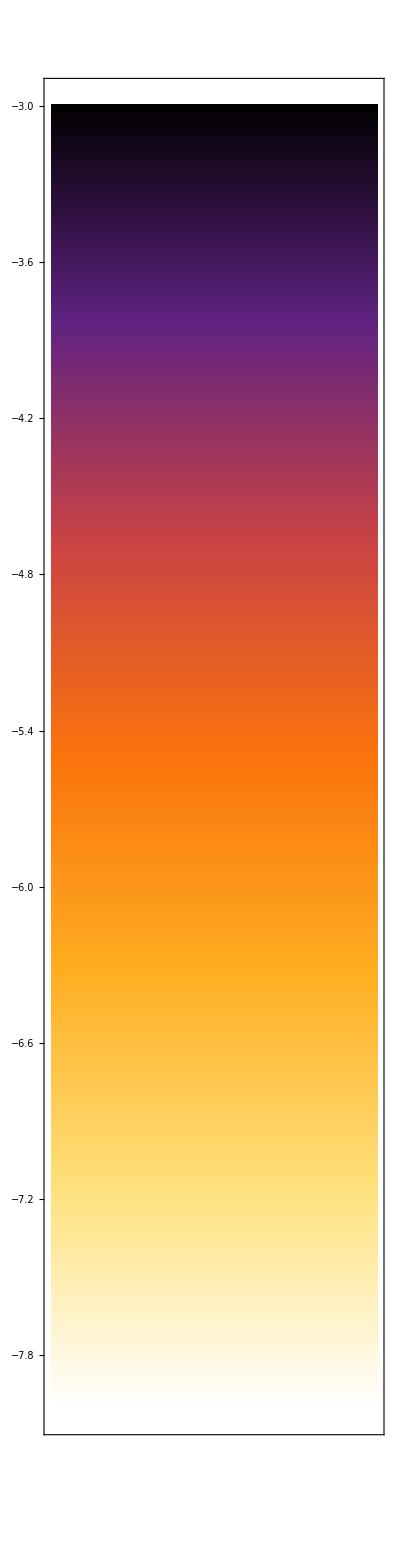

```mathematica
(* Color legend *)
LEG1 = S$COLOR$LEGEND[LEV,INT,COR1,LightGray,List["SunsetColors","Reverse"],40,15]
```

```mathematica
(* FMA data in space of frequencies {{fx_1,fy_1,d_1},{fx_2,fy_2,d_2},...} *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,DAT1] ;

(* Set parameter *)
LEV = 0. ;                       (* -- FMA index level, this value will be used for initials that left the aperture *)
INT = {-8.,-3.} ;                (* -- FMA index range, values outside of this range will be shifted to endpoints *)
H$BIN = 500 ;                    (* -- # of horizontal bins *)
V$BIN = 500 ;                    (* -- # of verticle bins *)
{H$MIN,H$MAX} = {0.350,0.380} ;  (* -- horizontal interval *)
{V$MIN,V$MAX} = {0.385,0.410} ;  (* -- vertical interval *)

(* Binarization *)
BIN = S$BINARIZE$REGION[
	{H$BIN,H$MIN,H$MAX},         (* -- horiontal bins and interval *)
	{V$BIN,V$MIN,V$MAX},         (* -- verticle bins and interval *)
	DAT,                         (* -- 3d data to binarize *)
	"FUNCTION" -> Max,            (* -- bin function, function to apply to data whithin one bin *)
	"DEFAULT" -> 0.0              (* -- empty bin default value *)
] ;

(* Generate color plot (legend is identical to coordinate space case) *)
FRE1 = S$COLOR$PLOT[
	LEV,                                              (* -- empty bin value *)
	INT,                                              (* -- data interval *)
	{H$MIN,H$MAX},                                    (* -- horizontal interval *)
	{V$MIN,V$MAX},                                    (* -- verticle interval *)
	BIN,                                              (* -- data *)
	Rule["SCHEME",List["SunsetColors","Reverse"]],    (* -- color scheme *)
	Rule["LEVEL",LightGray],                          (* -- empty bin color *)
	Rule[ImageSize,500],                              (* -- normal plot options *)
	Rule[AspectRatio,1]	
]
```

-Graphics-

```mathematica
(* Show result *)
FMA1 = Grid[
	List[
		List[
			Labeled[LEG1,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR1,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE1,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
]//Rasterize
```

-Graphics-

```mathematica
(* Case-2 (results) *)
ZER = 10.0^-12 ;
DAT = Map[DATA$X$Y$DELTA,DAT2] ;
LEV = 0. ;                
INT = {-8.,-3.} ;         
H$BIN = 500 ;             
V$BIN = 500 ;             
{H$MIN,H$MAX} = {-1.0,1.0} ;
{V$MIN,V$MAX} = {0.0,1.0}  ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX}, {V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0] ;
COR2 = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;
LEG2 = S$COLOR$LEGEND[LEV,INT,COR2,LightGray,List["SunsetColors","Reverse"],40,15] ;

ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,DAT2] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
FRE2 = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;

FMA2 = Grid[
	List[
		List[
			Labeled[LEG2,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR2,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE2,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] //Rasterize ;
```

```mathematica
(* Case-3 (results) *)
ZER = 10.0^-12 ;
DAT = Map[DATA$X$Y$DELTA,DAT3] ;
LEV = 0. ;                
INT = {-8.,-3.} ;         
H$BIN = 500 ;             
V$BIN = 500 ;             
{H$MIN,H$MAX} = {-1.0,1.0} ;
{V$MIN,V$MAX} = {0.0,1.0}  ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX}, {V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0] ;
COR3 = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;
LEG3 = S$COLOR$LEGEND[LEV,INT,COR3,LightGray,List["SunsetColors","Reverse"],40,15] ;

ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,DAT3] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
FRE3 = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;

FMA3 = Grid[
	List[
		List[
			Labeled[LEG3,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR3,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE3,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] //Rasterize ;
```

```mathematica
(* FMA results *)
(* As one can see from FMA plots, darker regions correspond to resonace and chaotic initial conditions *)
(* Effect of large FMA index for resonace initial conditions was discussed in previous example *)
(* Using larger samples can reduce this effect *)
(* If results seem suspicious further refinement can be performed *)
FMA1
FMA2
FMA3
```

-Graphics-

-Graphics--Graphics- | -Graphics--Graphics--Graphics- | -Graphics--Graphics--Graphics-

-Graphics-

```mathematica
(* Improved FMA plot resolution in frequency space *)
(* Since initial conditions are usually defined in space of coordinates, e.g. uniform grid as in this example, resolution in frequency space might be poor *)
(* To improve FMA plot resolution in frequency space one can try to generate initial conditions near points that correspond to a less dense regions in frequency space (or in some other region of interest) *)

(* The following procedure thus can be performed: *)
(* 1) Select points in frequency space (points in some region of interest, close to some resonance or several resonances, points within some interval of FMA index value) *)
(* 2) Find corresponding points in coordinate space and perturb their amplitudes randomly one or several times *)
(* 3) Filter perturbed points (e.g. keep only positive vertical coordinates for midplane symmetric problems) *)
(* 4) Perform FMA for perturbed points *)
(* 5) Add new data and check the result *)

(* Here resolution is improved for case-1 FMA *)

(* Alternatively, it is possible to use denser uniform grid or non-uniform grids in space of coordinates that is denser near DA boundary *)
```

```mathematica
(* As an example, three regions will be used to improve FMA plot resolution in frequency space *) 
(* FMA is performed using Case-1 parameters) *)

DAT = List[Map[Composition[Most,DATA$X$Y$DELTA],DAT1],Map[Composition[DATA$FX$FY$DELTA],DAT1]] ;
DAT = Map[Flatten,Transpose[DAT]] ;

(* Region-1: Rectangular region in frequency space *)
(* Select points for given region *)
REG1 = Select[DAT,Function[And[LessEqual[0.366,Part[Slot[1],3],0.371],LessEqual[0.403,Part[Slot[1],4],0.408]]]] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG1,All,List[1,2]],PlotStyle->Red]],
			Show[FRE1,ListPlot[Part[REG1,All,List[3,4]],PlotStyle->Red],Graphics[List[EdgeForm[Black],White,Opacity[0],Rectangle[List[0.366,0.403],List[0.371,0.408]]]]]
		]
	]
]//Rasterize

(* Region-2: Points close to selected resonances *)
(* Using S$RESONANCE$DIAGRAM[] two resonances were selected *)
RES1 = List[0,5,-2] ;  (* -- 0*nu_x + 5*nu_y == 2 *)
RES2 = List[6,2,-3] ;  (* -- 6*nu_x + 2*nu_y == 3 *)
(* Selection of points close to given resonance can be done witn S$SELECT[] function *) 
SEL1 = S$SELECT[      (* -- select point close to resonance *)
	RES1,             (* -- resonance *)
	1.0*10^-3,            (* -- distance to resonance in frequncy space *)
	DAT,              (* -- FMA data *)
	List[3,4]         (* -- positions of frequencies within FMA data *)
] ;
SEL2 = S$SELECT[RES2,1.0*10^-3,DAT,List[3,4]] ;
REG2 = Join[SEL1,SEL2] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG2,All,List[1,2]],PlotStyle->Blue]],
			Show[
				FRE1,
				ListPlot[Part[REG2,All,List[3,4]],PlotStyle->Blue],
				ContourPlot[{0*X+5*Y==2,6*X+2*Y==3},{X,0.,0.5},{Y,0.,0.5},ContourStyle->Black],
				PlotRange -> List[List[0.350,0.380],List[0.385,0.410]]
			]
		]
	]
] // Rasterize

(* Region-3: Points with large FMA index values *)
REG3 = Select[
	DAT,
	Function[
		And[
			GreaterEqual[Part[Slot[1],-1],-3.5]
		]
	]
] ;
(* Plot selected points *)
Grid[
	List[
		List[
			Show[COR1,ListPlot[Part[REG3,All,List[1,2]],PlotStyle->Magenta]],
			Show[FRE1,ListPlot[Part[REG3,All,List[3,4]],PlotStyle->Magenta],PlotRange -> List[List[0.350,0.380],List[0.385,0.410]]]
		]
	]
]//Rasterize
(* In all cases S$FILTER$DATA[] function can be used to select more uniform data in frequency space *)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(* Perturbation of initial conditions in space of coordinates can be done with S$PERTURB[] function *)
(* Region-1 *)
(* Select coordinates *)
INI1 = Part[REG1,All,List[1,2]] ;
(* Perturb coordinates *)
INI1 = S$PERTURB[                                  (* -- perturb initials *)
	30,                                            (* -- number of repetitions *)
	List[List[-0.01,0.01],List[-0.01,0.01]],       (* -- perturbation strength  *)
	INI1                                           (* -- initials to perturb *)
] ;
(* Filter initials *)
INI1 = DeleteCases[INI1,List[_,_?Negative]] ;
(* Generate full initial condition *)
INI1 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI1
] ;
(* Region-2 *)
INI2 = Part[REG2,All,List[1,2]] ;
INI2 = S$PERTURB[100,List[List[-0.01,0.01],List[-0.01,0.01]],INI2] ;
INI2 = DeleteCases[INI2,List[_,_?Negative]] ;
INI2 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI2
] ;
(* Region-3 *)
INI3 = Part[REG3,All,List[1,2]] ;
INI3 = S$PERTURB[10,List[List[-0.01,0.01],List[-0.01,0.01]],INI3] ;
INI3 = DeleteCases[INI3,List[_,_?Negative]] ;
INI3 = Map[
	Function[
		Block[
			{X,Y},
			{X,Y} = Slot[1] ;
			{1.0,X,10.^-10,Y,10.^-10}
		]
	],
	INI3
] ;
INI1//Length
INI2//Length
INI3//Length
```

157764

291119

112845

```mathematica
(* Perform FMA for new initial conditions *)

(* Region-1 *)
INI = INI1 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^10/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^10,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_1_1.mx",DAT,"MX"]

(* Region-2 *)
INI = INI2 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^10/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^10,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_1_2.mx",DAT,"MX"]

(* Region-3 *)
INI = INI3 ;
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,True,2,2^10/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^10,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]+I*Part[DAT,All,List[3,5]]]] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_1_3.mx",DAT,"MX"]
```

157764

1.

fma_1_1.mx

287335

0.987002

fma_1_2.mx

104583

0.926785

fma_1_3.mx

```mathematica
(* Import saved data *)
DAT0 = Import["fma_1.mx"] ;
DAT1 = Import["fma_1_1.mx"] ;
DAT2 = Import["fma_1_2.mx"] ;
DAT3 = Import["fma_1_3.mx"] ;
```

```mathematica
(* Check results *)

(* Initial FMA data *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,DAT0] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] //Rasterize

(* Initial FMA data and 1st region *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,Join[DAT0,DAT1]] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] //Rasterize

(* Initial FMA data and 2nd region *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,Join[DAT0,DAT2]] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] //Rasterize

(* Initial FMA data and 3rd region *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,Join[DAT0,DAT3]] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] //Rasterize

(* Initial FMA data and all regions *)
ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,Join[DAT0,DAT1,DAT2,DAT3]] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] //Rasterize
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
(* In some cases 'largest' computed frequency might not be fundamental *) 
(* Or frequencies computed for different time intervals might correspond to different peaks *)
(* This problem can be solved by tracking several peaks *)
(* In Case-4 three peaks are tracked *)
```

```mathematica
(* Case-4 *)
(* Intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,2^14/2,10,20,Automatic] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FMA,VAL,FRE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[2^14,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			FMA = S$FMA[Transpose[Part[DAT,All,List[2,4]]],"MODE"->"MULTIPLE","PEAK"->3] ;
			Join[Part[POI,List[2,4]],FMA]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fma_4.mx",DAT,"MX"]
```

501

501

251001

100729

0.401309

fma_4.mx

```mathematica
(* Import data *)
DATA = Import["fma_4.mx"] ;
```

```mathematica
(* Format data *)
DATA = Cases[DATA,{X_,Y_,F___} :> {{X,Y},F}] ; 
DATA = SortBy[DATA,Composition[Norm,First]] ;
DATA = Cases[DATA,{{X_,Y_},F___} :> {X,Y,{F}}] ;
```

```mathematica
(* In this example, for each initial condition on X-Y plane three peaks are tracked for two time intervals *)
(* {X,Y,{X_DATA,Y_DATA}} *)
(* X_DATA = {{FX1_T1,FX2_T1,FX3_T1},{FX1_T2,FX2_T2,FX3_T2}} *)
(* Y_DATA = {{FY1_T1,FY2_T1,FY3_T1},{FY1_T2,FY2_T2,FY3_T2}} *)
(* For {X,Y} = {0.0,0.0} and small initial values for both momenta PX and PY the ordering is correct *)
(* For other initial conditions this ordering can 'flip' and if one moves from small amplutudes frequencies might have artificial 'jumps' *)
(* Having obtained data for several peaks it is possible to re-order data assuming: *)
(* 1) frequencies have correct ordering for small amplitudes *)
(* 2) frequency variation is somewhat continious in space *)
Part[DATA,1]
```

{0.,0.,{{{0.38,0.24,0.18},{0.38,0.24,0.18}},{{0.41,0.21,0.03},{0.41,0.21,0.03}}}}

```mathematica
(* For this example artificial 'flip' is added in horizontal plane *)
(* Correct frequency values are replaced by the second peak *)
(* Normaly a 'flip' might appear for small values of X and large values of Y for the first peak *)
DATA = DATA /. 
	{X_,Y_,{{{FX1T1_,FX2T1_,FX3T1_},{FX1T2_,FX2T2_,FX3T2_}},Z___}} /; (-0.1 ≤ X ≤ 0.1 && 0.1 ≤ Y ≤ 0.5) :> {X,Y,{{{FX2T1,FX1T1,FX3T1},{FX2T2,FX1T2,FX3T2}},Z}} ;
	
DATA = DATA /. 
	{X_,Y_,{{{FX1T1_,FX2T1_,FX3T1_},{FX1T2_,FX2T2_,FX3T2_}},Z___}} /; (-0.5 ≤ X ≤ -0.2 && 0.3 ≤ Y ≤ 0.5) :> {X,Y,{{{FX3T1,FX1T1,FX2T1},{FX3T2,FX1T2,FX2T2}},Z}} ;
```

```mathematica
(* As a first step, data binarization is performed in X-Y space *)
PLANE = 1 ;                       (* -- target frequencies *)
ORDER = 250 ;                     (* -- number of bins to use *)
DIMENSION = 2*ORDER + 1 ;         (* -- number of elements *)
DEFAUL = 0.0 ;                    (* -- default value for frequencies *)
{HMIN,HMAX} = {-1.0,1.0} ;        (* -- horizontal data interval *)
{VMIN,VMAX} = {-1.0,1.0} ;        (* -- verticle data interval *)
STEP = 2.0/DIMENSION ;            (* -- bin size *)
HOR = Part[DATA,All,1] ;          (* -- horizontal space data *)
VER = Part[DATA,All,2] ;          (* -- verticle space data *)
VAL = Part[DATA,All,3,PLANE,1] ;  (* -- frequencies corresponding to selected plane *)
VAL = Transpose[VAL] ;
(* Data to binarize *)
SET = Map[Function[Transpose[List[HOR,VER,Slot[1]]]],VAL] ;
(* Binarize data *)
BIN = Map[Function[S$BINARIZE$REGION[{DIMENSION,STEP,STEP},Slot[1],"DEFAULT" -> DEFAUL, "FUNCTION" -> First]], SET] ;
(* Plot frequencies *)
INP = Map[Transpose,Transpose[Normal[BIN]]] ;
PLO = Grid[
	{
		{
			MatrixPlot[INP[[All,All,1]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25],
			MatrixPlot[INP[[All,All,2]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25],
			MatrixPlot[INP[[All,All,3]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25]
		}
	}
]
```

-Graphics- | -Graphics- | -Graphics-

```mathematica
(* The above plots show dependence of horizontal frequency on initial condition in space of coordinates for three tracked peaks *)
(* As it can be seen, in this example, the 1st peak frequency variation in not space is continuous *)
```

```mathematica
(* Check data *)
TAB = NestList[S$NEXT$BOUNDARY$LAYER,S$FIRST$BOUNDARY$LAYER,ORDER-1] ; // AbsoluteTiming
TAB = Map[Flatten[Map[Most,#],1]&,TAB] ;
TAB = Join[{{{0,0}}},TAB] ;
TAB = Flatten[TAB,1] ;
RES = S$CHECK$DATA[ORDER,ORDER,TAB,INP,DEFAUL,1] ; // AbsoluteTiming
```

{0.035781,Null}

{18.4098,Null}

```mathematica
(* Compare input data and checked data *)
PLO
Grid[
	{
		{
			MatrixPlot[RES[[All,All,1]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25],
			MatrixPlot[RES[[All,All,2]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25],
			MatrixPlot[RES[[All,All,3]],PlotRange -> {0.0,0.5}, DataRange -> {{HMIN,HMAX},{VMIN,VMAX}}, ColorRules->{DEFAUL->LightGray},ImageSize -> 300,ImagePadding -> 25]
		}
	}
]
```

-Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics-

```mathematica
(* The main target of this procedure is to remove 'jumps' int the 1st peak by reordering frequencies of several peaks *)
(* Here it is assumed that the correct 1st peak data is present in one of additional tracked peaks *)
(* The number of peaks to track impose heavy performance penalty *)
(* It the above plots it can be seen, that the 1st peak data is successfully reordered *)
(* But more peaks are needed to make other peaks continious *)
```

```mathematica
(* The next step is to reoder original data *)
ORD = S$BINARIZE$REGION[{DIMENSION,STEP,STEP},First[SET],"DEFAULT" -> DEFAUL,"FUNCTION" -> First,"ORDERING" -> True] ;
ORD = Extract[Transpose[Reverse[RES]],ORD] ;
OUT = Transpose[VAL] ;
OUT = S$REORDER$ARRAY[OUT,ORD] ;
```

```mathematica
(* Full horizontal plane data for 1st peak *)
SLICE = PLANE ;
SLICE = Part[DATA,All,3,SLICE] ;
SLICE = Rest[Transpose[SLICE]] ;
SLICE = Map[S$REORDER$ARRAY[#,OUT]&,SLICE]  ;
SLICE = Join[{OUT},SLICE] // Transpose ;
SLICE = Map[Composition[First,Transpose],SLICE] ;
```

```mathematica
SLICE$H = SLICE ;
```

```mathematica
(* Same should be done for verticle plane *)
SLICE$V = SLICE ;
```

```mathematica
HOR = Part[DATA,All,1] ;
VER = Part[DATA,All,2] ;
NUX = SLICE$H ;                            (* -- ordered data for horizontal plane *)
NUY = SLICE$V ;                            (* -- ordered data for verticle plane (repeat the above computations with PLANE = 2 ) *)
RESULT = {HOR,VER,NUX,NUY} // Transpose ;
First[RESULT]
```

{0.,0.,{0.38,0.38},{0.41,0.41}}

## (+) EXAMPLE-06: FDE

```mathematica
(* Fractal Dimension Estimation (FDE) *)

(* In this example, basic FDE workflow is presented *)
(* FDE is based on the estimation of fractal dimension from power spectra length computed for different sample length *)
(* FDE returns dimension which for regular orbits should be close to one *)
(* If FDE indicator is larger or smaller then one, corresponding orbit might be chaotic *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* FDE can be computed by S$FDE[] function that uses S$PSL[] function for spectra length computation *) 
(* S$PSL[<SIGNAL>,<OPTIONS>] -- compute power spectra length for given input signal <SIGNAL> and option(s) <OPTIONS> *)
S$PSL//Options
(* S$FDE[<RANGE>,<SIGNAL>,<OPTIONS>] -- compute FDE for rangle of sample length <RANGE> = {<LENGTH_1>,<LENGTH_2>,...}, input signa <SIGNAL> and option(s) <OPTIONS> *)
S$FDE//Options
(* S$FDE method can be "FIT" (default) or "CORRELATION" *)
```

{WINDOW→1,PROCESS→True,LEVEL→1.×10^-12,COMPLEX→False}

{WINDOW→1,PROCESS→True,LEVEL→1.×10^-10,COMPLEX→False,METHOD→FIT}

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) *)
(* MAP: {W,Q1,P1,Q2,P2} -> {W,Q1,P1,Q2,P2} *)
(* W            -- aperture flag (1 or 0) *)
(* Q1,P1,Q2,P2  -- canonical coordinates *)
(* Set map parameters *)
FREQUENCY1 = 2*Pi*0.38 ;
FREQUENCY2 = 2*Pi*0.41 ;
ClearAll[MAP] ;
MAP = With[
	{
		COS1 = Cos[FREQUENCY1],
		SIN1 = Sin[FREQUENCY1],
		COS2 = Cos[FREQUENCY2],
		SIN2 = Sin[FREQUENCY2]
	},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2},
			{W,Q1,P1,Q2,P2} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Q1^2+Q2^2,25.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				List[
					W,
					COS1*Q1+((Q1^2-Q2^2)+P1)*SIN1,
					COS1*((Q1^2-Q2^2)+P1)-Q1*SIN1,
					COS2*Q2+((-2*Q1*Q2)+P2)*SIN2,
					COS2*((-2*Q1*Q2)+P2)-Q2*SIN2
				],
				List[W,Q1,P1,Q2,P2]
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Compute FDE for several initial conditions *)
(* Generate orbits *)
RES = NestList[MAP,List[1.,0.1106,0.,0.54,0.0],2^20-1] ;              (* -- regular trajectrory close to resonance *)
CHA = NestList[MAP,List[1.,0.6892500005,0.,0.1,0.0],2^20-1] ;         (* -- chaotic trajectory *)
(* Plot first 2^14 iterations *)
Grid[
	List[
		List[
			ListPlot[Part[RES,Span[1,2^14,1],List[2,3]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Red],
			ListPlot[Part[CHA,Span[1,2^14,1],List[2,3]],PlotTheme -> "Detailed",AspectRatio -> 1,ImageSize -> 300,PlotStyle -> Blue]
		]
	]
]//Rasterize
(* Set signals (use 1st coordinate) *)
RES = First[Rest[Transpose[RES]]] ;
CHA = First[Rest[Transpose[CHA]]] ;
(* Compute FDE using samples defined by Range[100000,1000000,100000], i.e. spectra length is computed for 100000, 200000, ..., 1000000 points *)
(* As expected FDE for regular trajectory is close to one, while it is not the fact for chaotic case *)
S$FDE[Range[100000,1000000,100000],RES,"WINDOW" -> 0]
S$FDE[Range[100000,1000000,100000],CHA,"WINDOW" -> 0]
```

-Graphics-

0.998264

1.45914

```mathematica
(* Perform FDE for initial grid in space of coordinates *)
(* Initiallization and intitial grid *)
INI = Table[
	{1.0,X,10.^-10,Y,10.^-10},
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FDE},
			POI = Slot[1] ;
			DAT = NestList[MAP,POI,Subtract[100000,1]] ;
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = First[Rest[Transpose[DAT]]] ;
			FDE = S$FDE[Range[25000,100000,25000],DAT] ;
			Flatten[List[Part[POI,List[2,4]],FDE]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fde_1.mx",DAT,"MX"]
```

501

501

251001

98965

0.394281

fde_1.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT = Import["fde_1.mx"] ;
```

```mathematica
(* Plot sorted FDE values *)
(* As it can be seen for some initial conditions FDE values deviate significantly from one (can be both greater and less then one) *)
ListPlot[
	Sort[Map[Last,DAT]],
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	AspectRatio -> 1/2,
	PlotStyle -> Black,
	PlotRange -> All
]//Rasterize
```

-Graphics-

```mathematica
(* Plot sample trajectories *)
(* FDE < 1 *)
INI$1 = First[SortBy[DAT,Last]] ;
FDE$1 = Last[INI$1] ;
INI$1 = N[Flatten[List[1,Transpose[List[Take[INI$1,2],ConstantArray[10^-10,2]]]]]] ;
TRJ$1 = NestList[MAP,INI$1,2^14] ;
(* FDE > 1 *)
INI$2 = Last[SortBy[DAT,Last]] ;
FDE$2 = Last[INI$2] ;
INI$2 = N[Flatten[List[1,Transpose[List[Take[INI$2,2],ConstantArray[10^-10,2]]]]]] ;
TRJ$2 = NestList[MAP,INI$2,2^14] ;
(* FDE = 1 *)
INI$3 = First[SortBy[MapAt[Composition[Abs,Curry[Subtract][1]],DAT,List[All,-1]],Last]] ;
FDE$3 = Plus[1,Last[INI$3]] ;
INI$3 = N[Flatten[List[1,Transpose[List[Take[INI$3,2],ConstantArray[10^-10,2]]]]]] ;
TRJ$3 = NestList[MAP,INI$3,2^14] ;
(* Plot phase space trajectories *)
Grid[
	List[
		List[StringTemplate["FDE = ``"][FDE$1],Null],
		List[
			ListPlot[List[Part[TRJ$1,All,List[2,3]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All],
			ListPlot[List[Part[TRJ$1,All,List[4,5]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All]
		],
		List[StringTemplate["FDE = ``"][FDE$2],Null],
		List[
			ListPlot[List[Part[TRJ$2,All,List[2,3]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All],
			ListPlot[List[Part[TRJ$2,All,List[4,5]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All]
		],
		List[StringTemplate["FDE = ``"][FDE$3],Null],
		List[
			ListPlot[List[Part[TRJ$3,All,List[2,3]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All],
			ListPlot[List[Part[TRJ$3,All,List[4,5]]],AspectRatio->1,PlotTheme->"Detailed",ImageSize->400,PlotStyle->Black,PlotRange->All]
		]				
	],
	Alignment -> Center
]//Rasterize
```

-Graphics-

```mathematica
(* Better indicator can be obtained if FDE deviation from one is used *)
ListPlot[
	Sort[Abs[Subtract[Map[Last,DAT],1]]],
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	AspectRatio -> 1/2,
	PlotStyle -> Black,
	PlotRange -> All
]//Rasterize
```

-Graphics-

```mathematica
BIN = Sort[Abs[Subtract[Map[Last,DAT],1]]] ;
Histogram[
	BIN,
	List[0,0.1,0.005],
	PlotRange -> All,
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	AspectRatio -> 1/2,
	PlotRange -> All,
	ChartStyle -> Black
]//Rasterize
```

-Graphics-

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Generate FDE color plot *)
(* Set FDE indicator background level *)
LEV = 0. ; 
(* Set FDE indicator interval (values outside this interval are shifted to endpoints) *)       
INT = List[0.0,1.0] ;
(* Set intervals for coordinates *)
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
(* Data binarization *)
BIN = MapAt[Composition[Abs,Curry[Subtract][1],Abs],DAT,List[All,-1]] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},BIN,Rule["DEFAULT",LEV],Rule["FUNCTION",Mean]] ;
(* Generate color plot and legend *)
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME",List["SunsetColors","Reversed"]],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,List["SunsetColors","Reversed"],40,15] ;
(* Plot result *)
FDE = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\textrm{FDE}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
]//Rasterize
(* Compare with FMA results *)
```

-Graphics-

## (+) EXAMPLE-07: FLI

```mathematica
(* Fast Lyapunov Indicator (FLI) *)

(* In this example, basic FLI workflow is presented *)
(* FLI is based on evaluation of tangent vectors *)
(* One or several (orthonormal) deviation vectors can be used for FLI computation *)
(* Maximum number of orthonormal deviation vectors for the given system is equal to its phase space dimension *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* Several functions are available for FLI computation (see references or SRC_SIGNAL for implementation details) *)

(* <OUT> = S$FLI$ONE[<VEC>] -- compute FLI using one deviation vector *)
(* <VEC>                    -- deviation vector for all iterations, <VEC> = {<VEC_1>,<VEC_2>,...,<VEC_N>} *)
(* <OUT>                    -- list of (folded) FLI indicators *)

(* <OUT> = S$FLI$ALL[<VEC>] -- compute FLI using several deviation vectors *)
(* <VEC>                    -- sequence of deviation vectors for all iterations *)
(* <OUT>                    -- list of (folded) FLI indicators *)

(* <OUT> = S$FLI$LAS[<VEC>] -- compute FLI using several deviation vectors (or S$FLI[<VEC>]) *)
(* <VEC>                    -- sequence of deviation vectors for all iterations *)
(* <OUT>                    -- max FLI indicator *)

(* All FLI functions use S$FLI$FUN function (default is Max) for folding *) 
(* This function removes oscillations of FLI indicator *)
(* {<FLI_1>,<FLI_2>,<FLI_3>,...} => {<FLI_1>,S$FLI$FUN[{<FLI_1>,<FLI_2>}],S$FLI$FUN[{S$FLI$FUN[{<FLI_1>,<FLI_2>}],<FLI_3>}],...} *)
```

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) and tangent dynamics *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				(* Map & tangent map *)
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = {
					W,
					$B1 (P1 + (Q1^2 - Q2^2) $W) Sin[$Q1] + Q1 (Cos[$Q1] + $A1 Sin[$Q1]),
					-((Q1 (1 + $A1^2) Sin[$Q1])/$B1) + (P1 + (Q1^2 - Q2^2) $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					Q2 Cos[$Q2] + (P2 $B2 + Q2 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((Q2 (1 + $A2^2) Sin[$Q2])/$B2) + (P2 - 2 Q1 Q2 $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V11 Cos[$Q1] + ($B1 (V12 - 2 Q2 V13 $W) + V11 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V11 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V11 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V12 - 2 Q2 V13 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V13 Cos[$Q2] + ($B2 (V14 - 2 Q2 V11 $W) + V13 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((V13 (1 + $A2^2) Sin[$Q2])/$B2) + (V14 - 2 (Q2 V11 + Q1 V13) $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V21 Cos[$Q1] + ($B1 (V22 - 2 Q2 V23 $W) + V21 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V21 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V21 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V22 - 2 Q2 V23 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V23 Cos[$Q2] + ($B2 (V24 - 2 Q2 V21 $W) + V23 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V24 - 2 (Q2 V21 + Q1 V23) $W) Cos[$Q2] - (($A2 $B2 (V24 - 2 Q2 V21 $W) + V23 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V31 Cos[$Q1] + ($B1 (V32 - 2 Q2 V33 $W) + V31 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V31 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V31 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V32 - 2 Q2 V33 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V33 Cos[$Q2] + ($B2 (V34 - 2 Q2 V31 $W) + V33 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V34 - 2 (Q2 V31 + Q1 V33) $W) Cos[$Q2] - (($A2 $B2 (V34 - 2 Q2 V31 $W) + V33 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V41 Cos[$Q1] + ($B1 (V42 - 2 Q2 V43 $W) + V41 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V41 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V41 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V42 - 2 Q2 V43 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V43 Cos[$Q2] + ($B2 (V44 - 2 Q2 V41 $W) + V43 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V44 - 2 (Q2 V41 + Q1 V43) $W) Cos[$Q2] - (($A2 $B2 (V44 - 2 Q2 V41 $W) + V43 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2
				} ;
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44}
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Compute FLI indicator (full list) for several initial conditions *)

(* Regular initial condition (red) *)
REG = Flatten[List[List[1.,0.05,0.,0.05,0.],N[IdentityMatrix[4]]]] ;                     (* -- generate initial condition including deviation vectors *)
REG = NestList[MAP,REG,2^16] ;                                                           (* -- iterate map *)
REG = Rest[REG] ;                                                                        (* -- drop initial condition from the list *)
REG = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],REG] ;  (* -- keep only deviation vectors and partition them *)
REG = Transpose[REG] ;                                                                   (* -- form sequence of deviation vectors *)
REG = Apply[S$FLI$ALL,REG] ;                                                             (* -- compute FLI list *)

(* Regular initial condition close to resonance (blue) *)
RES = Flatten[List[List[1.,0.1106,0.,0.54,0.0],N[IdentityMatrix[4]]]] ;
RES = NestList[MAP,RES,2^16] ;
RES = Rest[RES] ;
RES = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],RES] ;
RES = Transpose[RES] ;
RES = Apply[S$FLI$ALL,RES] ;

(* Chaotic initial condition (magenta) *)
CHA = Flatten[List[List[1.,0.6892500005,0.,0.1,0.0],N[IdentityMatrix[4]]]] ;
CHA = NestList[MAP,CHA,2^16] ;
CHA = Rest[CHA] ;
CHA = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],CHA] ;
CHA = Transpose[CHA] ;
CHA = Apply[S$FLI$ALL,CHA] ;

(* Plot result *)
ListPlot[
	List[REG,RES,CHA],
	PlotTheme -> "Detailed",
	ImageSize -> 800,
	AspectRatio -> 1/2,
	PlotStyle -> List[Red, Blue, Magenta]
]//Rasterize
```

-Graphics-

```mathematica
(* Perform FLI for initial grid in space of coordinates  *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,FLI},
			POI = Slot[1] ;                            
			DAT = NestList[MAP,POI,Subtract[2^12,1]] ; 
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = Rest[DAT] ;
			DAT = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],DAT] ;
			DAT = Transpose[DAT] ;
			FLI = Apply[S$FLI$LAS,DAT] ;
			Set[$HistoryLength,0] ;
			Clear[DAT] ;
			Flatten[List[Part[POI,List[2,4]],FLI]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save result *)
SetDirectory[NotebookDirectory[]] ;
Export["fli_1.mx",DAT,"MX"]
```

501

501

251001

102703

0.409174

fli_1.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT = Import["fli_1.mx"] ;
```

```mathematica
(* Plot sorted FLI values *)
ListPlot[
	Sort[Map[Last,DAT]],
	PlotTheme -> "Detailed",
	ImageSize -> 600,
	AspectRatio -> 1/2,
	PlotStyle -> Black,
	PlotRange -> All
]//Rasterize
```

-Graphics-

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Generate FLI color plot *)
(* Interval is selected based on the above plot *)
(* As it can be seen chaotic initial conditions mostly appear near the boundary of stability *)
(* Some resonance structure can still be seen for regular regions *)
(* Set FLI background level *)
LEV = 0. ;                    
(* Set FLI interval *) 
INT = List[5.,50.] ;
(* Set intervals for coordinates *)
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
(* Data binarization *)
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
(* Generate color plot and legend *)
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME",List["SunsetColors","Reversed"]],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,List["SunsetColors","Reversed"],40,15] ;
(* Show result *)
FLI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{FLI}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] //Rasterize
```

-Graphics-

## (+) EXAMPLE-08: SALI & GALI

```mathematica
(* The Smaller and the Generalized Alignment Indices (SALI & GALI) *)

(* In this example, basic SALI & GALI workflow is presented *)
(* SALI & GALI are based on evaluation of (normalized at each iteration) tangent vectors *)
(* Two deviation (orthonormal) vectors can be used for SALI computation *)
(* Two or more deviation (orthonormal) vectors can be used for GALI computation *)
(* Maximum number of orthonormal deviation vectors for the given system is equal to its phase space dimension *)
(* SALI is equivalent to GALI(2), i.e. GALI computed using two deviation vectors *)
(* For SALI & GALI the quantity of interest is evolution of angles between deviation vectors *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
```

```mathematica
(* SALI indicator can be computed using  S$SALI[] function *)
(* <OUT> = S$SALI[{<VEC_1>,<VEC_2>}] *)
(* <VEC_I> -- deviation vector given at some iteration *)
(* <OUT> -- SALI indicator value *)

(* GALI indicator(s) can be computed using  S$GALI[] function *)
(* <OUT> = S$GALI[{<VEC_1>,<VEC_2>,...}] *)
(* <VEC_I> -- deviation vector given at some iteration *)
(* <OUT> -- GALI indicator value *)
(* GALI(2) = S$GALI[{<VEC_1>,<VEC_2>}] *)
(* GALI(3) = S$GALI[{<VEC_1>,<VEC_2>,<VEC_3>}] *)

(* Both S$SALI[] and S$GALI[] functions use S$INDEX$LEVEL parameter (some small number) which is added to actual indicator value *)
(* Default level value is: *)
S$INDEX$LEVEL
```

1.×10^-14

```mathematica
(* Define quadratic symplectic map with internal aperture (Henon) with normalized tangent dynamics *)
(* Set map parameters *)
F1 = 2 Pi 0.38 ;
F2 = 2 Pi 0.41 ;
A1 = 0.0 ;
B1 = 1.0 ;
A2 = 0.0 ;
B2 = 1.0 ;
(* Generate compiled map *)
ClearAll[MAP] ;
MAP = With[
	{$Q1 = F1, $Q2 = F2, $W = 1.0, $A1 = A1, $B1 = B1, $A2 = A2, $B2 = B2},
	Compile[
		{{X,_Real,1}},
		Block[
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
			{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = X ;
			(* Check aperture and change flag *)
			If[
				Greater[Norm[List[Q1,Q2]],5.0],
				W = 0. ;
			] ;
			(* Iterate for valid flag value *)
			If[
				W > 0.5,
				(* Map & tangent map *)
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44} = {
					W,
					$B1 (P1 + (Q1^2 - Q2^2) $W) Sin[$Q1] + Q1 (Cos[$Q1] + $A1 Sin[$Q1]),
					-((Q1 (1 + $A1^2) Sin[$Q1])/$B1) + (P1 + (Q1^2 - Q2^2) $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					Q2 Cos[$Q2] + (P2 $B2 + Q2 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((Q2 (1 + $A2^2) Sin[$Q2])/$B2) + (P2 - 2 Q1 Q2 $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V11 Cos[$Q1] + ($B1 (V12 - 2 Q2 V13 $W) + V11 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V11 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V11 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V12 - 2 Q2 V13 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V13 Cos[$Q2] + ($B2 (V14 - 2 Q2 V11 $W) + V13 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					-((V13 (1 + $A2^2) Sin[$Q2])/$B2) + (V14 - 2 (Q2 V11 + Q1 V13) $W) (Cos[$Q2] - $A2 Sin[$Q2]),
					V21 Cos[$Q1] + ($B1 (V22 - 2 Q2 V23 $W) + V21 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V21 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V21 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V22 - 2 Q2 V23 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V23 Cos[$Q2] + ($B2 (V24 - 2 Q2 V21 $W) + V23 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V24 - 2 (Q2 V21 + Q1 V23) $W) Cos[$Q2] - (($A2 $B2 (V24 - 2 Q2 V21 $W) + V23 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V31 Cos[$Q1] + ($B1 (V32 - 2 Q2 V33 $W) + V31 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V31 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V31 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V32 - 2 Q2 V33 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V33 Cos[$Q2] + ($B2 (V34 - 2 Q2 V31 $W) + V33 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V34 - 2 (Q2 V31 + Q1 V33) $W) Cos[$Q2] - (($A2 $B2 (V34 - 2 Q2 V31 $W) + V33 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2,
					V41 Cos[$Q1] + ($B1 (V42 - 2 Q2 V43 $W) + V41 ($A1 + 2 Q1 $B1 $W)) Sin[$Q1],
					-((V41 (1 + $A1^2) Sin[$Q1])/$B1) + 2 Q1 V41 $W (Cos[$Q1] - $A1 Sin[$Q1]) + (V42 - 2 Q2 V43 $W) (Cos[$Q1] - $A1 Sin[$Q1]),
					V43 Cos[$Q2] + ($B2 (V44 - 2 Q2 V41 $W) + V43 ($A2 - 2 Q1 $B2 $W)) Sin[$Q2],
					(V44 - 2 (Q2 V41 + Q1 V43) $W) Cos[$Q2] - (($A2 $B2 (V44 - 2 Q2 V41 $W) + V43 (1 + $A2^2 - 2 Q1 $A2 $B2 $W)) Sin[$Q2])/$B2
				} ;
				(* Normalization of deviation vectors *)
				{V11,V12,V13,V14} = {V11,V12,V13,V14}/Norm[{V11,V12,V13,V14}] ; 
				{V21,V22,V23,V24} = {V21,V22,V23,V24}/Norm[{V21,V22,V23,V24}] ; 
				{V31,V32,V33,V34} = {V31,V32,V33,V34}/Norm[{V31,V32,V33,V34}] ; 
				{V41,V42,V43,V44} = {V41,V42,V43,V44}/Norm[{V41,V42,V43,V44}] ; 
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44},
				{W,Q1,P1,Q2,P2,V11,V12,V13,V14,V21,V22,V23,V24,V31,V32,V33,V34,V41,V42,V43,V44}
			]
		],
		CompilationOptions -> List["ExpressionOptimization" -> True],
		CompilationTarget -> "C"
	]
] ;
```

```mathematica
(* Perform SALI & GALI for initial grid in space of coordinates *)
(* In this example SALI and GALI(2/3/4) are computed *)
(* MAP is iterated 2^10 times, then additional 2^8 iterations are performed and orbit history is recorded *)
(* For all recorded orbits SALI & GALI indicators are computed and minimum values are returned *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,DAT,DV1,DV2,DV3,DV4,SAL,GAL},
			POI = Slot[1] ;                            
			DAT = Nest[MAP,POI,Subtract[2^10,1]] ; 
			If[SameQ[Chop[First[DAT]],0],Throw[Nothing]] ;
			DAT = NestList[MAP,DAT,Subtract[2^8,1]] ; 
			If[SameQ[Chop[First[Last[DAT]]],0],Throw[Nothing]] ;
			DAT = Map[Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]],DAT] ;
			List[DV1,DV2,DV3,DV4] = Transpose[DAT] ;
			SAL = Min[Map[S$SALI,Transpose[List[DV1,DV3]]]] ;
			GAL = List[
				Min[Map[S$GALI,Transpose[List[DV1,DV3]]]],
				Min[Map[S$GALI,Transpose[List[DV1,DV2,DV3]]]],
				Min[Map[S$GALI,Transpose[List[DV1,DV2,DV3,DV4]]]]
			] ;
			Flatten[List[Part[POI,List[2,4]],SAL,GAL]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save data *)
SetDirectory[NotebookDirectory[]] ;
Export["ali_1.mx",DAT,"MX"]
```

501

501

251001

104468

0.416206

ali_1.mx

```mathematica
(* In this example T-GALI(MAX) is computed (compute 'time' required to reach given index level using all deviation vectors) *)
(* MAP is iterated up to 2^18 times *)
(* After each iteration apetrure is checked and GALI(4) is computed *)
(* If its value is less then 10^-10, the iteration loop is terminated and  number of iterations is returned *)
(* Initiallization and intitial grid *)
INI = Table[
	Flatten[
		List[
			List[1.0,X,10.^-10,Y,10.^-10],                         (* -- normal initial condition with aperture flag *)
			Orthogonalize[RandomReal[List[-1,+1],List[4,4]]]       (* -- tangent part *)
		]
	],
	{X,-1.0,1.0,0.1/25},
	{Y,0.0,1.0,0.1/2/25}
] ;
INI//Length
INI//First//Length
INI = Flatten[INI,1] ;
Length[INI]
INI = Developer`ToPackedArray[INI] ;
(* Task function *)
ClearAll[FUN] ;
FUN = Function[
	Catch[
		Block[
			{POI,ITR,DAT,GAL},
			POI = Slot[1] ;
			(* Iteration loop *)                            
			Do[
				List[
					POI = MAP[POI] ;
					If[SameQ[Chop[First[POI]],0],Throw[Nothing]] ;
					DAT = Composition[Function[Partition[Slot[1],4]],Function[Drop[Slot[1],5]]][POI] ;
					DAT = Transpose[DAT] ;
					GAL = S$GALI[DAT] ;
					If[
						LessEqual[GAL,N[Log10[Power[10,Times[Subtract[0,1],10]]]]],
						Throw[Flatten[List[Part[Slot[1],List[2,4]],N[ITR]]]] ;
					] ;
				],
				List[ITR,1,2^18]
			] ;
			(* Value is larger then given level for max number of iterations *)
			Flatten[List[Part[Slot[1],List[2,4]],N[2^18]]]
		]
	]
] ;
(* Run task *)
ClearSystemCache[] ;
Set[$HistoryLength,0] ;
DAT = ParallelMap[FUN,INI] ; 
DAT = Developer`ToPackedArray[DAT] ;
Length[DAT]
N[Divide[Length[DAT],Length[INI]]]
(* Save data *)
SetDirectory[NotebookDirectory[]] ;
Export["ali_2.mx",DAT,"MX"]
```

501

501

251001

141743

0.564711

ali_2.mx

```mathematica
(* Load saved data *)
SetDirectory[NotebookDirectory[]] ;
DAT1 = Import["ali_1.mx"] ; 
DAT2 = Import["ali_2.mx"] ;
```

```mathematica
(* Use MaTeX for plot labels *)
(* https://github.com/szhorvat/MaTeX/releases *)
<< MaTeX` ;
```

```mathematica
(* Generate color plots *)

(* SALI *)
DAT = Part[DAT1,All,List[1,2,3]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME","SunsetColors"],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,"SunsetColors",40,15] ;
SALI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{SALI}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(2) *)
DAT = Part[DAT1,All,List[1,2,4]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME","SunsetColors"],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,"SunsetColors",40,15] ;
GALI2 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(2)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(3) *)
DAT = Part[DAT1,All,List[1,2,5]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME","SunsetColors"],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,"SunsetColors",40,15] ;
GALI3 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(3)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* GALI(4) *)
DAT = Part[DAT1,All,List[1,2,6]] ;
LEV = 0. ;                     
INT = List[-10.,-2.] ;
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME","SunsetColors"],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,"SunsetColors",40,15] ;
GALI4 = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{GALI(4)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;

(* T-GALI(MAX) *)
DAT = Part[DAT2,All,List[1,2,3]] ;
DAT = MapAt[Log10,DAT,List[All,-1]] ;
LEV = 0. ;                     
INT = Log10[List[2^10,2.^18]] ;
{H$MIN,H$MAX} = List[-1.0,1.0] ;         
{V$MIN,V$MAX} = List[0.0,1.0] ;
BIN = S$BINARIZE$REGION[{500,H$MIN,H$MAX},{500,V$MIN,V$MAX},DAT,Rule["DEFAULT",LEV],Rule["FUNCTION",Max]] ;
COR = S$COLOR$PLOT[LEV,INT,{H$MIN,H$MAX},{V$MIN,V$MAX},BIN,Rule["SCHEME","SunsetColors"],Rule[ImageSize,500],Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightBlue,"SunsetColors",40,15] ;
TGALI = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log_{10} \\left(\\textrm{T-GALI(MAX)}\\right)",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] ;
```

```mathematica
(* Show results *)
(* For SALI & GALI range of indicators was chosen to be [-10,-1], for T-GALI(MAX)  range of indicators was chosen to be [log10 2^10,log10 2^18] *)
(* SALI and GALI(2) *)
Grid[List[List[SALI,GALI2]]]//Rasterize
(* GALI(3) and GALI(4) *)
Grid[List[List[GALI3,GALI4]]]//Rasterize
(* T-GALI(MAX) *)
TGALI//Rasterize
```

-Graphics-

-Graphics-

-Graphics-

## (+) EXAMPLE-09: Frequency correction

```mathematica
(* In this example frequency correction is performed based on: *)
(* J. Laskar, Frequency map analysis and quasiperiodic decompositions, 2003 *)

(* From theorem 1 & 2 of the above reference, it follows that ones quasiperiodic decomposition is performed one can find corrections for frequencies *)
(* In fact, there is no need to use the result of these theorems directly *)
(* One can proceed as follows: *)
(* 1) Perform quasiperiodic decomposition for the given signal <sig> and obtain corresponding approximation <sig1> together with frequencies <fre1> *)
(* 2) For <sig2> perform another quasiperiodic decomposition and its corresponding approximation is <sig3> and frequencies <fre2> *)
(* 3) Corrected frequencies are <fre3> = 2 <fre1> - <fre2> *)
```

```mathematica
(* Load SIGNAL code (SRC_SIGNAL) *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Define test signal *)
FRE = 0.123456 ;
LEN = 128 ;
SIG = 0.5 Cos[2 Pi FRE Range[LEN]] + 0.01 Cos[2 Pi 2 FRE Range[LEN]] + 0.005 Cos[2 Pi 3 FRE Range[LEN]] ;
```

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,2,LEN,10,20,Automatic] ;
```

```mathematica
(* Set data for 1st decomposition *)
DAT = SIG ;
(* 1st decomposition *)
RS1 = S$QUASIPERIODIC$SUBTRACT[3,DAT] ;
FR1 = Map[First,RS1["DATA"]] ;
(* Set data for 2nd decomposition *)
DAT = RS1["MODEL"]["Function"][Range[LEN]] ;
(* 2nd decomposition *)
RS2 = S$QUASIPERIODIC$SUBTRACT[3,DAT] ;
FR2 = Map[First,RS2["DATA"]] ;
(* Corrected frequencies *)
FR3 = Subtract[Times[2,FR1],FR2] ;
(* Check result *)
Subtract[FR1,Times[FRE,Range[3]]]
Subtract[FR3,Times[FRE,Range[3]]]
S$FIT$MODEL[FR1,SIG]["DATA"]
S$FIT$MODEL[FR3,SIG]["DATA"]
```

{-1.342×10^-10,-1.68718×10^-8,9.3986×10^-10}

{-2.72005×10^-15,5.05429×10^-14,-2.16493×10^-15}

{{0.123456,0.5,-2.68806×10^-8},{0.246912,0.01,-6.7917×10^-8},{0.370368,0.005,2.84084×10^-9}}

{{0.123456,0.5,-5.49783×10^-13},{0.246912,0.01,2.06953×10^-13},{0.370368,0.005,-2.9157×10^-15}}

## (+) EXAMPLE-10: FORTRAN

```mathematica
(* FORTRAN code contains partial implementation of S$FREQUENCY[] and S$DECOMPOSITION[] functions (see signal.f90 and signal.h) *)
(* For computations input signal should have power of two length *)
(* Signal of the form {X_1 + I*Y_1, X_2 + I*Y_2, ... } should be converted to {X_1, Y_1, X_2, Y_2 ... } *)
```

### (LibraryLink) Frequency

```mathematica
(* In this section example of interface to frequency_() function is given *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Build static library *)
Run["make -C src"]
```

0

```mathematica
(* Define list of libraries and flags for linking with CreateLibrary[] *)
L$LIST = {"signal","blas","lapack","arpack","m","gfortran"}
F$LIST = "-Wall -O3 -ffast-math -march=native"
```

{signal,blas,lapack,arpack,m,gfortran}

-Wall -O3 -ffast-math -march=native

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,Plus[1,1],2^10,10,20,Automatic] ;
```

```mathematica
(* Define test signal and estimate frequency *)
FREQUENCY = 0.123456789 ;
SIGNAL = 0.1 + Sin[2*Pi*FREQUENCY*Range[S$WINDOW$LENGTH]] ;
RESULT = S$FREQUENCY[SIGNAL]
FREQUENCY - RESULT
```

0.123457

1.7597×10^-14

```mathematica
(* Define interface to fortran FREQUENCY_ function *)
INTERFACE = "
#include \"WolframLibrary.h\"
#include \"WolframCompileLibrary.h\"

DLLEXPORT mint WolframLibrary_getVersion(){ return WolframLibraryVersion ; }
DLLEXPORT int WolframLibrary_initialize(WolframLibraryData libData){ return 0 ; }

// list of FORTRAN function with C interface (see signal.f90 and signal.h)
extern \"C\" {
  void    generate_signal_(int*, int*, double*, int*, double*, double*, double*, double*) ;
  void    ffrft_(int*, double*, double*) ;
  void    fft_external_(int*, int*, double*) ;
  void    fft_radix_two_(int*, int*, double*) ;
  void    fft_radix_eight_(int*, int*, double*) ;
  void    compute_table_(int*) ;
  void    destroy_table_() ;
  void    convert_real_(int*, double*, double*) ;
  void    convert_complex_(int*, double*, double*, double*) ;
  int     round_up_(int*) ;
  void    pad_(int*, int*, double*, double*) ;
  void    remove_mean_(int*, double*, double*) ;
  void    remove_window_mean_(int*, double*, double*, double*, double*) ;
  void    apply_window_(int*, double*, double*, double*) ;
  void    filter_(int*, double*, int*) ;
  int     peak_(int*, double*, int*) ;
  void    window_cos_(int*, int*, double*) ;
  void    window_cos_generic_(int*, double*, double*) ;
  void    window_kaiser_(int*, double*, double*) ;
  double  frequency_(int*, int*, int*, int*, double*) ;
  double  frequency__(int*, int*, int*, int*, double*) ;
  void    decomposition_(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    frequency_list_(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*) ;
  void    amplitude_(int*, int*, double*, double*, double*, double*, double*, double*, double*) ;
  void    amplitude_list_(int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    decomposition__(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    frequency_list__(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*) ;
  void    frequency_correction_(int*, int*, int*, int*, int*, double*, double*, int*, double*, double*, double*) ;
  void    fit_(int*, double*, int*, double*, double*, double*, double*, double*) ;
}

// interface function
EXTERN_C DLLEXPORT int frequency(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res){

  // set input arguments
  int flag         = MArgument_getInteger(Args[0]) ; // real/complex flag
  int peak         = MArgument_getInteger(Args[1]) ; // peak
  int length       = MArgument_getInteger(Args[2]) ; // input signal length
  double total     = MArgument_getReal   (Args[3]) ; // window sum
  MTensor window   = MArgument_getMTensor(Args[4]) ; // window data
  MTensor signal   = MArgument_getMTensor(Args[5]) ; // input signal,  {X_1 + I*Y_1, X_2 + I*Y_2, ... } -> {X_1, Y_1, X_2, Y_2, ... }

  double copy[2*length] ;
  double sequence[2*length] ;

  // pre-process
  remove_window_mean_(&length, &total, MTensor_getRealDataMacro(window), MTensor_getRealDataMacro(signal), copy) ;
  
  // apply window
  apply_window_(&length, MTensor_getRealDataMacro(window), copy, sequence) ;

  // compute frequency
  int method = 2 ;
  double result = frequency_(&flag, &peak, &method, &length,  sequence) ;

  // set result and return
  MArgument_setReal(Res,result) ;
  return LIBRARY_NO_ERROR ;
}
"  ;
(* Export interface *)
Export["interface.cpp",INTERFACE,"String"] ;
```

```mathematica
(* Create library (output removed) *)
CreateLibrary[
	{"interface.cpp"},
	"frequency",
	Rule["TargetDirectory",NotebookDirectory[]],
	Rule["CleanIntermediate",True],
	Rule["Debug",True],
	Rule["CompileOptions",F$LIST],
	Rule["LibraryDirectories",FileNameJoin[List[NotebookDirectory[],"src"]]],
	Rule["Libraries",L$LIST],
	Rule["ShellCommandFunction",Echo]
] ;
```

```mathematica
(* Load library and test library *)
ClearAll[LIBRARY] ;
LIBRARY = LibraryFunctionLoad[
	StringJoin[NotebookDirectory[],"frequency"],
	"frequency",
	List[Integer,Integer,Integer,Real,List[Real,1,"Constant"],List[Real,1,"Constant"]],
	Real
] ;
SEQUENCE = Flatten[Transpose[List[SIGNAL,ConstantArray[0.0,S$WINDOW$LENGTH]]]] ;
RESULT = LIBRARY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE]
FREQUENCY - RESULT
```

0.123457

1.7264×10^-14

```mathematica
(* Listable wrapper *)
ClearAll[L$FREQUENCY] ;
L$FREQUENCY = With[
	{FUNTION = LIBRARY},
	Compile[
		{{flag,_Integer},{peak,_Integer},{length,_Integer},{total,_Real},{window,_Real,1},{sequence,_Real,1}},
		FUNTION[flag,peak,length,total,window,sequence],
		RuntimeAttributes -> {Listable},
		Parallelization -> True
	]		
] ;
```

```mathematica
(* Test listable version *)
RESULT = L$FREQUENCY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE]
FREQUENCY - RESULT
L$FREQUENCY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,ConstantArray[SEQUENCE,10]]
```

0.123457

1.7264×10^-14

{0.123457,0.123457,0.123457,0.123457,0.123457,0.123457,0.123457,0.123457,0.123457,0.123457}

```mathematica
(* Compare performance *)
S$SET$VARIABLES[1,False,Plus[1,1],2^10,10,20,Automatic] ;
FREQUENCY = 0.123456789 ;
SIGNAL = 0.1 + Sin[2*Pi*FREQUENCY*Range[S$WINDOW$LENGTH]] ;
SEQUENCE = Flatten[Transpose[List[SIGNAL,ConstantArray[0.0,S$WINDOW$LENGTH]]]] ;
TOTAL = Total[S$WINDOW$DATA] ;

S$FREQUENCY[SIGNAL]                                                              (* -- normal *)
S$COMPILED$FREQUENCY[0,S$WINDOW$LENGTH,TOTAL,S$WINDOW$DATA,SEQUENCE]             (* -- compile (listable) *)
LIBRARY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE]         (* -- library *)
L$FREQUENCY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE]     (* -- wrapped library (listable) *)
```

0.123457

0.123457

0.123457

«1 more identical outputs»

```mathematica
(* Sequential execution *)
(* Note, S$FREQUENCY[] uses Fourier[] which is computed in parallel with given number of MKL threads *)
Do[S$FREQUENCY[SIGNAL],1000] ; // RepeatedTiming
Do[S$COMPILED$FREQUENCY[0,S$WINDOW$LENGTH,TOTAL,S$WINDOW$DATA,SEQUENCE],1000] ; // RepeatedTiming
Do[LIBRARY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE],1000] ; // RepeatedTiming
Do[L$FREQUENCY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE],1000] ; // RepeatedTiming
```

{1.813,Null}

{0.6005,Null}

{0.2686,Null}

{0.2685,Null}

```mathematica
(* Parallel execution *)
DATA = ConstantArray[SEQUENCE,1000] ;
ParallelDo[S$FREQUENCY[SIGNAL],1000] ; // RepeatedTiming
S$COMPILED$FREQUENCY[0,S$WINDOW$LENGTH,TOTAL,S$WINDOW$DATA,DATA] ; // RepeatedTiming
ParallelDo[LIBRARY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE],1000] ; // RepeatedTiming
L$FREQUENCY[0,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,DATA] ; // RepeatedTiming
```

{0.35,Null}

{0.1,Null}

{0.087,Null}

{0.0451,Null}

```mathematica
(* Unload library *)
LibraryFunctionUnload[LIBRARY]
```

```mathematica
(* Clean *)
Run["rm -f interface.cpp frequency.so"]
```

0

### (LibraryLink) Decomposition

```mathematica
(* In this section example of interface to decomposition_() function is given *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Build static library *)
Run["make -C src"]
```

0

```mathematica
(* Define list of libraries and flags for linking with CreateLibrary[] *)
L$LIST = {"signal","blas","lapack","arpack","m","gfortran"}
F$LIST = "-Wall -O3 -ffast-math -march=native"
```

{signal,blas,lapack,arpack,m,gfortran}

-Wall -O3 -ffast-math -march=native

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,Plus[1,1],2^12,10,20,Automatic] ;
```

```mathematica
(* Define test signal and perform decomposition *)

FREQUENCY1 = N[EulerGamma/E] ;
FREQUENCY2 = 2*FREQUENCY1 ;
FREQUENCY3 = 3*FREQUENCY1 ;
FREQUENCY4 = 4*FREQUENCY1 ;

List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4] = Abs[Mod[List[FREQUENCY1,FREQUENCY2,FREQUENCY3,FREQUENCY4],Times[Plus[1,1],S$FREQUENCY$RANGE],Times[Subtract[0,1],S$FREQUENCY$RANGE]]] ;

List[C1,S1] = List[1.0,0.0]       ;
List[C2,S2] = List[0.1,0.05]      ;
List[C3,S3] = List[0.001,0.001]   ;
List[C4,S4] = List[0.0001,0.0005] ;

DATA = List[
	List[FREQUENCY1,C1,S1],
	List[FREQUENCY2,C2,S2],
	List[FREQUENCY3,C3,S3],
	List[FREQUENCY4,C4,S4]
] ;

SIGNAL = N[Range[S$WINDOW$LENGTH]] ;
SIGNAL = C1*Cos[2*Pi*FREQUENCY1*SIGNAL]+S1*Sin[2*Pi*FREQUENCY1*SIGNAL] + 
         C2*Cos[2*Pi*FREQUENCY2*SIGNAL]+S2*Sin[2*Pi*FREQUENCY2*SIGNAL] +
         C3*Cos[2*Pi*FREQUENCY3*SIGNAL]+S3*Sin[2*Pi*FREQUENCY3*SIGNAL] +
         C4*Cos[2*Pi*FREQUENCY4*SIGNAL]+S4*Sin[2*Pi*FREQUENCY4*SIGNAL] ;
         
S$DECOMPOSITION[4,SIGNAL]["DATA"]
```

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

```mathematica
(* Define interface to fortran DECOMPOSITION_ function *)
INTERFACE = "
#include \"WolframLibrary.h\"
#include \"WolframCompileLibrary.h\"

DLLEXPORT mint WolframLibrary_getVersion(){ return WolframLibraryVersion ; }
DLLEXPORT int WolframLibrary_initialize(WolframLibraryData libData){ return 0 ; }

// list of FORTRAN function with C interface (see signal.f90 and signal.h)
extern \"C\" {
  void    generate_signal_(int*, int*, double*, int*, double*, double*, double*, double*) ;
  void    ffrft_(int*, double*, double*) ;
  void    fft_external_(int*, int*, double*) ;
  void    fft_radix_two_(int*, int*, double*) ;
  void    fft_radix_eight_(int*, int*, double*) ;
  void    compute_table_(int*) ;
  void    destroy_table_() ;
  void    convert_real_(int*, double*, double*) ;
  void    convert_complex_(int*, double*, double*, double*) ;
  int     round_up_(int*) ;
  void    pad_(int*, int*, double*, double*) ;
  void    remove_mean_(int*, double*, double*) ;
  void    remove_window_mean_(int*, double*, double*, double*, double*) ;
  void    apply_window_(int*, double*, double*, double*) ;
  void    filter_(int*, double*, int*) ;
  int     peak_(int*, double*, int*) ;
  void    window_cos_(int*, int*, double*) ;
  void    window_cos_generic_(int*, double*, double*) ;
  void    window_kaiser_(int*, double*, double*) ;
  double  frequency_(int*, int*, int*, int*, double*) ;
  double  frequency__(int*, int*, int*, int*, double*) ;
  void    decomposition_(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    frequency_list_(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*) ;
  void    amplitude_(int*, int*, double*, double*, double*, double*, double*, double*, double*) ;
  void    amplitude_list_(int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    decomposition__(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*, double*, double*) ;
  void    frequency_list__(int*, int*, int*, int*, int*, double*, double*, double*, int*, double*) ;
  void    frequency_correction_(int*, int*, int*, int*, int*, double*, double*, int*, double*, double*, double*) ;
  void    fit_(int*, double*, int*, double*, double*, double*, double*, double*) ;
}

// interface function
EXTERN_C DLLEXPORT int decomposition(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res){

  // set input arguments
  int flag         = MArgument_getInteger(Args[0]) ; // real/complex flag
  int method       = MArgument_getInteger(Args[1]) ; // method
  int mode         = MArgument_getInteger(Args[2]) ; // mode
  int length       = MArgument_getInteger(Args[3]) ; // input signal length
  double total     = MArgument_getReal   (Args[4]) ; // window sum
  MTensor window  =  MArgument_getMTensor(Args[5]) ; // window data
  MTensor signal  =  MArgument_getMTensor(Args[6]) ; // input signal,  {X_1 + I*Y_1, X_2 + I*Y_2, ... } -> {X_1, Y_1, X_2, Y_2, ... }
  int loop         = MArgument_getInteger(Args[7]) ; // number of steps

  // compute decomposition 
  double frequency[loop] ;
  double cos_amp[loop] ;
  double sin_amp[loop] ;
  decomposition_(&flag, &method, &mode, &length, &length, &total, MTensor_getRealDataMacro(window), MTensor_getRealDataMacro(signal), &loop, frequency, cos_amp, sin_amp) ;

  // set result and return
  MTensor result ;
  mint type = MType_Real ;
  mint rank = 2 ;
  mint dimension[1+1] ;
  mreal *data ;
  int error ;
  dimension[0] = loop ;
  dimension[1] = 3 ;
  error = libData->MTensor_new(type, rank, dimension, &result) ;
  data = libData->MTensor_getRealData(result) ;
  int counter = 0 ;
  for(int i=0; i < 3*loop; i = i + 3){
	data[i+0] = frequency[counter] ;
    data[i+1] = cos_amp[counter] ;
    data[i+2] = sin_amp[counter] ;
    counter++ ;
  }
  MArgument_setMTensor(Res,result) ;
  return error ;
}
"  ;
```

```mathematica
(* Export interface *)
Export["interface.cpp",INTERFACE,"String"] 
(* Create library (output removed) *)
CreateLibrary[
	{"interface.cpp"},
	"decomposition",
	Rule["TargetDirectory",NotebookDirectory[]],
	Rule["CleanIntermediate",True],
	Rule["Debug",True],
	Rule["CompileOptions",F$LIST],
	Rule["LibraryDirectories",FileNameJoin[List[NotebookDirectory[],"src"]]],
	Rule["Libraries",L$LIST],
	Rule["ShellCommandFunction",Echo]
]  ;
```

interface.cpp

```mathematica
(* Load library and test library *)
ClearAll[LIBRARY] ;
LIBRARY = LibraryFunctionLoad[
	StringJoin[NotebookDirectory[],"decomposition"],
	"decomposition",
	List[Integer,Integer,Integer,Integer,Real,List[Real,1],List[Real,1],Integer],
	List[Real,Plus[1,1]]
] ;
SEQUENCE = Flatten[Transpose[List[SIGNAL,ConstantArray[0.0,S$WINDOW$LENGTH]]]] ;
RESULT = LIBRARY[0,2,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE,4]//Chop//N
S$DECOMPOSITION[4,SIGNAL]["DATA"]
```

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

```mathematica
(* Listable wrapper *)
ClearAll[L$DECOMPOSITION] ;
L$DECOMPOSITION = With[
	{FUNTION = LIBRARY},
	Compile[
		{{flag,_Integer},{method,_Integer},{mode,_Integer},{length,_Integer},{total,_Real},{window,_Real,1},{sequence,_Real,1},{loop,_Integer}},
		FUNTION[flag,method,mode,length,total,window,sequence,loop],
		RuntimeAttributes -> {Listable},
		Parallelization -> True
	]		
] ;
```

```mathematica
(* Test listable version *)
RESULT = L$DECOMPOSITION[0,2,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE,4]//Chop//N
L$DECOMPOSITION[0,2,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,ConstantArray[SEQUENCE,5],4]//Chop//N
```

{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}

{{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}},{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}},{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}},{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}},{{0.212346,1.,0.},{0.424692,0.1,0.05},{0.362963,0.001,0.001},{0.150617,0.0001,0.0005}}}

```mathematica
(* Sequential execution *)
TOTAL = Total[S$WINDOW$DATA] ;
SEQUENCE = Flatten[Transpose[List[SIGNAL,ConstantArray[0.0,S$WINDOW$LENGTH]]]] ;
Do[S$DECOMPOSITION[4,SIGNAL],100] ; // RepeatedTiming
Do[LIBRARY[0,2,0,S$WINDOW$LENGTH,TOTAL,S$WINDOW$DATA,SEQUENCE,4],100] ; // RepeatedTiming
Do[L$DECOMPOSITION[0,2,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,SEQUENCE,4],100] ; // RepeatedTiming
```

{3.512,Null}

{0.555,Null}

{0.553,Null}

```mathematica
(* Parallel execution *)
TOTAL = Total[S$WINDOW$DATA] ;
SEQUENCE = Flatten[Transpose[List[SIGNAL,ConstantArray[0.0,S$WINDOW$LENGTH]]]] ;
DATA = ConstantArray[SEQUENCE,100] ;
ParallelDo[S$DECOMPOSITION[4,SIGNAL],100] ; // RepeatedTiming
ParallelDo[LIBRARY[0,2,0,S$WINDOW$LENGTH,TOTAL,S$WINDOW$DATA,SEQUENCE,4],100] ; // RepeatedTiming
L$DECOMPOSITION[0,2,0,S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,DATA,4] ; // RepeatedTiming
```

{0.69,Null}

{0.12,Null}

{0.0944,Null}

```mathematica
(* Unload library *)
LibraryFunctionUnload[LIBRARY]
```

```mathematica
(* Clean *)
Run["rm -f interface.cpp decomposition.so"]
```

0

### (LibraryLink) FMA

```mathematica
(* In this section example of simple interface to fma computation is given *)
(* Symplectic map defined inside FORTRAN *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Build static library *)
Run["make -C src"]
```

0

```mathematica
(* Define list of libraries and flags for linking with CreateLibrary[] *)
L$LIST = {"signal","blas","lapack","arpack","m","gfortran"}
F$LIST = "-Wall -O3 -ffast-math -march=native"
```

{signal,blas,lapack,arpack,m,gfortran}

-Wall -O3 -ffast-math -march=native

```mathematica
(* Set number of parallel threads *)
SetSystemOptions["ParallelOptions" -> {"ParallelThreadNumber" -> 64}] ;
```

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,Plus[1,1],2^12,10,20,Automatic] ;
```

```mathematica
(* Define FMA_INDICATOR_ procedure *)
PROCEDURE = "
SUBROUTINE FMA_INDICATOR_(LENGTH, TOTAL, WINDOW, INITIAL, FMA) &
  BIND(C, NAME = \"fma_indicator_\")
  USE SIGNAL
  IMPLICIT NONE
  INTEGER(IK), INTENT(IN) :: LENGTH
  REAL(RK), INTENT(IN) :: TOTAL
  REAL(RK), DIMENSION(LENGTH), INTENT(IN) :: WINDOW
  REAL(RK), DIMENSION(2), INTENT(IN) :: INITIAL
  REAL(RK), DIMENSION(4), INTENT(OUT) :: FMA
  INTEGER(IK), PARAMETER :: FLAG = 1_IK
  INTEGER(IK), PARAMETER :: PEAK = 0_IK
  INTEGER(IK), PARAMETER :: METHOD = 2_IK
  REAL(RK), DIMENSION(2_IK*LENGTH) :: SIGNAL
  REAL(RK), DIMENSION(2_IK*LENGTH) :: COPY
  REAL(RK), DIMENSION(2_IK*LENGTH) :: Q1, P1, Q2, P2
  REAL(RK), PARAMETER :: F1 = TWO_PI*0.38_RK
  REAL(RK), PARAMETER :: F2 = TWO_PI*0.41_RK
  REAL(RK), PARAMETER :: COS1 = COS(F1)
  REAL(RK), PARAMETER :: SIN1 = SIN(F1)
  REAL(RK), PARAMETER :: COS2 = COS(F2)
  REAL(RK), PARAMETER :: SIN2 = SIN(F2)
  INTEGER(IK) :: I
  Q1(1_IK) = INITIAL(1_IK)
  P1(1_IK) = 1.0E-10_RK
  Q2(1_IK) = INITIAL(2_IK)
  P2(1_IK) = 1.0E-10_RK
  DO I = 1_IK, 2_IK*LENGTH-1_IK, 1_IK
    IF ((Q1(I)*Q1(I)+Q2(I)*Q2(I)) > 25.0_RK) THEN
      FMA = 0.0_RK
      RETURN
    ENDIF
    Q1(I+1) = Q1(I)*COS1+(P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*SIN1
    P1(I+1) = (P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*COS1-Q1(I)*SIN1
    Q2(I+1) = Q2(I)*COS2+(P2(I)-2.0_RK*Q1(I)*Q2(I))*SIN2
    P2(I+1) = (P2(I)-2.0_RK*Q1(I)*Q2(I))*COS2 - Q2(I)*SIN2
  END DO
  IF((Q1(2_IK*LENGTH)*Q1(2_IK*LENGTH)+Q2(2_IK*LENGTH)*Q2(2_IK*LENGTH)) > 25.0_RK)THEN
    FMA = 0.0_RK
    RETURN
  ENDIF
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q1(1_IK:LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P1(1_IK:LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(1_IK) = FREQUENCY_(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q1(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P1(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(2_IK) = FREQUENCY_(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q2(1_IK:LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P2(1_IK:LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(3_IK) = FREQUENCY_(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q2(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P2(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(4_IK) = FREQUENCY_(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
END SUBROUTINE FMA_INDICATOR_
" ;
(* Export and compile fortran procedure function *)
Export["procedure.f90",PROCEDURE,"String"] 
Run["gfortran-10 -c -cpp -fPIC -std=f2018 -Wall -pedantic -O3 -ffast-math -march=native -Wno-unused-function -J\"src/mod\" procedure.f90"]
```

procedure.f90

0

```mathematica
(* Define interface to fortran FMA_INDICATOR_ function *)
INTERFACE = "
#include \"WolframLibrary.h\"
#include \"WolframCompileLibrary.h\"

DLLEXPORT mint WolframLibrary_getVersion(){ return WolframLibraryVersion ; }
DLLEXPORT int WolframLibrary_initialize(WolframLibraryData libData){ return 0 ; }

// list of FORTRAN function with C interface (see signal.f90 and signal.h)
extern \"C\" {
  void    fma_indicator_(int*, double*, double*, double*, double*) ;
}

// interface function
EXTERN_C DLLEXPORT int fma_indicator(WolframLibraryData libData, mint Argc, MArgument *Args, MArgument Res){

  // set input arguments
  int length       = MArgument_getInteger(Args[0]) ; // number of iterations
  double total     = MArgument_getReal   (Args[1]) ; // window sum
  MTensor window   = MArgument_getMTensor(Args[2]) ; // window data
  MTensor initial  = MArgument_getMTensor(Args[3]) ; // initial condition

  // compute fma
  double fma[4] ;
  fma_indicator_(&length, &total, MTensor_getRealDataMacro(window), MTensor_getRealDataMacro(initial), fma) ;

  // set result and return
  MTensor result ;
  mint type = MType_Real ;
  mint rank = 2 ;
  mint dimension[2] ;
  mreal *data ;
  int error ;
  dimension[0] = 2 ; // rows
  dimension[1] = 2 ; // cols
  error = libData->MTensor_new(type, rank, dimension, &result) ;
  data = libData->MTensor_getRealData(result) ;
  for(int i=0; i < 2*2; i++){
	data[i] = fma[i] ;
  }
  MArgument_setMTensor(Res,result) ;
  return error ;
}
"  ;
(* Export interface *)
Export["interface.cpp",INTERFACE,"String"]
```

interface.cpp

```mathematica
(* Create library (output removed) *)
CreateLibrary[
	{"interface.cpp","procedure.o"},
	"fma_indicator",
	Rule["TargetDirectory",NotebookDirectory[]],
	Rule["CleanIntermediate",True],
	Rule["Debug",True],
	Rule["CompileOptions",F$LIST],
	Rule["LibraryDirectories",FileNameJoin[List[NotebookDirectory[],"src"]]],
	Rule["Libraries",L$LIST],
	Rule["ShellCommandFunction",Echo]
]  ;
```

```mathematica
(* Load library and test library *)
ClearAll[LIBRARY] ;
LIBRARY = LibraryFunctionLoad[
	StringJoin[NotebookDirectory[],"fma_indicator"],
	"fma_indicator",
	List[Integer,Real,List[Real,1],List[Real,1]],
	List[Real,Plus[1,1]]
] ;
LIBRARY[S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,List[0.0,0.0]]
```

{{0.38,0.38},{0.41,0.41}}

```mathematica
(* Listable wrapper *)
ClearAll[L$FMA] ;
L$FMA = With[
	{FUNTION = LIBRARY},
	Compile[
		{{length,_Integer},{total,_Real},{window,_Real,1},{initial,_Real,1}},
		FUNTION[length,total,window,initial],
		RuntimeAttributes -> {Listable},
		Parallelization -> True
	]		
] ;
L$FMA[S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,List[0.0,0.0]]
```

{{0.38,0.38},{0.41,0.41}}

```mathematica
(* Perfom FMA  *)
(* Intitial grid *)
INI = Table[{X,Y},{X,-1.0,1.0,0.1/25},{Y,0.0,1.0,0.1/2/25}] ;
INI = Flatten[INI,1] ;
Length[INI]
(* Compute FMA *) 
OUT = L$FMA[S$WINDOW$LENGTH,Total[S$WINDOW$DATA],S$WINDOW$DATA,INI] ; // AbsoluteTiming
(* Format result *)
OUT = DeleteCases[Map[Apply[Join],Transpose[List[INI,OUT]]],List[__,{0.0,0.0},{0.0,0.0}]] ;
```

251001

{65.191,Null}

```mathematica
(* DATA AUX FUNCTIONS *)
ClearAll[DATA$X$Y$DELTA] ;
DATA$X$Y$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		FX = Abs[Apply[Subtract,Flatten[FX]]] ;
		FY = Abs[Apply[Subtract,Flatten[FY]]] ;
		Flatten[List[X,Y,Log10[ZER+Norm[List[FX,FY]]]]]
	]
] ;
ClearAll[DATA$FX$FY$DELTA] ;
DATA$FX$FY$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		Flatten[List[First[FX],First[FY],Log10[ZER+Norm[List[Abs[Apply[Subtract,Flatten[FX]]],Abs[Apply[Subtract,Flatten[FY]]]]]]]]
	]
] ;
```

```mathematica
(* Show results *)
ZER = 10.0^-12 ;
DAT = Map[DATA$X$Y$DELTA,OUT] ;
LEV = 0. ;                
INT = {-8.,-3.} ;         
H$BIN = 500 ;             
V$BIN = 500 ;             
{H$MIN,H$MAX} = {-1.0,1.0} ;
{V$MIN,V$MAX} = {0.0,1.0}  ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX}, {V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0] ;
COR = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightGray,List["SunsetColors","Reverse"],40,15] ;

ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,OUT] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
FRE = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;

FMA = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] //Rasterize
```

-Graphics-

```mathematica
(* Unload *)
LibraryFunctionUnload[LIBRARY]
```

```mathematica
(* Clean *)
Run["rm -f interface.cpp procedure.f90 procedure.o fma_indicator.so"]
```

0

### (FORTRAN) FMA

```mathematica
(* In this section example of simple stanalone fma computation is given *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Build static library *)
Run["make -C src"]
```

0

```mathematica
(* Define list of libraries and flags for linking with CreateLibrary[] *)
L$LIST = {"signal","blas","lapack","arpack","m","gfortran"}
F$LIST = "-Wall -O3 -ffast-math -march=native"
```

{signal,blas,lapack,arpack,m,gfortran}

-Wall -O3 -ffast-math -march=native

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,Plus[1,1],2^12,10,20,Automatic] ;
```

```mathematica
(* Define FMA_INDICATOR_ procedure *)
PROCEDURE = "
SUBROUTINE FMA_INDICATOR_(LENGTH, TOTAL, WINDOW, INITIAL, FMA)
  INTEGER(IK), INTENT(IN) :: LENGTH
  REAL(RK), INTENT(IN) :: TOTAL
  REAL(RK), DIMENSION(LENGTH), INTENT(IN) :: WINDOW
  REAL(RK), DIMENSION(2), INTENT(IN) :: INITIAL
  REAL(RK), DIMENSION(4), INTENT(OUT) :: FMA
  INTEGER(IK), PARAMETER :: FLAG = 1_IK
  INTEGER(IK), PARAMETER :: PEAK = 0_IK
  INTEGER(IK), PARAMETER :: METHOD = 2_IK
  REAL(RK), DIMENSION(2_IK*LENGTH) :: SIGNAL
  REAL(RK), DIMENSION(2_IK*LENGTH) :: COPY
  REAL(RK), DIMENSION(2_IK*LENGTH) :: Q1, P1, Q2, P2
  REAL(RK), PARAMETER :: F1 = TWO_PI*0.38_RK
  REAL(RK), PARAMETER :: F2 = TWO_PI*0.41_RK
  REAL(RK), PARAMETER :: COS1 = COS(F1)
  REAL(RK), PARAMETER :: SIN1 = SIN(F1)
  REAL(RK), PARAMETER :: COS2 = COS(F2)
  REAL(RK), PARAMETER :: SIN2 = SIN(F2)
  INTEGER(IK) :: I
  Q1(1_IK) = INITIAL(1_IK)
  P1(1_IK) = 1.0E-10_RK
  Q2(1_IK) = INITIAL(2_IK)
  P2(1_IK) = 1.0E-10_RK
  DO I = 1_IK, 2_IK*LENGTH-1_IK, 1_IK
    IF ((Q1(I)*Q1(I)+Q2(I)*Q2(I)) > 25.0_RK) THEN
      FMA = 0.0_RK
      RETURN
    ENDIF
    Q1(I+1) = Q1(I)*COS1+(P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*SIN1
    P1(I+1) = (P1(I)+Q1(I)*Q1(I)-Q2(I)*Q2(I))*COS1-Q1(I)*SIN1
    Q2(I+1) = Q2(I)*COS2+(P2(I)-2.0_RK*Q1(I)*Q2(I))*SIN2
    P2(I+1) = (P2(I)-2.0_RK*Q1(I)*Q2(I))*COS2 - Q2(I)*SIN2
  END DO
  IF((Q1(2_IK*LENGTH)*Q1(2_IK*LENGTH)+Q2(2_IK*LENGTH)*Q2(2_IK*LENGTH)) > 25.0_RK)THEN
    FMA = 0.0_RK
    RETURN
  ENDIF
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q1(1_IK:LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P1(1_IK:LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(1_IK) = FREQUENCY__(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q1(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P1(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(2_IK) = FREQUENCY__(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q2(1_IK:LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P2(1_IK:LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(3_IK) = FREQUENCY__(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
  SIGNAL(1_IK:2_IK*LENGTH:2_IK) = Q2(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  SIGNAL(2_IK:2_IK*LENGTH:2_IK) = P2(LENGTH+1_IK:2_IK*LENGTH:1_IK)
  CALL REMOVE_WINDOW_MEAN_(LENGTH, TOTAL, WINDOW, SIGNAL, COPY)
  CALL APPLY_WINDOW_(LENGTH, WINDOW, COPY, SIGNAL)
  FMA(4_IK) = FREQUENCY__(FLAG,PEAK,METHOD,LENGTH,SIGNAL)
END SUBROUTINE FMA_INDICATOR_
" ;
(* Export procedure function *)
Export["procedure.f90",PROCEDURE,"String"]
```

procedure.f90

```mathematica
(* Main program *)
PROGRAM = "
PROGRAM FMA
  USE SIGNAL
  IMPLICIT NONE
  INTEGER(IK), PARAMETER :: LENGTH = 2_IK**12_IK
  REAL(RK), DIMENSION(LENGTH) :: WINDOW
  REAL(RK) :: TOTAL
  INTEGER(IK), PARAMETER :: GRID = 251001_IK
  REAL(RK),DIMENSION(2_IK,GRID) :: INPUT
  REAL(RK),DIMENSION(4_IK,GRID) :: OUTPUT
  INTEGER(IK) :: I
  OPEN(UNIT=10,FILE=\"DATA\",ACCESS=\"STREAM\",FORM=\"UNFORMATTED\")
  READ(UNIT=10) INPUT
  CLOSE(UNIT=10)
  CALL WINDOW_(LENGTH,2_IK,WINDOW)
  TOTAL = SUM(WINDOW)
  CALL COMPUTE_TABLE_(LENGTH)
  !$OMP PARALLEL DO
  DO I = 1_IK, GRID, 1_IK
    CALL FMA_INDICATOR_(LENGTH, TOTAL, WINDOW, INPUT(:,I), OUTPUT(:,I))
  END DO
  !$OMP END PARALLEL DO
  CALL DESTROY_TABLE_()
  OPEN(UNIT=10,FILE=\"OUTPUT\",ACCESS=\"STREAM\",FORM=\"UNFORMATTED\")
  WRITE(UNIT=10) OUTPUT
  CLOSE(UNIT=10)
  CONTAINS
  INCLUDE \"procedure.f90\"
END PROGRAM FMA
" ;
(* Export and build *)
Export["program.f90",PROGRAM,"String"] ;
Run["gfortran-10 -c -fopenmp -cpp -fPIC -std=f2018 -Wall -pedantic -O3 -ffast-math -march=native -Wno-unused-function -J\"src/mod\" program.f90"]
Run["gfortran-10 -o program -fopenmp -cpp -std=f2018 -Wall -pedantic -O3 -ffast-math -march=native -L\"src\" program.o -lsignal  -larpack -llapack -lblas -lm -lfftw3 -lgsl -lgslcblas -lgfortran"]
```

0

0

```mathematica
(* Intitial grid *)
INI = Table[{X,Y},{X,-1.0,1.0,0.1/25},{Y,0.0,1.0,0.1/2/25}] ;
INI = Flatten[INI,1] ;
INI = Developer`ToPackedArray[INI] ;
Export["DATA",Flatten[INI],"Binary",Rule["DataFormat","Real64"]] ;
INI//Length
INI//Length//Sqrt
```

251001

501

```mathematica
(* Run *)
Run["export OMP_NUM_THREADS=64 && ulimit -s unlimited && ./program"] // AbsoluteTiming
```

{47.5823,0}

```mathematica
(* Import data *)
OUT = Import["OUTPUT","Binary",Rule["DataFormat",ConstantArray["Real64",4]]] ;
OUT = Map[Function[Partition[Slot[1],Plus[1,1]]],OUT] ;
(* Format result *)
OUT = DeleteCases[Map[Apply[Join],Transpose[List[INI,OUT]]],List[__,{0.0,0.0},{0.0,0.0}]] ;
```

```mathematica
(* DATA AUX FUNCTIONS *)
ClearAll[DATA$X$Y$DELTA] ;
DATA$X$Y$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		FX = Abs[Apply[Subtract,Flatten[FX]]] ;
		FY = Abs[Apply[Subtract,Flatten[FY]]] ;
		Flatten[List[X,Y,Log10[ZER+Norm[List[FX,FY]]]]]
	]
] ;
ClearAll[DATA$FX$FY$DELTA] ;
DATA$FX$FY$DELTA = Function[
	Block[
		{X, Y, FX, FY, ZER},
		ZER = 10.0^-12 ;
		{X, Y, FX, FY} = Slot[1] ;
		Flatten[List[First[FX],First[FY],Log10[ZER+Norm[List[Abs[Apply[Subtract,Flatten[FX]]],Abs[Apply[Subtract,Flatten[FY]]]]]]]]
	]
] ;
```

```mathematica
(* Show results *)
ZER = 10.0^-12 ;
DAT = Map[DATA$X$Y$DELTA,OUT] ;
LEV = 0. ;                
INT = {-8.,-3.} ;         
H$BIN = 500 ;             
V$BIN = 500 ;             
{H$MIN,H$MAX} = {-1.0,1.0} ;
{V$MIN,V$MAX} = {0.0,1.0}  ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX}, {V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0] ;
COR = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV,INT,COR,LightGray,List["SunsetColors","Reverse"],40,15] ;

ZER = 10.0^-12 ;
DAT = Map[DATA$FX$FY$DELTA,OUT] ;
LEV = 0. ;
INT = {-8.,-3.} ;
H$BIN = 500 ;
V$BIN = 500 ;
{H$MIN,H$MAX} = {0.350,0.380} ;
{V$MIN,V$MAX} = {0.385,0.410} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX},{V$BIN,V$MIN,V$MAX}, DAT, "FUNCTION" -> Max, "DEFAULT" -> 0.0 ] ;
FRE = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,500], Rule[AspectRatio,1]] ;

FMA = Grid[
	List[
		List[
			Labeled[LEG,MaTeX["\\log \\sqrt{(\\nu_{x,1}-\\nu_{x,2})^2 + (\\nu_{y,1}-\\nu_{y,2})^2}",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[FRE,List[MaTeX["\\nu_x",Rule[Magnification,1.5]],MaTeX["\\nu_y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]]
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] //Rasterize
```

-Graphics-

```mathematica
(* Clean *)
Run["rm -f DATA OUTPUT procedure.f90  program  program.f90  program.o"]
```

0

## (+) EXAMPLE-11: REM

```mathematica
(* Kilean Hwang, Chad Mitchell, and Robert Ryne *)
(* Phys. Rev. Accel. Beams 23, 084601 – Published 31 August 2020 *)
(* Rapidly converging chaos indicator for studying dynamic aperture in a storage ring with space charge *)
(* DOI: https://doi.org/10.1103/PhysRevAccelBeams.23.084601 *)
```

```mathematica
(* In this example Reverse Error Method is shown *)
(* This method can be used as chaos indicator *)
(* Who is REM? *)
(* REM is based on comparison of state condition with it's forward-inverse state *)
(* For regular initial conditions difference between initial and forward-inverse state should be small *)
(* For chaotic initial conditions this difference is enhanced *)
```

```mathematica
(* In this example REM is performed for 2D henon map *)
(* Rectangular grid of initial conditions is defined Q-P plane *)
(* Each initila condition is iterated 512 times forward and then 512 backward *)
(* Log10 of distance between initial and forward-inverse state is used as an indicator *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Intitial grid *)
INI = Table[{Q,P},{Q,-1.0,1.0,0.1/100},{P,-1.0,1.0,0.1/100}] ;
INI = Flatten[INI,1] ;
INI = Developer`ToPackedArray[INI] ;
Export["DATA",Flatten[INI],"Binary",Rule["DataFormat","Real64"]] ;
INI//Length
INI//Length//Sqrt
```

4004001

2001

```mathematica
(* Define FORTRAN program *)
KIND = "REAL64" ;
SIZE = Length[INI] ;
PROGRAM = StringTemplate["
! gfortran-10 -o -std=f2018 -Wall -pedantic -O3 -ffast-math -march=native program -O0 program.f90
MODULE MAP
  USE, INTRINSIC :: ISO_FORTRAN_ENV, ONLY: IK => INT32, RK => `1`
  IMPLICIT NONE
  REAL(RK), PARAMETER :: PI = 3.141592653589793238462643383279502884197169399375105820974_RK
  REAL(RK), PARAMETER :: MU = 2.0_RK*PI*0.205_RK
  REAL(RK), PARAMETER :: CM = COS(MU)
  REAL(RK), PARAMETER :: SM = SIN(MU)
  CONTAINS
  PURE SUBROUTINE FORWADR(FLAG, STATE)
    REAL(RK), INTENT(INOUT) :: FLAG
    REAL(RK), DIMENSION(:), INTENT(INOUT) :: STATE
    IF (FLAG < 0.5_RK) RETURN
    IF (STATE(1)*STATE(1)+STATE(2)*STATE(2) > 25.0_RK) THEN
      FLAG = 0.0_RK
      RETURN
    END IF
    STATE = [ &
      CM*STATE(1)+SM*(STATE(2)-STATE(1)*STATE(1)), &
      CM*(STATE(2)-STATE(1)*STATE(1))-SM*STATE(1)  &
    ]
  END SUBROUTINE FORWADR
  PURE SUBROUTINE INVERSE(FLAG, STATE)
    REAL(RK), INTENT(INOUT) :: FLAG
    REAL(RK), DIMENSION(:), INTENT(INOUT) :: STATE
    IF (FLAG < 0.5_RK) RETURN
    IF (STATE(1)*STATE(1)+STATE(2)*STATE(2) > 25.0_RK) THEN
      FLAG = 0.0_RK
      RETURN
    END IF
    STATE = [ &
      CM*STATE(1)-SM*STATE(2), &
      CM*STATE(2)+SM*STATE(1)  &
    ]
    STATE = [ &
      STATE(1), &
      STATE(2)+STATE(1)*STATE(1) &
    ]
  END SUBROUTINE INVERSE
END MODULE MAP
PROGRAM REM
  USE MAP
  IMPLICIT NONE
  INTEGER(IK), PARAMETER :: LENGTH = 2_IK**9_IK
  INTEGER(IK), PARAMETER :: GRID = `2`_IK
  REAL(RK), DIMENSION(2_IK,GRID) :: INPUT
  REAL(RK), DIMENSION(GRID) :: OUTPUT
  REAL(RK), DIMENSION(2) :: INITIAL
  REAL(RK), DIMENSION(2) :: FINAL
  INTEGER(IK) :: I
  INTEGER(IK) :: TURN
  REAL(RK) :: FLAG
  OPEN(UNIT=10,FILE=\"DATA\",ACCESS=\"STREAM\",FORM=\"UNFORMATTED\")
  READ(UNIT=10) INPUT
  CLOSE(UNIT=10)
  !$OMP PARALLEL DO PRIVATE(TURN, FLAG, INITIAL, FINAL)
  DO I = 1_IK, GRID, 1_IK
    FLAG = 1.0_RK
    INITIAL = INPUT(:,I)
    FINAL = INITIAL
    DO TURN = 1_IK, LENGTH, 1_IK
      CALL FORWADR(FLAG, FINAL)
    END DO
    DO TURN = 1_IK, LENGTH, 1_IK
      CALL INVERSE(FLAG, FINAL)
    END DO
    OUTPUT(I) = LOG10(NORM2(INITIAL-FINAL))
    IF (FLAG < 0.5_RK) OUTPUT(I) = 0.0_RK
  END DO
  !$OMP END PARALLEL DO
  OPEN(UNIT=10,FILE=\"OUTPUT\",ACCESS=\"STREAM\",FORM=\"UNFORMATTED\")
  WRITE(UNIT=10) OUTPUT
  CLOSE(UNIT=10)
END PROGRAM REM
"][KIND,SIZE] ;
Export["program.f90",PROGRAM,"String"] 
Run["gfortran-10 -o program -fopenmp -std=f2018 -Wall -pedantic -O3 -ffast-math -march=native program.f90"]
```

program.f90

0

```mathematica
(* Run *)
Run["export OMP_NUM_THREADS=64 && ulimit -s unlimited && ./program"] // AbsoluteTiming
```

{0.941755,0}

```mathematica
(* Import data *)
OUT = Import["OUTPUT","Binary",Rule["DataFormat",ConstantArray["Real64",1]]] ;
OUT = DeleteCases[Map[Flatten,Transpose[List[INI,OUT]]],List[__,0.0]] ;
```

```mathematica
(* Plot result *)
LEV = 0. ;
INT = {-15.,-5.} ;
H$BIN = 2000 ;
V$BIN = 2000 ;
{H$MIN,H$MAX} = {-1.0,1.0} ;
{V$MIN,V$MAX} = {-1.0,1.0} ;
BIN = S$BINARIZE$REGION[{H$BIN,H$MIN,H$MAX}, {V$BIN,V$MIN,V$MAX}, OUT, "FUNCTION" -> Max, "DEFAULT" -> 0.0] ;
COR = S$COLOR$PLOT[LEV, INT, {H$MIN,H$MAX}, {V$MIN,V$MAX}, BIN, Rule["SCHEME",List["SunsetColors","Reverse"]], Rule["LEVEL",LightGray], Rule[ImageSize,800], Rule[AspectRatio,1]] ;
LEG = S$COLOR$LEGEND[LEV, INT, COR, LightGray, List["SunsetColors","Reverse"], 40, 15] ;
Grid[
	List[
		List[
			Labeled[LEG,MaTeX["REM",Rule[Magnification,1.5]],Left,Rule[RotateLabel,True],Rule[Spacings,0]],
			Labeled[COR,List[MaTeX["x",Rule[Magnification,1.5]],MaTeX["y",Rule[Magnification,1.5]]],List[Bottom,Left],Rule[RotateLabel,True],Rule[Spacings,0]],
		]		
	],
	Alignment -> Center,
	Spacings  -> 0
] // Rasterize
```

-Graphics-

```mathematica
(* REM method is fast, only map iterations are performed *)
(* As it can be seen, the result is similar to that of other methods *)
(* Dark points (larger difference) correspond to chotic motion *)
(* Bright points correspond to regions near stable fixed ponts, e.g. origin or chains in the above plot *)
```

```mathematica
(* Clean *)
Run["rm -f DATA OUTPUT program  program.f90 map.mod program.o"]
```

0

## (+) EXAMPLE-12: SVD noise filtering

```mathematica
(* In this example application of SVD style filter is given *)
```

```mathematica
(* Load *)
Get[Environment["WM_SIGNAL"]]
S$COMLETION$OPTION[]
```

```mathematica
(* Filtering can be performed by S$SVD$FILTER[] function *)
```

```mathematica
(* Given a sequence {S[1], S[2], ..., S[N], ..., S[2N]} of length 2N, the following matrix can be constructed *)
(* This matrix has N columns and N+1 rows *)
(* E.g. for length 2^4 *)
(* Note, transpose of matrix is Toeplitz matrix *)
SIGNAL = Array[S,2^4] ;
MATRIX = S$MAKE$MATRIX[SIGNAL] ;
TableForm[MATRIX]
Dimensions[MATRIX]
```

S[1] | S[2] | S[3] | S[4] | S[5] | S[6] | S[7] | S[8]
S[2] | S[3] | S[4] | S[5] | S[6] | S[7] | S[8] | S[9]
S[3] | S[4] | S[5] | S[6] | S[7] | S[8] | S[9] | S[10]
S[4] | S[5] | S[6] | S[7] | S[8] | S[9] | S[10] | S[11]
S[5] | S[6] | S[7] | S[8] | S[9] | S[10] | S[11] | S[12]
S[6] | S[7] | S[8] | S[9] | S[10] | S[11] | S[12] | S[13]
S[7] | S[8] | S[9] | S[10] | S[11] | S[12] | S[13] | S[14]
S[8] | S[9] | S[10] | S[11] | S[12] | S[13] | S[14] | S[15]
S[9] | S[10] | S[11] | S[12] | S[13] | S[14] | S[15] | S[16]

{9,8}

```mathematica
(* Then SVD is performed and new matrix is computed using reduced number of singular values  *)
(* From this matrix filtered signal approximation is constructed *)
(* "ROW" method constructs new signal from 1st and last rows *)
(* "SUM" method constructs new signal form mean values of skew diagonals *)
S$MAKE$SIGNAL[MATRIX,S$MAKE$SIGNAL$ROW]
S$MAKE$SIGNAL[MATRIX,S$MAKE$SIGNAL$SUM]
```

{S[1],S[2],S[3],S[4],S[5],S[6],S[7],S[8],S[9],S[10],S[11],S[12],S[13],S[14],S[15],S[16]}

{S[1],S[2],S[3],S[4],S[5],S[6],S[7],S[8],S[9],S[10],S[11],S[12],S[13],S[14],S[15],S[16]}

```mathematica
(* Re-initialization *)
S$SET$VARIABLES[1,False,Plus[1,1],2^10,10,20,Automatic] ;
```

```mathematica
(* Define test signal *)
LENGTH = S$WINDOW$LENGTH ;    
FREQUENCY = N[EulerGamma/E] ;
AMPLITUDE = 1.0 ;
LEVEL = 0.05 ;
SIGNAL = 0.1+ AMPLITUDE*Sin[2*Pi*FREQUENCY*Range[LENGTH]] + 2.0*LEVEL*AMPLITUDE*Sin[2*Pi*2*FREQUENCY*Range[LENGTH]] ;
(* Noise *)
SeedRandom[S$WINDOW$LENGTH] ;
NOISE = RandomVariate[NormalDistribution[0.0,LEVEL*AMPLITUDE],S$WINDOW$LENGTH] ;
(* Signal with noise *)
INPUT = SIGNAL + NOISE ;
(* Filter (should keep two singular value per harmonic)*)
KEEP = 2*2 ;
FILTER$ROW = S$SVD$FILTER[KEEP,INPUT,S$MAKE$SIGNAL$ROW] ;
FILTER$SUM = S$SVD$FILTER[KEEP,INPUT,S$MAKE$SIGNAL$SUM] ;
```

```mathematica
(* Plot results *)
List[
	List[
		ListPlot[SIGNAL, PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> All, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[INPUT, PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> All, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[FILTER$ROW, PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> All, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[FILTER$SUM, PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> All, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20]
	],
	List[
		ListPlot[S$SPECTRA[S$PROCESS[SIGNAL]*S$WINDOW$DATA], PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> {All,{-10,All}}, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[S$SPECTRA[S$PROCESS[INPUT]*S$WINDOW$DATA], PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> {All,{-10,All}}, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[S$SPECTRA[S$PROCESS[FILTER$ROW]*S$WINDOW$DATA], PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> {All,{-10,All}}, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20],
		ListPlot[S$SPECTRA[S$PROCESS[FILTER$SUM]*S$WINDOW$DATA], PlotStyle -> Directive[List[Black,PointSize[Medium]]], PlotTheme -> "Detailed", PlotRange -> {All,{-10,All}}, AspectRatio -> 1/2, ImageSize -> 400, ImagePadding -> 20]
	]
] // Grid // Rasterize
```

-Graphics-

```mathematica
(* Estimate frequency *)
```

```mathematica
(* FFT *)
FREQUENCY-S$FREQUENCY[SIGNAL,"METHOD"->"FFT"]     // Abs (* -- ORIGINAL *)
FREQUENCY-S$FREQUENCY[INPUT,"METHOD"->"FFT"]      // Abs (* -- WITH NOISE *)
FREQUENCY-S$FREQUENCY[FILTER$ROW,"METHOD"->"FFT"] // Abs (* -- FILTERED (ROW) *)
FREQUENCY-S$FREQUENCY[FILTER$SUM,"METHOD"->"FFT"] // Abs (* -- FILTERED (SUM) *)
(* For moderate noise level FFT (main peak) estimation gives identical results *)
```

0.000431714

0.000431714

0.000431714

«1 more identical outputs»

```mathematica
(* REFINE *)
FREQUENCY-S$FREQUENCY[SIGNAL,"METHOD"->"REFINE"]     // Abs (* -- ORIGINAL *)
FREQUENCY-S$FREQUENCY[INPUT,"METHOD"->"REFINE"]      // Abs (* -- WITH NOISE *)
FREQUENCY-S$FREQUENCY[FILTER$ROW,"METHOD"->"REFINE"] // Abs (* -- FILTERED (ROW) *)
FREQUENCY-S$FREQUENCY[FILTER$SUM,"METHOD"->"REFINE"] // Abs (* -- FILTERED (SUM) *)
(* As expected, usage of refined spectra improves estimation accuracy *)
(* Here filtering produces better result *)
```

6.52948×10^-7

3.16175×10^-6

6.52948×10^-7

6.52948×10^-7

```mathematica
(* PARABOLA *)
FREQUENCY-S$FREQUENCY[SIGNAL,"METHOD"->"PARABOLA"]     // Abs (* -- ORIGINAL *)
FREQUENCY-S$FREQUENCY[INPUT,"METHOD"->"PARABOLA"]      // Abs (* -- WITH NOISE *)
FREQUENCY-S$FREQUENCY[FILTER$ROW,"METHOD"->"PARABOLA"] // Abs (* -- FILTERED (ROW) *)
FREQUENCY-S$FREQUENCY[FILTER$SUM,"METHOD"->"PARABOLA"] // Abs (* -- FILTERED (SUM) *)
(* Parabola interpolation doesn't improve estimation accuracy significantly *)
```

3.36398×10^-14

2.64392×10^-6

9.29096×10^-7

1.51993×10^-7

```mathematica
(* SECOND HARMONIC PARABOLA *)
2*FREQUENCY-S$FREQUENCY[SIGNAL,"METHOD"->"PARABOLA","PEAK"->2]     // Abs (* -- ORIGINAL *)
2*FREQUENCY-S$FREQUENCY[INPUT,"METHOD"->"PARABOLA","PEAK"->2]      // Abs (* -- WITH NOISE *)
2*FREQUENCY-S$FREQUENCY[FILTER$ROW,"METHOD"->"PARABOLA","PEAK"->2] // Abs (* -- FILTERED (ROW) *)
2*FREQUENCY-S$FREQUENCY[FILTER$SUM,"METHOD"->"PARABOLA","PEAK"->2] // Abs (* -- FILTERED (SUM) *)
(* Parabola interpolation doesn't improve estimation accuracy significantly *)
```

5.40679×10^-14

7.64671×10^-6

0.00016236

4.52968×10^-6

```mathematica
(* Compare 1st frequency estimation accuracy for 1000 noise realizations *)
SET = 1000 ;
LENGTH = S$WINDOW$LENGTH ;    
FREQUENCY = N[EulerGamma/E] ;
AMPLITUDE = 1.0 ;
LEVEL = 0.05 ;
SIGNAL = 0.1+ AMPLITUDE*Sin[2*Pi*FREQUENCY*Range[LENGTH]] + 0.5*LEVEL*AMPLITUDE*Sin[2*Pi*2*FREQUENCY*Range[LENGTH]] ;
SeedRandom[] ;
NOISE := RandomVariate[NormalDistribution[0.0,LEVEL*AMPLITUDE],S$WINDOW$LENGTH] ;
INPUT := SIGNAL + NOISE ;
KEEP = 2*2 ;
FILTER$SUM := S$SVD$FILTER[KEEP,INPUT,S$MAKE$SIGNAL$SUM] ;
DATA = ParallelTable[S$FREQUENCY[INPUT],SET] ;
DATA$FILTER = ParallelTable[S$FREQUENCY[FILTER$SUM],SET] ;
Row[
	List[
		Histogram[
			DATA, {0.212330,0.212360,0.000001}, "Probability", 
			PlotTheme -> "Detailed", AspectRatio -> 1/2, ChartStyle -> Blue, ImageSize -> 400,
			Epilog -> {Thick, Black, InfiniteLine[{{FREQUENCY,0},{FREQUENCY,1}}]},
			PlotRange -> {{0.212330,0.212360},{0.,0.5}}
		],
		Histogram[
			DATA$FILTER, {0.212330,0.212360,0.000001}, "Probability",
			PlotTheme -> "Detailed", AspectRatio -> 1/2, ChartStyle -> Red, ImageSize -> 400,
			Epilog -> {Thick, Black, InfiniteLine[{{FREQUENCY,0},{FREQUENCY,1}}]},
			PlotRange -> {{0.212330,0.212360},{0.,0.5}}
		]
	]
] // Rasterize
CASE1 = Apply[List,EstimatedDistribution[DATA,NormalDistribution[a,b]]]
FREQUENCY-First[CASE1] // Abs
CASE2 = Apply[List,EstimatedDistribution[DATA$FILTER,NormalDistribution[a,b]]]
FREQUENCY-First[CASE2] // Abs
```

-Graphics-

{0.212346,2.48364×10^-6}

5.9879×10^-8

{0.212346,1.50888×10^-6}

1.06221×10^-8

```mathematica
(* Compare 2nd frequency estimation accuracy for 1000 noise realizations *)
SET = 1000 ;
LENGTH = S$WINDOW$LENGTH ;    
FREQUENCY = N[EulerGamma/E] ;
AMPLITUDE = 1.0 ;
LEVEL = 0.05 ;
SIGNAL = 0.1+ AMPLITUDE*Sin[2*Pi*FREQUENCY*Range[LENGTH]] + 0.5*LEVEL*AMPLITUDE*Sin[2*Pi*2*FREQUENCY*Range[LENGTH]] ;
SeedRandom[] ;
NOISE := RandomVariate[NormalDistribution[0.0,LEVEL*AMPLITUDE],S$WINDOW$LENGTH] ;
INPUT := SIGNAL + NOISE ;
KEEP = 2*2 ;
FILTER$SUM := S$SVD$FILTER[KEEP,INPUT,S$MAKE$SIGNAL$SUM] ;
DATA = ParallelTable[S$FREQUENCY[INPUT, "PEAK" -> Plus[1, 1]],SET] ;
DATA$FILTER = ParallelTable[S$FREQUENCY[FILTER$SUM, "PEAK" -> Plus[1, 1]],SET] ;
Row[
	List[
		Histogram[
			DATA, {0.4245,0.4249,0.00001}, "Probability", 
			PlotTheme -> "Detailed", AspectRatio -> 1/2, ChartStyle -> Blue, ImageSize -> 400,
			Epilog -> {Thick, Black, InfiniteLine[{{2*FREQUENCY,0},{2*FREQUENCY,1}}]},
			PlotRange -> {{0.4245,0.4249},{0.,0.1}}
		],
		Histogram[
			DATA$FILTER, {0.4245,0.4249,0.00001}, "Probability",
			PlotTheme -> "Detailed", AspectRatio -> 1/2, ChartStyle -> Red, ImageSize -> 400,
			Epilog -> {Thick, Black, InfiniteLine[{{2*FREQUENCY,0},{2*FREQUENCY,1}}]},
			PlotRange -> {{0.4245,0.4249},{0.,0.1}}
		]
	]
] // Rasterize
CASE1 = Apply[List,EstimatedDistribution[DATA,NormalDistribution[a,b]]]
2*FREQUENCY-First[CASE1] // Abs
CASE2 = Apply[List,EstimatedDistribution[DATA$FILTER,NormalDistribution[a,b]]]
2*FREQUENCY-First[CASE2] // Abs
```

-Graphics-

{0.424687,0.000107369}

4.23105×10^-6

{0.424691,0.0000636167}

7.97513×10^-7